# Valley Fluctuation and Superconductivity in Twisted Bilayer Graphene

## Pocket Models

### Moiré Band Structure

#### Moiré Pattern

Twisted bilayer graphene.

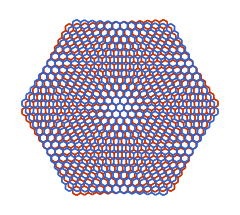

```mathematica
Block[{G},
(* G is a graph for a monolayer graphene *)
G=Block[{L=12,vs,es},
{{vs},{es}}=Last@Reap[Do[Block[{Rs,b},
Rs=({{Sqrt[3],3},{-Sqrt[3],3}}/2).RotationMatrix[θ];
b=l{1,0}+m{-1,1}/2+{1,1}/3;
If[OddQ[m],
b=b-{1,1}/6;
Sow[b.Rs<->(b+{2,-1}/3).Rs,"e"];
Sow[b.Rs<->(b+{-1,2}/3).Rs,"e"];
Sow[b.Rs<->(b+{-1,-1}/3).Rs,"e"],
If[m==0,Sow[b.Rs<->(b+{1,-2}/3).Rs,"e"]]];
Sow[b.Rs,"v"];],{l,0,L},{m,0,2l},{θ,Range[6]π/3}],{"v","e"}];
Graph[vs,es,VertexCoordinates->vs]];
Block[{g,θ=5°},
g=GraphicsComplex[VertexList[G],Line[First/@Most@ArrayRules@AdjacencyMatrix[G]]];
Graphics[{AbsoluteThickness[1],{Red,Rotate[g,θ/2,{0,0}]},{Blue,Rotate[g,-θ/2,{0,0}]}},ImageSize->240]]]
```

#### Moiré Brillouin Zone

Around K valley, the original K point splits to K_M^+ and K_M^- of the Moiré Brillouin zone (MBZ), representing the K points from the top and the bottom layer.

Their momentum differed by

q=2sin(θ/2)K,

where θ is the twist angle and K=4π/(3a) is the Γ–K momentum in the large BZ with a=√3 being the length of the primitive lattice vector (in units of the C-C bond length).

```mathematica
Graphics[{{EdgeForm[Black],White,Polygon[CirclePoints[{1,π/6},6]]},{AbsoluteThickness[0.8],Line[{{0,0},{-Sqrt[3],0}/2,{-Sqrt[3],1}/2,{0,0}}]},
{Text["\!\(Γ\_M\)",{0,0},{-1,0}],Text["\!\(K\_M\%+\)",{-Sqrt[3],1}/2,{1,0}],
Text["\!\(K\_M\%-\)",{-Sqrt[3],-1}/2,{1,0}],
Text["\!\(M\_M\)",{-Sqrt[3],0}/2,{1,0}],
Translate[{AbsoluteThickness[0.8],Arrowheads[{-0.06,0.06}],Arrow[{0,#}&/@{-1/2,1/2}],Text[Style["\!\(q\)",Background->White]]},{Sqrt[3]+0.3,0}/2]}},ImageSize->120]
```

-Graphics-

Reciprocal lattice vectors for Moiré BZ are spanned by the basis vector Q_±

Q_±=q(±(√3)/2,3/2),

such that Q=l_+Q_++l_-Q_- for l±∈ℤ is a generic reciprocal vector (Γ_M–Γ_M vector).

The momentum space lattice of K_M^+ and K_M^- points

K_M^±=q(-(√3)/2,±1/2)+Q.

```mathematica
Block[{R=3,Q,K1s,K2s},
Q={{Sqrt[3],3},{-Sqrt[3],3}}/2;
{K1s,K2s}=DeleteCases[Table[#+l.Q,{l,Tuples[Range[-#,#]&@Ceiling[2R/3],2]}]&[{-Sqrt[3],#}/2],k_/;Norm[N@k]-R>0.0001]&/@{1,-1};
Graphics[{{AbsoluteThickness[1],{Gray,Dashed,Circle[{0,0},R],Line[Append[#,First@#]]&@CirclePoints[{1,π/6},6]},
{Arrowheads[{{0.001,0.6,Arrowhead[6]}}],Translate[{{Arrow[{{0,0},RotationMatrix[# 2π/3].{0,-1}}],Text["\!\(q\_"<>ToString[#+1]<>"\)",RotationMatrix[# 2π/3].{0,-1.5}]}&/@{0,1,2}},{-Sqrt[3],1}/2]}},{Red,Point[K1s],Blue,Point[K2s]}},ImageSize->120]]
```

-Graphics-

red: K_M^+ (K points from top layer)

blue: K_M^- (K points from bottom layer)

K_M^± form a honeycomb lattice (K_M^+ and K_M^- are two sublattices). From K_M^+ to K_M^-, connected by three vectors

q_1=q(0,-1),q_2=q((√3)/2,1/2),q_3=q(-(√3)/2,1/2).

```mathematica
RotationMatrix[# 2π/3].{0,-1}&/@{0,1,2}
```

{{0,-1},{(√3)/2,1/2},{-(√3)/2,1/2}}

C_3 rotation.

M_M point

M_M=q(-(√3)/2,0)

#### Dirac Cones

We use the folded BZ scheme. Dirac cones of the same chirality are placed to each K_M point

H_0=-∑_(k∈MBZ) ∑_(K_M^s) c_(K_M^s,k)^†(k-K_M^s)·σ(s θ/2)c_(K_M^s,k),

c_(K_M^s,k) is the electron operator at momentum k coming from the K_M^s cone.

σ=(σ^1,σ^2) are chosen to be in-plane,

σ(φ)=R(φ) σ (R(φ))^†,

where the spacial rotation is given by R(φ)=e^(-ⅈ (φ/2) σ^3), under which

R(φ) σ (R(φ))^†=(cos φ σ^1+sin φ σ^2,-sin φ σ^1+cos φ σ^2)

```mathematica
Simplify[σExp[-ⅈ φ σ[3]/2]·#·σExp[ⅈ φ σ[3]/2]&/@{σ[1],σ[2]}]
```

{Cos[φ] σ[1]+Sin[φ] σ[2],-Sin[φ] σ[1]+Cos[φ] σ[2]}

Rotation of σ

#### Interlayer Coupling

Only keep the lowest order of the momentum transfer,

H_1=∑_(k∈MBZ) ∑_(K_M^s) ∑_q_a c_(K_M^s+q_a,k)^†T(q_a)c_(K_M^s,k)+h.c.,

The interlayer coupling with momentum transfer q_1 takes the general form

T(q_1)=w_0 σ^0+w_1 σ^1+ⅈ w_3 σ^3,

w_(0,1,3) are real parameters, typical setting: w_0≈-w_1 and w_3≈0.

The interlayer coupling with other momentum transfer is related to T(q_1) by

T(q_2)=R(2π/3)T(q_1)(R(2π/3))^†
=w_0 σ^0+w_1(-σ^1+√3 σ^2)/2+ⅈ w_3 σ^3,
T(q_3)=R(4π/3)T(q_1)(R(4π/3))^†
=w_0 σ^0+w_1(-σ^1-√3 σ^2)/2+ⅈ w_3 σ^3.

#### Symmetry Action

We consider the following symmetries (for K valley only),

M_y:c_(K_M^s,k)→σ^1 c_(M_y(K_M^s),M_y(k)),
C_3:c_(K_M^s,k)→e^(ⅈ 2π/3 σ^3)c_(C_3(K_M^s),C_3(k)),
C_2 𝒯:c_(K_M^s,k)→𝒦 σ^1 c_(K_M^s,k),

where M_y(k_x,k_y)=(k_x,-k_y), C_3(k_x,k_y)=(-k_x+√3 k_y,-√3 k_x-k_y)/2.

It can be verified that the Hamiltonian H=H_0+H_1 is invariant under these symmetries (that localize around the K valley).

```mathematica
Block[{R=2,θ=1.08°,w0,w1,w3,Q,Ks,ind,NK,σv,qs,T,h0,h1,h,My,C3,C2T},
{w0,w1,w3}=2.5{0.11,-0.12,0.};
Q={{Sqrt[3],3},{-Sqrt[3],3}}/2;
Ks=Association[#->DeleteCases[Table[#+l.Q,{l,Tuples[Range[-#,#]&@Ceiling[2R/3],2]}]&[{-Sqrt[3],#}/2],k_/;Norm[N@k]-R>0.0001]&/@{1,-1}];
ind=AssociationThread[#->Range@Length@#]&[Join@@Ks];
NK=Length@ind;
σv[φ_,i_]:=Block[{U},
U=MatrixExp[ⅈ φ PauliMatrix[3]/2];
 ConjugateTranspose[U].PauliMatrix[i].U];
h0[k:{_,_}]:=Sum[KroneckerProduct[SparseArray[ind/@{#,#}->-(k-#)⟦i⟧&/@Ks[s],{NK,NK}],σv[s θ/2,i]],{s,{1,-1}},{i,{1,2}}];
qs=RotationMatrix[# 2π/3].{0,-1}&/@{0,1,2};
T=AssociationThread[qs->(w0 σv[# 2π/3,0]+w1 σv[# 2π/3,1]+ⅈ w3 σv[# 2π/3,3]&/@{0,1,2})];
h1=Sum[KroneckerProduct[SparseArray[DeleteCases[ind/@{#,#+q}->1&/@Ks[1],{_,_Missing}->_],{NK,NK}],T[q]],{q,qs}];
h1=h1+ConjugateTranspose[h1];
h[k_]:=h0[k]+h1;
My=KroneckerProduct[SparseArray[ind/@{#,#{1,-1}}->1&/@Keys@ind,{NK,NK}],PauliMatrix[1]];
C3=KroneckerProduct[SparseArray[ind/@{RotationMatrix[2π/3].#,#}->1&/@Keys@ind,{NK,NK}],MatrixExp[ⅈ 2π/3 PauliMatrix[3]]];
C2T=KroneckerProduct[SparseArray[{Band[{1,1}]->1},{NK,NK}],PauliMatrix[1]];
Block[{kx,ky},
{kx,ky}=RandomReal[{-1,1},{2}];ArrayRules/@Chop/@{ConjugateTranspose[My].h[{kx,-ky}].My-h[{kx,ky}],ConjugateTranspose[C3].h[RotationMatrix[2π/3].{kx,ky}].C3-h[{kx,ky}],
ConjugateTranspose[C2T].Conjugate[h[{kx,ky}]].C2T-h[{kx,ky}]}
]]
```

{{{_,_}→0},{{_,_}→0},{{_,_}→0}}

Verification.

#### Band Structure

Put together Eq. (DisplayFormulaNumbered) and Eq. (DisplayFormulaNumbered)

H=H_0+H_1.

The two bands that are closest to the charge neutrality have the following band structure.

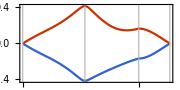

```mathematica
Block[{R=5,θ=1.08°,w0,w1,w3,Q,Ks,ind,NK,σv,qs,T,h0,h1,h},
{w0,w1,w3}=2.5{0.11,-0.12,0.00};
Q={{Sqrt[3],3},{-Sqrt[3],3}}/2;
Ks=Association[#->DeleteCases[Table[#+l.Q,{l,Tuples[Range[-#,#]&@Ceiling[2R/3],2]}]&[{-Sqrt[3],#}/2],k_/;Norm[N@k]-R>0.0001]&/@{1,-1}];
ind=AssociationThread[#->Range@Length@#]&[Join@@Ks];
NK=Length@ind;
σv[φ_,i_]:=Block[{U},
U=MatrixExp[ⅈ φ PauliMatrix[3]/2];
 ConjugateTranspose[U].PauliMatrix[i].U];
h0[k:{_,_}]:=Sum[KroneckerProduct[SparseArray[ind/@{#,#}->-(k-#)⟦i⟧&/@Ks[s],{NK,NK}],σv[s θ/2,i]],{s,{1,-1}},{i,{1,2}}];
qs=RotationMatrix[# 2π/3].{0,-1}&/@{0,1,2};
T=AssociationThread[qs->(w0 σv[# 2π/3,0]+w1 σv[# 2π/3,1]+ⅈ w3 σv[# 2π/3,3]&/@{0,1,2})];
h1=Sum[KroneckerProduct[SparseArray[DeleteCases[ind/@{#,#+q}->1&/@Ks[1],{_,_Missing}->_],{NK,NK}],T[q]],{q,qs}];
h1=h1+ConjugateTranspose[h1];
h[k_]:=h0[k]+h1;
Block[{Es},
Es[k:{_?NumericQ,_?NumericQ}]:=Block[{es,n,m=0},
es=Sort[Eigenvalues@Normal@h[k]];
n=Length[es];
es⟦n/2-m;;n/2+m+1⟧];
BZPlot[Es,{"\!\(K\_M\)","\!\(Γ\_M\)","\!\(M\_M\)","\!\(K\_M\)"},BZRules->{"\!\(Γ\_M\)"->{0,0},"\!\(K\_M\)"->{-Sqrt[3],1}/2,"\!\(M\_M\)"->{-Sqrt[3],0}/2},MomentumResolution->1/32,AspectRatio->0.5,ImageSize->180]
]]
```

Equal energy contour (for the lower band). Black hexagon trace out the Moiré BZ.

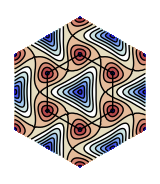

```mathematica
Block[{R=4,θ=1.08°,w0,w1,w3,Q,Ks,ind,NK,σv,qs,T,h0,h1,h},
{w0,w1,w3}=2.5{0.11,-0.12,0.};
Q={{Sqrt[3],3},{-Sqrt[3],3}}/2;
Ks=Association[#->DeleteCases[Table[#+l.Q,{l,Tuples[Range[-#,#]&@Ceiling[2R/3],2]}]&[{-Sqrt[3],#}/2],k_/;Norm[N@k]-R>0.0001]&/@{1,-1}];
ind=AssociationThread[#->Range@Length@#]&[Join@@Ks];
NK=Length@ind;
σv[φ_,i_]:=Block[{U},
U=MatrixExp[ⅈ φ PauliMatrix[3]/2];
ConjugateTranspose[U].PauliMatrix[i].U];
h0[k:{_,_}]:=Sum[KroneckerProduct[SparseArray[ind/@{#,#}->-(k-#)⟦i⟧&/@Ks[s],{NK,NK}],σv[s θ/2,i]],{s,{1,-1}},{i,{1,2}}];
qs=RotationMatrix[# 2π/3].{0,-1}&/@{0,1,2};
T=AssociationThread[qs->(w0 σv[# 2π/3,0]+w1 σv[# 2π/3,1]+ⅈ w3 σv[# 2π/3,3]&/@{0,1,2})];
h1=Sum[KroneckerProduct[SparseArray[DeleteCases[ind/@{#,#+q}->1&/@Ks[1],{_,_Missing}->_],{NK,NK}],T[q]],{q,qs}];
h1=h1+ConjugateTranspose[h1];
h[k_]:=h0[k]+h1;
Block[{Es},
Es[k:{_?NumericQ,_?NumericQ}]:=Block[{es,n,m=0},
es=Sort[Eigenvalues@Normal@h[k]];
n=Length[es];
es⟦n/2-m⟧];
ContourPlot[Es[{kx,ky}],{kx,-Sqrt[3],Sqrt[3]},{ky,-2,2},PlotRange->All,MeshFunctions->{#3&},MaxRecursion->2,PlotPoints->10,Contours->Range[-1,1,0.04239],ContourLabels->None,ContourStyle->Directive[AbsoluteThickness[1],Opacity[1]],RegionFunction->(Abs[#2]+Abs[#1/Sqrt[3]]≤2&), Epilog->{Line@Append[#,First@#]&@CirclePoints[{1,π/6},6]},AspectRatio->Automatic,Frame->None,ImageSize->160]
]]
```

Depending on the parameters, the van Hove singularity does not correspond to a definite filling. Empirically, it is around 1/2±1/8 filling.

The Fermi surface at fillings 0:(1/8):1 for both lower and upper bands are

```mathematica
Block[{R=3,θ=1.08°,w0,w1,w3,Q,Ks,ind,NK,σv,qs,T,h0,h1,h},
{w0,w1,w3}=2.5{0.11,-0.12,0.};
Q={{Sqrt[3],3},{-Sqrt[3],3}}/2;
Ks=Association[#->DeleteCases[Table[#+l.Q,{l,Tuples[Range[-#,#]&@Ceiling[2R/3],2]}]&[{-Sqrt[3],#}/2],k_/;Norm[N@k]-R>0.0001]&/@{1,-1}];
ind=AssociationThread[#->Range@Length@#]&[Join@@Ks];
NK=Length@ind;
σv[φ_,i_]:=Block[{U},
U=MatrixExp[ⅈ φ PauliMatrix[3]/2];
ConjugateTranspose[U].PauliMatrix[i].U];
h0[k:{_,_}]:=Sum[KroneckerProduct[SparseArray[ind/@{#,#}->-(k-#)⟦i⟧&/@Ks[s],{NK,NK}],σv[s θ/2,i]],{s,{1,-1}},{i,{1,2}}];
qs=RotationMatrix[# 2π/3].{0,-1}&/@{0,1,2};
T=AssociationThread[qs->(w0 σv[# 2π/3,0]+w1 σv[# 2π/3,1]+ⅈ w3 σv[# 2π/3,3]&/@{0,1,2})];
h1=Sum[KroneckerProduct[SparseArray[DeleteCases[ind/@{#,#+q}->1&/@Ks[1],{_,_Missing}->_],{NK,NK}],T[q]],{q,qs}];
h1=h1+ConjugateTranspose[h1];
h[k_]:=h0[k]+h1;
Block[{Es},
Es[k:{_?NumericQ,_?NumericQ}]:=Block[{es,n,m=0},
es=Sort[Eigenvalues@Normal@h[k]];
n=Length[es];
es⟦n/2-m;;n/2+m+1⟧];
FSPlot[Es]
]]
```

-Graphics--Graphics-

The 1/2 filling Fermi surface is close but slightly larger than the triangle that connects the M_M points.

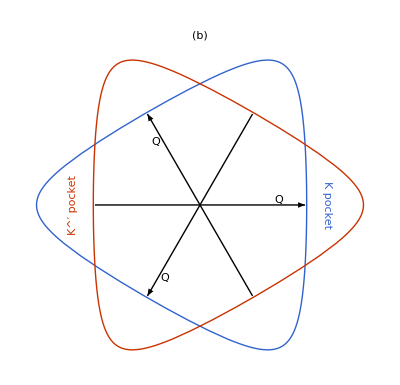
-Graphics--Graphics-

```mathematica
Row[{
Block[{R=2,θ=1.08°,w0,w1,w3,Q,Ks,ind,NK,σv,qs,T,h0,h1,h,FSPlot2},
{w0,w1,w3}=2.5{0.11,-0.12,0.};
Q={{Sqrt[3],3},{-Sqrt[3],3}}/2;
Ks=Association[#->DeleteCases[Table[#+l.Q,{l,Tuples[Range[-#,#]&@Ceiling[2R/3],2]}]&[{-Sqrt[3],#}/2],k_/;Norm[N@k]-R>0.0001]&/@{1,-1}];
ind=AssociationThread[#->Range@Length@#]&[Join@@Ks];
NK=Length@ind;
σv[φ_,i_]:=Block[{U},
U=MatrixExp[ⅈ φ PauliMatrix[3]/2];
ConjugateTranspose[U].PauliMatrix[i].U];
h0[k:{_,_}]:=Sum[KroneckerProduct[SparseArray[ind/@{#,#}->-(k-#)⟦i⟧&/@Ks[s],{NK,NK}],σv[s θ/2,i]],{s,{1,-1}},{i,{1,2}}];
qs=RotationMatrix[# 2π/3].{0,-1}&/@{0,1,2};
T=AssociationThread[qs->(w0 σv[# 2π/3,0]+w1 σv[# 2π/3,1]+ⅈ w3 σv[# 2π/3,3]&/@{0,1,2})];
h1=Sum[KroneckerProduct[SparseArray[DeleteCases[ind/@{#,#+q}->1&/@Ks[1],{_,_Missing}->_],{NK,NK}],T[q]],{q,qs}];
h1=h1+ConjugateTranspose[h1];
h[k_]:=h0[k]+h1;
FSPlot2[Ek_,L_:5]:=Block[{ks,ws,es,ord,g},
{ks,ws}=Thread@N@Table[If[Sort[l].{1,2}/3≤L,{l.{{1/Sqrt[3],1},{-1/Sqrt[3],1}}/(2L),Which[l=={0,0},1/6,l=={L,L},1/3,Sort[l]=={0,3L/2},1/4,Sort[l].{1,0}==0||Sort[l].{1,2}/3==L,1/2,True,1]},Nothing],
{l,Tuples[Range[0,3L/2],2]}];
es=Ek/@ks;
ord=Ordering[es];
g=First@ListContourPlot[MapThread[Append,{ks⟦ord⟧,Rescale[#,MinMax@#]&@Accumulate[ws⟦ord⟧]}],
Contours->Range[1/8,7/8,1/8],ContourLabels->None,ContourStyle->(Directive[AbsoluteThickness[If[#==1/2,1.6,0.5]],Opacity[1],GrayLevel[If[#==1/2,0.,0.2]]]&/@Range[1/8,7/8,1/8]),ColorFunction->(Lighter[Blend[{RGBColor[0.163302, 0.119982, 0.79353],RGBColor[0.254221, 0.313173, 0.892833],RGBColor[0.407119, 0.543513, 0.938275],RGBColor[0.572715, 0.73338, 0.95065],RGBColor[0.720374, 0.855234, 0.928635],RGBColor[0.831017, 0.903518, 0.868326],GrayLevel[1],RGBColor[0.894452, 0.880139, 0.77279],RGBColor[0.907999, 0.789417, 0.652903],RGBColor[0.874505, 0.639254, 0.522424],RGBColor[0.79915, 0.446142, 0.391971],RGBColor[0.685695, 0.242449, 0.268261],RGBColor[0.534081, 0.0853132, 0.16669]},#],0.7]&)];
{Scale[Rotate[g,2π #/3,{0,0}]&/@Range[0,2],{1,#},{0,0}]&/@{1,-1}}];
Block[{Ek,g,bz},
Ek[k:{_?NumericQ,_?NumericQ}]:=Block[{es,n},
es=Sort[Eigenvalues@Normal@h[k]];
n=Length[es];
es⟦n/2⟧];
g=FSPlot2[Ek,18];
bz={AbsoluteThickness[1],Line[Append[#,First@#]]&@CirclePoints[{1,π/6},6]};
Graphics[{Translate[{g,bz,{Text["\!\(Γ\_M\)"],Text["\!\(M\_M\)",{-Sqrt[3]/2,0},{1,0}],Text["\!\(M\_M\%′\)",{-Sqrt[3]/4,-3/4},{0.8,0.7}],Text["\!\(K\_M\)",{-Sqrt[3]/2,1/2},{1,-0.2}],Text["\!\(K\_M\%′\)",{-Sqrt[3]/2,-1/2},{1,0.2}]},Text["\!\(K\) valley",{0,-1},{0,1}]},{-0.92,0}],Translate[{Scale[g,{-1,1}],bz,
GraphicsComplex[CirclePoints[{1,π/6},6],
{AbsoluteThickness[1.2],Arrowheads[0.06],Arrow[{{1,2},{1,6},{5,6}}],Text["\!\(q\_"<>#1<>"\)",#2,#3]&@@@{{"3",2,{-4,0.5}},{"1",6,{-1.2,-2.5}},{"2",6,{2.2,1.6}}}}],
Text["\!\(K\^′\) valley",{0,-1},{0,1}]},{0.92,0}],
{AbsoluteThickness[1.2],Arrowheads[{-0.04,0.04}],Arrow[Table[#[x],{x,0,1,0.1}]&@BSplineFunction[{{-0.3,-0.8},{-0.1,-0.9},{0.1,-0.9},{0.3,-0.8}}]],Text["𝒯",{0,-1.1}]},
Text["(a)",{0,0.9}]},ImageSize->{Automatic,120}]
]],
Block[{μ=1,α=1/3,FS},
FS=Block[{kF,t0,t1},
kF=FSOrbit[α,μ];
{{t0,t1}}=kF@"Domain";
Cases[ParametricPlot[kF[t0+λ(t1-t0)],{λ,0,1}],_Line,∞]];
Graphics[{{Blue,FS,Red,Scale[FS,{-1,1},{0,0}]},{Blue,Text["\!\(K\) pocket",{1.05,0.},{0,0},{0,-1}],Red,Text["\!\(K\^′\) pocket",{-1.05,0.},{0,0},{0,1}]},{Arrowheads[{0.08}],{Arrow[{-#1,#1}],Text["\!\(Q\_"<>#2<>"\)",0.75#1,1.25{{0,1},{-1,0}}.#1]}&@@@Thread@{CirclePoints[{Sqrt[3μ]/2,0},3],{"1","2","3"}}},
Text["(b)",{0,1.4}]},ImageSize->{Automatic,120}]]
},Spacer[1]]
```

Fermi Surface Plot

```mathematica
FSPlot[Es_]:=Block[{L=10,kws,bands,ref,FSplot},
kws=Table[If[Sort[l].{1,2}/3≤L,{l.{{1/Sqrt[3],1},{-1/Sqrt[3],1}}/(2L),Which[l=={0,0},1/6,l=={L,L},1/3,Sort[l]=={0,3L/2},1/4,Sort[l].{1,0}==0||Sort[l].{1,2}/3==L,1/2,True,1]},Nothing],
{l,Tuples[Range[0,3L/2],2]}];
bands=Thread[Table[{e,#2},{e,Es[#1]}]&@@@kws];
ref[dat_,n_]:=Append[-{#1,#2}+2({#1,#2}.n)n,#3]&@@@dat;
FSplot[band_]:=Block[{es,ws,den,dat},
{es,ws}=Thread@SortBy[band,First];
ws=(#-First[#]/2)/Last[#]&@Accumulate[ws];
den=Interpolation[Thread@{es,ws},InterpolationOrder->1];
dat=DeleteDuplicates[Flatten[FoldList[ref,MapThread[Append,{N@kws⟦All,1⟧,den/@band⟦All,1⟧}],CirclePoints[{1,2π/3},6]],1],Abs[#1⟦{1,2}⟧-#2⟦{1,2}⟧]<0.0001&];
ListContourPlot[dat,Epilog->{AbsoluteThickness[1],Opacity[0.3],Line[Append[#,First@#]]&@CirclePoints[{Sqrt[3]/2,#},3]&/@{0,π}},Contours->Range[0,1,1/8],ContourStyle->Directive[AbsoluteThickness[1.2],Opacity[1]],AspectRatio->Automatic,Frame->None,ImageSize->100]];
Row[FSplot/@bands]]
```

#### Break “Particle-Hole”

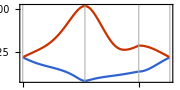

```mathematica
Block[{R=5,θ=1.08°,w0,w1,w3,Q,Ks,ind,NK,σv,qs,T,h0,h1,h},
{w0,w1,w3}=3.5{0.11,-0.12,0.04};
Q={{Sqrt[3],3},{-Sqrt[3],3}}/2;
Ks=Association[#->DeleteCases[Table[#+l.Q,{l,Tuples[Range[-#,#]&@Ceiling[2R/3],2]}]&[{-Sqrt[3],#}/2],k_/;Norm[N@k]-R>0.0001]&/@{1,-1}];
ind=AssociationThread[#->Range@Length@#]&[Join@@Ks];
NK=Length@ind;
σv[φ_,i_]:=Block[{U},
U=MatrixExp[ⅈ φ PauliMatrix[3]/2];
 ConjugateTranspose[U].PauliMatrix[i].U];
h0[k:{_,_}]:=Sum[KroneckerProduct[SparseArray[ind/@{#,#}->-(k-#)⟦i⟧&/@Ks[s],{NK,NK}],σv[s θ/2,i]],{s,{1,-1}},{i,{1,2}}];
qs=RotationMatrix[# 2π/3].{0,-1}&/@{0,1,2};
T=AssociationThread[qs->(w0 σv[# 2π/3,0]+w1 σv[# 2π/3,1]+ⅈ w3 σv[# 2π/3,3]&/@{0,1,2})];
h1=Sum[KroneckerProduct[SparseArray[DeleteCases[ind/@{#,#+q}->1&/@Ks[1],{_,_Missing}->_],{NK,NK}],T[q]],{q,qs}];
h1=h1+ConjugateTranspose[h1];
h[k_]:=h0[k]+h1;
Block[{Es},
Es[k:{_?NumericQ,_?NumericQ}]:=Block[{es,n,m=0},
es=Sort[Eigenvalues@Normal@h[k]];
n=Length[es];
es⟦n/2-m;;n/2+m+1⟧];
BZPlot[Es,{"\!\(K\_M\)","\!\(Γ\_M\)","\!\(M\_M\)","\!\(K\_M\)"},BZRules->{"\!\(Γ\_M\)"->{0,0},"\!\(K\_M\)"->{-Sqrt[3],1}/2,"\!\(M\_M\)"->{-Sqrt[3],0}/2},MomentumResolution->1/32,AspectRatio->0.5,ImageSize->180]
]]
```

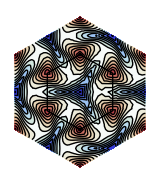

```mathematica
Block[{R=5,θ=1.08°,w0,w1,w3,Q,Ks,ind,NK,σv,qs,T,h0,h1,h},
{w0,w1,w3}=3.5{0.11,-0.12,0.04};
Q={{Sqrt[3],3},{-Sqrt[3],3}}/2;
Ks=Association[#->DeleteCases[Table[#+l.Q,{l,Tuples[Range[-#,#]&@Ceiling[2R/3],2]}]&[{-Sqrt[3],#}/2],k_/;Norm[N@k]-R>0.0001]&/@{1,-1}];
ind=AssociationThread[#->Range@Length@#]&[Join@@Ks];
NK=Length@ind;
σv[φ_,i_]:=Block[{U},
U=MatrixExp[ⅈ φ PauliMatrix[3]/2];
ConjugateTranspose[U].PauliMatrix[i].U];
h0[k:{_,_}]:=Sum[KroneckerProduct[SparseArray[ind/@{#,#}->-(k-#)⟦i⟧&/@Ks[s],{NK,NK}],σv[s θ/2,i]],{s,{1,-1}},{i,{1,2}}];
qs=RotationMatrix[# 2π/3].{0,-1}&/@{0,1,2};
T=AssociationThread[qs->(w0 σv[# 2π/3,0]+w1 σv[# 2π/3,1]+ⅈ w3 σv[# 2π/3,3]&/@{0,1,2})];
h1=Sum[KroneckerProduct[SparseArray[DeleteCases[ind/@{#,#+q}->1&/@Ks[1],{_,_Missing}->_],{NK,NK}],T[q]],{q,qs}];
h1=h1+ConjugateTranspose[h1];
h[k_]:=h0[k]+h1;
Block[{Es},
Es[k:{_?NumericQ,_?NumericQ}]:=Block[{es,n,m=0},
es=Sort[Eigenvalues@Normal@h[k]];
n=Length[es];
es⟦n/2-m⟧];
ContourPlot[Es[{kx,ky}],{kx,-Sqrt[3],Sqrt[3]},{ky,-2,2},PlotRange->All,MeshFunctions->{#3&},MaxRecursion->2,PlotPoints->10,Contours->Range[-1,1,0.01],ContourLabels->None,ContourStyle->Directive[AbsoluteThickness[1],Opacity[1]],RegionFunction->(Abs[#2]+Abs[#1/Sqrt[3]]≤2&), Epilog->{Line@Append[#,First@#]&@CirclePoints[{1,π/6},6]},AspectRatio->Automatic,Frame->None,ImageSize->160]
]]
```

```mathematica
Block[{R=5,θ=1.08°,w0,w1,w3,Q,Ks,ind,NK,σv,qs,T,h0,h1,h},
{w0,w1,w3}=3.5{0.11,-0.12,0.04};
Q={{Sqrt[3],3},{-Sqrt[3],3}}/2;
Ks=Association[#->DeleteCases[Table[#+l.Q,{l,Tuples[Range[-#,#]&@Ceiling[2R/3],2]}]&[{-Sqrt[3],#}/2],k_/;Norm[N@k]-R>0.0001]&/@{1,-1}];
ind=AssociationThread[#->Range@Length@#]&[Join@@Ks];
NK=Length@ind;
σv[φ_,i_]:=Block[{U},
U=MatrixExp[ⅈ φ PauliMatrix[3]/2];
ConjugateTranspose[U].PauliMatrix[i].U];
h0[k:{_,_}]:=Sum[KroneckerProduct[SparseArray[ind/@{#,#}->-(k-#)⟦i⟧&/@Ks[s],{NK,NK}],σv[s θ/2,i]],{s,{1,-1}},{i,{1,2}}];
qs=RotationMatrix[# 2π/3].{0,-1}&/@{0,1,2};
T=AssociationThread[qs->(w0 σv[# 2π/3,0]+w1 σv[# 2π/3,1]+ⅈ w3 σv[# 2π/3,3]&/@{0,1,2})];
h1=Sum[KroneckerProduct[SparseArray[DeleteCases[ind/@{#,#+q}->1&/@Ks[1],{_,_Missing}->_],{NK,NK}],T[q]],{q,qs}];
h1=h1+ConjugateTranspose[h1];
h[k_]:=h0[k]+h1;
Block[{Es},
Es[k:{_?NumericQ,_?NumericQ}]:=Block[{es,n,m=0},
es=Sort[Eigenvalues@Normal@h[k]];
n=Length[es];
es⟦n/2-m;;n/2+m+1⟧];
FSPlot[Es]
]]
```

-Graphics--Graphics-

### Pocket Model (Multi-orbit)

#### Around Γ_M Point

Collect the wave functions around Γ_M point (two frames are taken from upper and lower bands respectively)

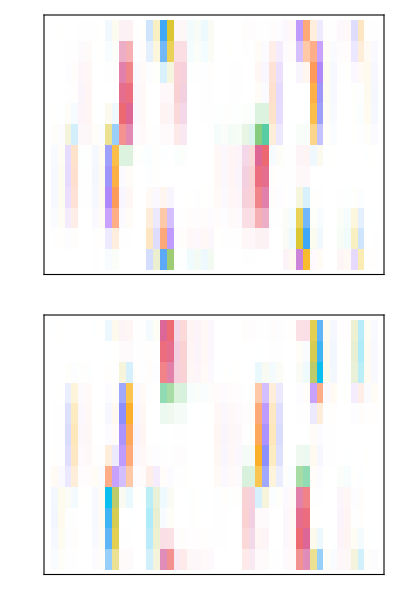

```mathematica
Block[{R=3,θ=1.08°,w0,w1,Q,Ks,ind,NK,σv,qs,T,h0,h1,h},
{w0,w1}=2.5{0.11,-0.12};
Q={{Sqrt[3],3},{-Sqrt[3],3}}/2;
Ks=Association[#->DeleteCases[Table[#+l.Q,{l,Tuples[Range[-#,#]&@Ceiling[2R/3],2]}]&[{-Sqrt[3],#}/2],k_/;Norm[N@k]-R>0.0001]&/@{1,-1}];
ind=AssociationThread[#->Range@Length@#]&[Join@@Ks];
NK=Length@ind;
σv[φ_,i_]:=Block[{U},
U=MatrixExp[ⅈ φ PauliMatrix[3]/2];
ConjugateTranspose[U].PauliMatrix[i].U];
h0[k:{_,_}]:=Sum[KroneckerProduct[SparseArray[ind/@{#,#}->-(k-#)⟦i⟧&/@Ks[s],{NK,NK}],σv[s θ/2,i]],{s,{1,-1}},{i,{1,2}}];
qs=RotationMatrix[# 2π/3].{0,-1}&/@{0,1,2};
T=AssociationThread[qs->(w0 σv[# 2π/3,0]+w1 σv[# 2π/3,1]&/@{0,1,2})];
h1=Sum[KroneckerProduct[SparseArray[DeleteCases[ind/@{#,#+q}->1&/@Ks[1],{_,_Missing}->_],{NK,NK}],T[q]],{q,qs}];
h1=h1+ConjugateTranspose[h1];
h[k_]:=h0[k]+h1;
Block[{u,K0={0,0},k0=0.41,dϕ=π/6,zs},
u[k:{_?NumericQ,_?NumericQ}]:=Block[{hk,eigs,n},
hk=h[k];
n=Length@hk;
eigs=SortBy[First]@Thread@Eigensystem@hk;
#/Sign[Mean@#]&/@eigs⟦n/2;;n/2+1,2⟧];
zs=Exp[ⅈ Range[dϕ,2π,dϕ]];
Column[ComplexMatrixPlot[#,PlotRangePadding->None,FrameStyle->Black,FrameTicks->None,ImageSize->160]&/@Thread[u[ReIm@#+K0]&/@(k0 zs)],Spacings->0.1]]]
```

Construct density matrix

ρ=∑_(n,k) nknk.

Diagonalize the density matrix

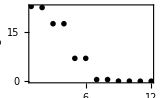

```mathematica
Block[{R=3,θ=1.08°,w0,w1,Q,Ks,ind,NK,σv,qs,T,h0,h1,h},
{w0,w1}=2.5{0.11,-0.12};
Q={{Sqrt[3],3},{-Sqrt[3],3}}/2;
Ks=Association[#->DeleteCases[Table[#+l.Q,{l,Tuples[Range[-#,#]&@Ceiling[2R/3],2]}]&[{-Sqrt[3],#}/2],k_/;Norm[N@k]-R>0.0001]&/@{1,-1}];
ind=AssociationThread[#->Range@Length@#]&[Join@@Ks];
NK=Length@ind;
σv[φ_,i_]:=Block[{U},
U=MatrixExp[ⅈ φ PauliMatrix[3]/2];
ConjugateTranspose[U].PauliMatrix[i].U];
h0[k:{_,_}]:=Sum[KroneckerProduct[SparseArray[ind/@{#,#}->-(k-#)⟦i⟧&/@Ks[s],{NK,NK}],σv[s θ/2,i]],{s,{1,-1}},{i,{1,2}}];
qs=RotationMatrix[# 2π/3].{0,-1}&/@{0,1,2};
T=AssociationThread[qs->(w0 σv[# 2π/3,0]+w1 σv[# 2π/3,1]&/@{0,1,2})];
h1=Sum[KroneckerProduct[SparseArray[DeleteCases[ind/@{#,#+q}->1&/@Ks[1],{_,_Missing}->_],{NK,NK}],T[q]],{q,qs}];
h1=h1+ConjugateTranspose[h1];
h[k_]:=h0[k]+h1;
Block[{u,K0={0,0},k0=0.3,dϕ=π/24,zs,ρ},
u[k:{_?NumericQ,_?NumericQ}]:=Block[{hk,eigs,n},
hk=h[k];
n=Length@hk;
eigs=SortBy[First]@Thread@Eigensystem@hk;
#/Sign[Mean@#]&/@eigs⟦n/2;;n/2+1,2⟧];
zs=Exp[ⅈ Range[dϕ,2π,dϕ]];
ρ=Total[Conjugate[#]⊗#&/@Flatten[u[ReIm@#+K0]&/@(k0 zs),1]];
ListPlot[Eigenvalues[ρ]⟦;;12⟧,PlotRange->All,PlotStyle->Black,FrameLabel->{"orbital","weight"},ImageSize->160]]]
```

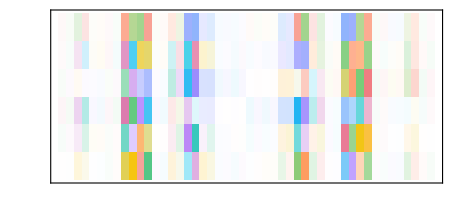

```mathematica
Block[{R=3,θ=1.08°,w0,w1,Q,Ks,ind,NK,σv,qs,T,h0,h1,h},
{w0,w1}=2.5{0.11,-0.12};
Q={{Sqrt[3],3},{-Sqrt[3],3}}/2;
Ks=Association[#->DeleteCases[Table[#+l.Q,{l,Tuples[Range[-#,#]&@Ceiling[2R/3],2]}]&[{-Sqrt[3],#}/2],k_/;Norm[N@k]-R>0.0001]&/@{1,-1}];
ind=AssociationThread[#->Range@Length@#]&[Join@@Ks];
NK=Length@ind;
σv[φ_,i_]:=Block[{U},
U=MatrixExp[ⅈ φ PauliMatrix[3]/2];
ConjugateTranspose[U].PauliMatrix[i].U];
h0[k:{_,_}]:=Sum[KroneckerProduct[SparseArray[ind/@{#,#}->-(k-#)⟦i⟧&/@Ks[s],{NK,NK}],σv[s θ/2,i]],{s,{1,-1}},{i,{1,2}}];
qs=RotationMatrix[# 2π/3].{0,-1}&/@{0,1,2};
T=AssociationThread[qs->(w0 σv[# 2π/3,0]+w1 σv[# 2π/3,1]&/@{0,1,2})];
h1=Sum[KroneckerProduct[SparseArray[DeleteCases[ind/@{#,#+q}->1&/@Ks[1],{_,_Missing}->_],{NK,NK}],T[q]],{q,qs}];
h1=h1+ConjugateTranspose[h1];
h[k_]:=h0[k]+h1;
Block[{u,K0={0,0},k0=0.3,dϕ=π/24,zs,ρ},
u[k:{_?NumericQ,_?NumericQ}]:=Block[{hk,eigs,n},
hk=h[k];
n=Length@hk;
eigs=SortBy[First]@Thread@Eigensystem@hk;
#/Sign[Mean@#]&/@eigs⟦n/2;;n/2+1,2⟧];
zs=Exp[ⅈ Range[dϕ,2π,dϕ]];
ρ=Total[Conjugate[#]⊗#&/@Flatten[u[ReIm@#+K0]&/@(k0 zs),1]];
ComplexMatrixPlot[Eigenvectors[ρ]⟦;;6⟧,FrameTicks->None,ImageSize->240]]]
```

There are 6 leading orbitals. Arrange them in the a 3×2 basis c_aσ (a=1,2,3, σ=1,2).

In the 6-orbital basis, the effective Hamiltonian reads

H_(Γ,eff)=∑_k c_k^†h_(Γ,eff)(k)c_k,

h_(Γ,eff)(k)=(ϵ_1 σ^1 | v_1(k_x σ^1-k_y σ^2) | v_1(k_x σ^2+k_y σ^1)
v_1(k_x σ^1-k_y σ^2) | ϵ_2 σ^0+v_2 k·σ | 0
v_1(k_x σ^2+k_y σ^1) | 0 | -ϵ_2 σ^0+v_2 k·σ).

```mathematica
Block[{w=2,k0=0.4,heff},
heff=Chop[tTr[{PocketExpand[w,k0],σ/@Range[0,3],{1,kx/k0,ky/k0}},{{1,5},{2,6}}],0.5k0];
MatrixForm@heff]
```

(0.+1.79214 σ[1] | 1.55589 kx σ[1]-1.55589 ky σ[2] | 1.54482 ky σ[1]+1.54482 kx σ[2]
1.55589 kx σ[1]-1.55589 ky σ[2] | 2.02945 σ[0]+0.699197 kx σ[1]+0.699197 ky σ[2] | 0.
1.54482 ky σ[1]+1.54482 kx σ[2] | 0. | -2.03445 σ[0]+0.699839 kx σ[1]+0.699839 ky σ[2])

Expansion.

This is also equivalent to

h_(Γ,eff)(k)=(ϵ_1 σ^1 | v_1(k_x σ^0-ⅈ k_y σ^3) | v_1(k_x σ^0-ⅈ k_y σ^3)
v_1(k_x σ^0+ⅈ k_y σ^3) | ϵ_2 σ^0+v_2 k·σ | 0
v_1(k_x σ^0+ⅈ k_y σ^3) | 0 | -ϵ_2 σ^0-v_2 k·σ).

There are 4 real parameters: ϵ_(1,2) and v_(1,2). Their typical values are measured to be

w | ϵ_1 | ϵ_2 | v_1 | v_2
1.0 | 2.6 | 2.8 | 1.6 | 0.8
2.0 | 1.8 | 2.0 | 1.6 | 0.8
3.0 | 1.0 | 1.3 | 1.4 | 0.7
4.0 | 0.4 | 0.6 | 1.2 | 0.6

From this observation,

There is a small band gap ϵ_2-ϵ_1 that separates the middle two bands from the rest of the four high energy bands.

As the twist angle θ decreases (the interlayer coupling w increases), ϵ_(1,2) both becomes smaller → approaching towards the flat bands at the magic angle.

Roughly, v_2≈0.5 v_1 is always the case. In fact, 0≤v_2/v_1≤1 ratio characterizes the triangular anisotropy.

Pocket Expansion

```mathematica
Block[{w=2,k0=0.4,Ms,ϵ},
Ms=PocketExpand[w,k0];
ϵ=0.5k0;
TableForm[Map[ComplexMatrixPlot[#,PlotLabel->Style[NumberForm[Max@Abs@Flatten@#,{2,2}],12],FrameStyle->Black,FrameTicks->None,ImageSize->30]&,Chop[Ms,ϵ],{2}],TableHeadings->{σ/@Range[0,3],{"1","\!\(k\_x\)","\!\(k\_y\)"}}]]
```

| 1 | k_x | k_y
σ[0] | -Graphics- | -Graphics- | -Graphics-
σ[1] | -Graphics- | -Graphics- | -Graphics-
σ[2] | -Graphics- | -Graphics- | -Graphics-
σ[3] | -Graphics- | -Graphics- | -Graphics-

The following function carries out the expansion around Γ point and perform the gauge fixing to the basis. Eventually a projection operator P is obtained, which can be used to project the band Hamiltonian to the pocket Hamiltonian.

```mathematica
PocketExpand[w_,k0_]:=Block[{R=3,w0,w1,Q,Ks,ind,NK,σv,qs,T,h0,h1,h},
{w0,w1}=w{0.11,-0.12};
Q={{Sqrt[3],3},{-Sqrt[3],3}}/2;
Ks=Association[#->DeleteCases[Table[#+l.Q,{l,Tuples[Range[-#,#]&@Ceiling[2R/3],2]}]&[{-Sqrt[3],#}/2],k_/;Norm[N@k]-R>0.0001]&/@{1,-1}];
ind=AssociationThread[#->Range@Length@#]&[Join@@Ks];
NK=Length@ind;
σv[φ_,i_]:=Block[{U},
U=MatrixExp[ⅈ φ PauliMatrix[3]/2];
ConjugateTranspose[U].PauliMatrix[i].U];
h0[k:{_,_}]:=Block[{θ=1.08°},Sum[KroneckerProduct[SparseArray[ind/@{#,#}->-(k-#)⟦i⟧&/@Ks[s],{NK,NK}],σv[s θ/2,i]],{s,{1,-1}},{i,{1,2}}]];
qs=RotationMatrix[# 2π/3].{0,-1}&/@{0,1,2};
T=AssociationThread[qs->(w0 σv[# 2π/3,0]+w1 σv[# 2π/3,1]&/@{0,1,2})];
h1=Sum[KroneckerProduct[SparseArray[DeleteCases[ind/@{#,#+q}->1&/@Ks[1],{_,_Missing}->_],{NK,NK}],T[q]],{q,qs}];
h1=h1+ConjugateTranspose[h1];
h[k_]:=h0[k]+h1;
Block[{u,K0={0,0},dϕ=π/6,zs,ρ,P,heff},
u[k:{_?NumericQ,_?NumericQ}]:=Block[{hk,eigs,n},
hk=h[k];
n=Length@hk;
eigs=SortBy[First]@Thread@Eigensystem@hk;
#/Sign[Mean@#]&/@eigs⟦n/2;;n/2+1,2⟧];
zs=Exp[ⅈ Range[dϕ,2π,dϕ]];
ρ=Total[Conjugate[#]⊗#&/@Flatten[u[ReIm@#+K0]&/@(k0 zs),1]];
P=Eigenvectors[ρ]⟦;;6⟧;
P=Conjugate[Eigenvectors[(#+ConjugateTranspose[#])/2&@(P.h[K0].ConjugateTranspose[P])]].P;
P=P⟦{6,5,4,3,1,2}⟧;
heff[k_]:=(#+ConjugateTranspose[#])/2&@(P.h[k].ConjugateTranspose[P]);
Block[{symm,X,Y,Z,U},
symm=(#+ConjugateTranspose[#])&;
X:=symm@heff[K0+{0.01,0}]-heff[K0];
Y:=symm@heff[K0+{0,0.01}]-heff[K0];
Z:=symm@(ⅈ X.Y);
Do[
U=Last/@Reverse@SortBy[First]@Thread@Eigensystem@Z⟦blk,blk⟧;
U=DiagonalMatrix[{#,Conjugate[#]}].U&@Sqrt@Sign[(Conjugate[U].X⟦blk,blk⟧.Transpose[U])⟦1,2⟧];
P⟦blk⟧=Conjugate[U].P⟦blk⟧,
{blk,{{3,4},{5,6}}}];
U=DiagonalMatrix[{#,Conjugate[#]}]&@Sign[#⟦1,3⟧+#⟦1,4⟧+Conjugate[#⟦2,3⟧-#⟦2,4⟧]]&@X;
P⟦{1,2}⟧=MatrixExp[-ⅈ π/4 PauliMatrix[2]].Conjugate[U].P⟦{1,2}⟧;
P⟦{3,4}⟧=Sign[Tr[X⟦{1,2},{3,4}⟧.PauliMatrix[1]]]P⟦{3,4}⟧;
P⟦{5,6}⟧=Sign[Tr[X⟦{1,2},{5,6}⟧.PauliMatrix[2]]]P⟦{5,6}⟧];
Coefficient[(Normalize/@{Abs@zs,Re@zs,Im@zs}).(Map[Abstract,Partition[heff[K0+ReIm[k0 #]],{2,2}],{2}]&/@zs),σ[#]]&/@Range[0,3]
]];
```

#### Shape of Fermi Surface

Using the effective pocket model Eq. (DisplayFormulaNumbered),

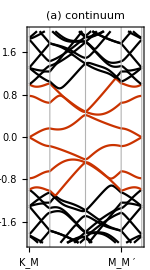
-Graphics- | -Graphics-
 | -Graphics-

```mathematica
Grid[{{Block[{R=4,θ=1.08°,w0,w1,Q,Ks,ind,NK,σv,qs,T,h0,h1,h},
{w0,w1}=2.5{0.11,-0.12};
Q={{Sqrt[3],3},{-Sqrt[3],3}}/2;
Ks=Association[#->DeleteCases[Table[#+l.Q,{l,Tuples[Range[-#,#]&@Ceiling[2R/3],2]}]&[{-Sqrt[3],#}/2],k_/;Norm[N@k]-R>0.0001]&/@{1,-1}];
ind=AssociationThread[#->Range@Length@#]&[Join@@Ks];
NK=Length@ind;
σv[φ_,i_]:=Block[{U},
U=MatrixExp[ⅈ φ PauliMatrix[3]/2];
ConjugateTranspose[U].PauliMatrix[i].U];
h0[k:{_,_}]:=Sum[KroneckerProduct[SparseArray[ind/@{#,#}->-(k-#)⟦i⟧&/@Ks[s],{NK,NK}],σv[s θ/2,i]],{s,{1,-1}},{i,{1,2}}];
qs=RotationMatrix[# 2π/3].{0,-1}&/@{0,1,2};
T=AssociationThread[qs->(w0 σv[# 2π/3,0]+w1 σv[# 2π/3,1]&/@{0,1,2})];
h1=Sum[KroneckerProduct[SparseArray[DeleteCases[ind/@{#,#+q}->1&/@Ks[1],{_,_Missing}->_],{NK,NK}],T[q]],{q,qs}];
h1=h1+ConjugateTranspose[h1];
h[k_]:=h0[k]+h1;
Block[{Es,n},
n=2NK;
Es[k:{_?NumericQ,_?NumericQ}]:=Block[{es},
es=Sort[Eigenvalues@h[k]];
es];
BZPlot[Es,{"\!\(K\_M\)","\!\(M\_M\)","\!\(Γ\_M\)","\!\(M\_M\%′\)","\!\(K\_M\%′\)"},BZRules->{"\!\(Γ\_M\)"->{0,0},"\!\(K\_M\)"->{-Sqrt[3],1}/2,
"\!\(K\_M\%′\)"->{-Sqrt[3],-1}/2,"\!\(M\_M\)"->{-Sqrt[3],0}/2,"\!\(M\_M\%′\)"->{-Sqrt[3]/4,-3/4}},PlotStyle->Table[If[Abs[i-(n+1)/2]≤3,Red,Black],{i,n}],PlotRange->{-2,2},MomentumResolution->1/32,PlotLabel->"(a) continuum",FrameLabel->{None,Style["\!\(E\) [a.u.]",14]},AspectRatio->1.8,ImageSize->150]
]],
Block[{ϵ1=0.4375,ϵ2=0.5,v1=0.4,v2=0.2,Λ=0.7,heff,Es},
heff[{kx_,ky_}]:=ArrayFlatten[{{ϵ1 PauliMatrix[1],v1(kx PauliMatrix[1]-ky PauliMatrix[2]),v1(kx PauliMatrix[2]+ky PauliMatrix[1])},{v1(kx PauliMatrix[1]-ky PauliMatrix[2]),ϵ2 PauliMatrix[0]+v2(kx PauliMatrix[1]+ky PauliMatrix[2]),0},{v1(kx PauliMatrix[2]+ky PauliMatrix[1]),0,-ϵ2 PauliMatrix[0]+v2(kx PauliMatrix[1]+ky PauliMatrix[2])}}];
Es[k:{_?NumericQ,_?NumericQ}]:=Join[#+ⅈ Boole[Norm[k]>Λ],#+ⅈ Boole[Norm[k]<Λ]]&@Sort@Eigenvalues@heff[k];
BZPlot[Es,{"\!\(K\_M\)","\!\(M\_M\)","\!\(Γ\_M\)","\!\(M\_M\%′\)","\!\(K\_M\%′\)"},BZRules->{"\!\(Γ\_M\)"->{0,0},"\!\(K\_M\)"->{-Sqrt[3],1}/2,
"\!\(K\_M\%′\)"->{-Sqrt[3],-1}/2,"\!\(M\_M\)"->{-Sqrt[3],0}/2,"\!\(M\_M\%′\)"->{-Sqrt[3]/4,-3/4}},
PlotStyle->Flatten[Table[Directive[If[a==2,Dotted,Dashing[{}]],If[b==1&&c==3,Red,Black]],{a,2},{b,2},{c,3}]],MomentumResolution->1/32,PlotLabel->"(b) six-orbital",AspectRatio->0.95,ImageSize->125]]},
{SpanFromAbove,
Block[{ϵ1=0.4375,ϵ2=0.5,v1=0.4,v2=0.2,Λ=0.6,Es,g,ft},
Es[k:{kx_?NumericQ,ky_?NumericQ}]:={#+ⅈ Boole[Norm[k]>Λ],#+ⅈ Boole[Norm[k]<Λ]}&[1.8(kx^2+ky^2+0.5(kx^3-3kx ky^2))-1.75];
g=BZPlot[Es,{"\!\(K\_M\)","\!\(M\_M\)","\!\(Γ\_M\)","\!\(M\_M\%′\)","\!\(K\_M\%′\)"},BZRules->{"\!\(Γ\_M\)"->{0,0},"\!\(K\_M\)"->{-Sqrt[3],1}/2,
"\!\(K\_M\%′\)"->{-Sqrt[3],-1}/2,"\!\(M\_M\)"->{-Sqrt[3],0}/2,"\!\(M\_M\%′\)"->{-Sqrt[3]/4,-3/4}},
PlotStyle->(Directive[Black,#]&/@{Dashing[{}],Dotted}),PlotRange->{-2.2,0.2},MomentumResolution->1/32,PlotLabel->"(c) single-orbital",AspectRatio->0.3,ImageSize->125];
ft=OptionValue[Options[g],FrameTicks];
ft⟦1,1⟧=Table[If[Mod[x,1]==0.,{x,Round@x,0.01},{x,"",0.01}],{x,-2,0,0.2}];
Show[g,FrameTicks->ft]]}},
Alignment->{{Left,Left},{Top,Bottom}}]
```

The band structure around Γ_M can be reproduced.

The Dirac fermion around K_M is no longer captured (as expected).

The triangular shape of the Fermi surface is nicely captured by the pocket model.

```mathematica
Block[{ϵ1=1.8,ϵ2=2,v1=1.6,v2=0.8,heff,Es},
heff[{kx_,ky_}]:=ArrayFlatten[{{ϵ1 PauliMatrix[1],v1(kx PauliMatrix[1]-ky PauliMatrix[2]),v1(kx PauliMatrix[2]+ky PauliMatrix[1])},{v1(kx PauliMatrix[1]-ky PauliMatrix[2]),ϵ2 PauliMatrix[0]+v2(kx PauliMatrix[1]+ky PauliMatrix[2]),0},{v1(kx PauliMatrix[2]+ky PauliMatrix[1]),0,-ϵ2 PauliMatrix[0]+v2(kx PauliMatrix[1]+ky PauliMatrix[2])}}];
Es[k:{_?NumericQ,_?NumericQ}]:=Block[{es,n,m=0},
es=Sort[Eigenvalues@heff[k]];
n=Length[es];
es⟦{3,4}⟧];
FSPlot[Es]]
```

-Graphics--Graphics-

#### Sublattice Operators

Because in the band Hamiltonian k only enters by coupling to σ that acts in the sublattice space, so we know that the sublattice operator has the following correspondence

-σ^x→v_x=(∂h_eff)/(∂k_x)=(0 | v_1 σ^1 | v_1 σ^2
v_1 σ^1 | v_2 σ^1 | 0
v_1 σ^2 | 0 | v_2 σ^1),
-σ^y→v_y=(∂h_eff)/(∂k_y)=(0 | -v_1 σ^2 | v_1 σ^1
-v_1 σ^2 | v_2 σ^2 | 0
v_1 σ^1 | 0 | v_2 σ^2).

However the sublattice operators no longer follows the Pauli algebra (due to the missing weight under projection).

Eigenvalues of v_x and v_y are given by

±√(2 v_1^2+v_2^2) | ×2
0 | ×2

The σ^z operator can not be obtained from -ⅈ σ^x σ^y, but is given by

-σ^z→v_z=(m_1 σ^3 | 0 | 0
0 | m_3 σ^3 | ⅈ m_2 σ^0
0 | -ⅈ m_2 σ^0 | m_3 σ^3)

```mathematica
Block[{R=3,w=2,k0=0.4,w0,w1,Q,Ks,ind,NK,σv,qs,T,h0,h1,h},
{w0,w1}=w{0.11,-0.12};
Q={{Sqrt[3],3},{-Sqrt[3],3}}/2;
Ks=Association[#->DeleteCases[Table[#+l.Q,{l,Tuples[Range[-#,#]&@Ceiling[2R/3],2]}]&[{-Sqrt[3],#}/2],k_/;Norm[N@k]-R>0.0001]&/@{1,-1}];
ind=AssociationThread[#->Range@Length@#]&[Join@@Ks];
NK=Length@ind;
σv[φ_,i_]:=Block[{U},
U=MatrixExp[ⅈ φ PauliMatrix[3]/2];
ConjugateTranspose[U].PauliMatrix[i].U];
h0[k:{_,_}]:=Block[{θ=1.08°},Sum[KroneckerProduct[SparseArray[ind/@{#,#}->-(k-#)⟦i⟧&/@Ks[s],{NK,NK}],σv[s θ/2,i]],{s,{1,-1}},{i,{1,2}}]];
qs=RotationMatrix[# 2π/3].{0,-1}&/@{0,1,2};
T=AssociationThread[qs->(w0 σv[# 2π/3,0]+w1 σv[# 2π/3,1]&/@{0,1,2})];
h1=Sum[KroneckerProduct[SparseArray[DeleteCases[ind/@{#,#+q}->1&/@Ks[1],{_,_Missing}->_],{NK,NK}],T[q]],{q,qs}];
h1=h1+ConjugateTranspose[h1];
h[k_]:=h0[k]+h1;
Block[{u,K0={0,0},dϕ=π/6,zs,ρ,P,heff,Op},
u[k:{_?NumericQ,_?NumericQ}]:=Block[{hk,eigs,n},
hk=h[k];
n=Length@hk;
eigs=SortBy[First]@Thread@Eigensystem@hk;
#/Sign[Mean@#]&/@eigs⟦n/2;;n/2+1,2⟧];
zs=Exp[ⅈ Range[dϕ,2π,dϕ]];
ρ=Total[Conjugate[#]⊗#&/@Flatten[u[ReIm@#+K0]&/@(k0 zs),1]];
P=Eigenvectors[ρ]⟦;;6⟧;
P=Conjugate[Eigenvectors[(#+ConjugateTranspose[#])/2&@(P.h[K0].ConjugateTranspose[P])]].P;
P=P⟦{6,5,4,3,1,2}⟧;
heff[k_]:=(#+ConjugateTranspose[#])/2&@(P.h[k].ConjugateTranspose[P]);
Block[{symm,X,Y,Z,U},
symm=(#+ConjugateTranspose[#])&;
X:=symm@heff[K0+{0.01,0}]-heff[K0];
Y:=symm@heff[K0+{0,0.01}]-heff[K0];
Z:=symm@(ⅈ X.Y);
Do[
U=Last/@Reverse@SortBy[First]@Thread@Eigensystem@Z⟦blk,blk⟧;
U=DiagonalMatrix[{#,Conjugate[#]}].U&@Sqrt@Sign[(Conjugate[U].X⟦blk,blk⟧.Transpose[U])⟦1,2⟧];
P⟦blk⟧=Conjugate[U].P⟦blk⟧,
{blk,{{3,4},{5,6}}}];
U=DiagonalMatrix[{#,Conjugate[#]}]&@Sign[#⟦1,3⟧+#⟦1,4⟧+Conjugate[#⟦2,3⟧-#⟦2,4⟧]]&@X;
P⟦{1,2}⟧=MatrixExp[-ⅈ π/4 PauliMatrix[2]].Conjugate[U].P⟦{1,2}⟧;
P⟦{3,4}⟧=Sign[Tr[X⟦{1,2},{3,4}⟧.PauliMatrix[1]]]P⟦{3,4}⟧;
P⟦{5,6}⟧=Sign[Tr[X⟦{1,2},{5,6}⟧.PauliMatrix[2]]]P⟦{5,6}⟧];
Op[i_]:=Chop[Map[Abstract,Transpose[ArrayReshape[P.KroneckerProduct[SparseArray[{Band[{1,1}]->1},{NK,NK}],PauliMatrix[i]].ConjugateTranspose[P],{3,2,3,2}],{1,3,2,4}],{2}],0.15k0];
#->Op[#]&/@Range[0,3]
]]
```

{0→{{1. σ[0],0,0},{0,1. σ[0],0},{0,0,1. σ[0]}},1→{{0,-0.638042 σ[1],-0.6277 σ[2]},{-0.638042 σ[1],-0.288513 σ[1],0},{-0.6277 σ[2],0,-0.282591 σ[1]}},2→{{0,0.638042 σ[2],-0.6277 σ[1]},{0.638042 σ[2],-0.288513 σ[2],0},{-0.6277 σ[1],0,-0.282591 σ[2]}},3→{{-0.862926 σ[3],0,0},{0,-0.103158 σ[3],(0.-0.655427 ⅈ) σ[0]},{0,(0.+0.655427 ⅈ) σ[0],-0.0996988 σ[3]}}}

Details.

Its eigenvalues are ±m_1, ±m_2±m_3.

The sublattice operators v_x, v_y, v_z looks like

```mathematica
Block[{R=3,w=2,k0=0.4,w0,w1,Q,Ks,ind,NK,σv,qs,T,h0,h1,h},
{w0,w1}=w{0.11,-0.12};
Q={{Sqrt[3],3},{-Sqrt[3],3}}/2;
Ks=Association[#->DeleteCases[Table[#+l.Q,{l,Tuples[Range[-#,#]&@Ceiling[2R/3],2]}]&[{-Sqrt[3],#}/2],k_/;Norm[N@k]-R>0.0001]&/@{1,-1}];
ind=AssociationThread[#->Range@Length@#]&[Join@@Ks];
NK=Length@ind;
σv[φ_,i_]:=Block[{U},
U=MatrixExp[ⅈ φ PauliMatrix[3]/2];
ConjugateTranspose[U].PauliMatrix[i].U];
h0[k:{_,_}]:=Block[{θ=1.08°},Sum[KroneckerProduct[SparseArray[ind/@{#,#}->-(k-#)⟦i⟧&/@Ks[s],{NK,NK}],σv[s θ/2,i]],{s,{1,-1}},{i,{1,2}}]];
qs=RotationMatrix[# 2π/3].{0,-1}&/@{0,1,2};
T=AssociationThread[qs->(w0 σv[# 2π/3,0]+w1 σv[# 2π/3,1]&/@{0,1,2})];
h1=Sum[KroneckerProduct[SparseArray[DeleteCases[ind/@{#,#+q}->1&/@Ks[1],{_,_Missing}->_],{NK,NK}],T[q]],{q,qs}];
h1=h1+ConjugateTranspose[h1];
h[k_]:=h0[k]+h1;
Block[{u,K0={0,0},dϕ=π/6,zs,ρ,P,heff,Op},
u[k:{_?NumericQ,_?NumericQ}]:=Block[{hk,eigs,n},
hk=h[k];
n=Length@hk;
eigs=SortBy[First]@Thread@Eigensystem@hk;
#/Sign[Mean@#]&/@eigs⟦n/2;;n/2+1,2⟧];
zs=Exp[ⅈ Range[dϕ,2π,dϕ]];
ρ=Total[Conjugate[#]⊗#&/@Flatten[u[ReIm@#+K0]&/@(k0 zs),1]];
P=Eigenvectors[ρ]⟦;;6⟧;
P=Conjugate[Eigenvectors[(#+ConjugateTranspose[#])/2&@(P.h[K0].ConjugateTranspose[P])]].P;
P=P⟦{6,5,4,3,1,2}⟧;
heff[k_]:=(#+ConjugateTranspose[#])/2&@(P.h[k].ConjugateTranspose[P]);
Block[{symm,X,Y,Z,U},
symm=(#+ConjugateTranspose[#])&;
X:=symm@heff[K0+{0.01,0}]-heff[K0];
Y:=symm@heff[K0+{0,0.01}]-heff[K0];
Z:=symm@(ⅈ X.Y);
Do[
U=Last/@Reverse@SortBy[First]@Thread@Eigensystem@Z⟦blk,blk⟧;
U=DiagonalMatrix[{#,Conjugate[#]}].U&@Sqrt@Sign[(Conjugate[U].X⟦blk,blk⟧.Transpose[U])⟦1,2⟧];
P⟦blk⟧=Conjugate[U].P⟦blk⟧,
{blk,{{3,4},{5,6}}}];
U=DiagonalMatrix[{#,Conjugate[#]}]&@Sign[#⟦1,3⟧+#⟦1,4⟧+Conjugate[#⟦2,3⟧-#⟦2,4⟧]]&@X;
P⟦{1,2}⟧=MatrixExp[-ⅈ π/4 PauliMatrix[2]].Conjugate[U].P⟦{1,2}⟧;
P⟦{3,4}⟧=Sign[Tr[X⟦{1,2},{3,4}⟧.PauliMatrix[1]]]P⟦{3,4}⟧;
P⟦{5,6}⟧=Sign[Tr[X⟦{1,2},{5,6}⟧.PauliMatrix[2]]]P⟦{5,6}⟧];
Op[i_]:=Chop[P.KroneckerProduct[SparseArray[{Band[{1,1}]->1},{NK,NK}],-PauliMatrix[i]].ConjugateTranspose[P],0.2k0];
ComplexMatrixPlot[#,FrameTicks->None,Mesh->All,ImageSize->60]&/@{Op[1],Op[2],Op[3]}
]]
```

{-Graphics-,-Graphics-,-Graphics-}

#### Symmetry Properties

In the 6-orbital model, the symmetries are represented as

M_y:c_k→(σ^1 | 0 | 0
0 | σ^1 | 0
0 | 0 | -σ^1)c_(M_y(k)),
C_3:c_k→(σ^0 | 0 | 0
0 | e^(ⅈ 2π/3 σ^3) | 0
0 | 0 | e^(ⅈ 2π/3 σ^3))c_(C_3(k)),
C_2 𝒯:c_k→𝒦(σ^1 | 0 | 0
0 | σ^1 | 0
0 | 0 | σ^1)c_k.

```mathematica
Block[{R=3,w=2,k0=0.4,w0,w1,Q,Ks,ind,NK,σv,qs,T,h0,h1,h,My,C3,C2T},
{w0,w1}=w{0.11,-0.12};
Q={{Sqrt[3],3},{-Sqrt[3],3}}/2;
Ks=Association[#->DeleteCases[Table[#+l.Q,{l,Tuples[Range[-#,#]&@Ceiling[2R/3],2]}]&[{-Sqrt[3],#}/2],k_/;Norm[N@k]-R>0.0001]&/@{1,-1}];
ind=AssociationThread[#->Range@Length@#]&[Join@@Ks];
NK=Length@ind;
σv[φ_,i_]:=Block[{U},
U=MatrixExp[ⅈ φ PauliMatrix[3]/2];
ConjugateTranspose[U].PauliMatrix[i].U];
h0[k:{_,_}]:=Block[{θ=1.08°},Sum[KroneckerProduct[SparseArray[ind/@{#,#}->-(k-#)⟦i⟧&/@Ks[s],{NK,NK}],σv[s θ/2,i]],{s,{1,-1}},{i,{1,2}}]];
qs=RotationMatrix[# 2π/3].{0,-1}&/@{0,1,2};
T=AssociationThread[qs->(w0 σv[# 2π/3,0]+w1 σv[# 2π/3,1]&/@{0,1,2})];
h1=Sum[KroneckerProduct[SparseArray[DeleteCases[ind/@{#,#+q}->1&/@Ks[1],{_,_Missing}->_],{NK,NK}],T[q]],{q,qs}];
h1=h1+ConjugateTranspose[h1];
h[k_]:=h0[k]+h1;
My=KroneckerProduct[SparseArray[ind/@{#,#{1,-1}}->1&/@Keys@ind,{NK,NK}],PauliMatrix[1]];
C3=KroneckerProduct[SparseArray[ind/@{#,RotationMatrix[-2π/3].#}->1&/@Keys@ind,{NK,NK}],MatrixExp[ⅈ 2π/3 PauliMatrix[3]]];
C2T=KroneckerProduct[SparseArray[{Band[{1,1}]->1},{NK,NK}],PauliMatrix[1]];
Block[{u,K0={0,0},dϕ=π/6,zs,ρ,P,heff,Op},
u[k:{_?NumericQ,_?NumericQ}]:=Block[{hk,eigs,n},
hk=h[k];
n=Length@hk;
eigs=SortBy[First]@Thread@Eigensystem@hk;
#/Sign[Mean@#]&/@eigs⟦n/2;;n/2+1,2⟧];
zs=Exp[ⅈ Range[dϕ,2π,dϕ]];
ρ=Total[Conjugate[#]⊗#&/@Flatten[u[ReIm@#+K0]&/@(k0 zs),1]];
P=Eigenvectors[ρ]⟦;;6⟧;
P=Conjugate[Eigenvectors[(#+ConjugateTranspose[#])/2&@(P.h[K0].ConjugateTranspose[P])]].P;
P=P⟦{6,5,4,3,1,2}⟧;
heff[k_]:=(#+ConjugateTranspose[#])/2&@(P.h[k].ConjugateTranspose[P]);
Block[{symm,X,Y,Z,U},
symm=(#+ConjugateTranspose[#])&;
X:=symm@heff[K0+{0.01,0}]-heff[K0];
Y:=symm@heff[K0+{0,0.01}]-heff[K0];
Z:=symm@(ⅈ X.Y);
Do[
U=Last/@Reverse@SortBy[First]@Thread@Eigensystem@Z⟦blk,blk⟧;
U=DiagonalMatrix[{#,Conjugate[#]}].U&@Sqrt@Sign[(Conjugate[U].X⟦blk,blk⟧.Transpose[U])⟦1,2⟧];
P⟦blk⟧=Conjugate[U].P⟦blk⟧,
{blk,{{3,4},{5,6}}}];
U=DiagonalMatrix[{#,Conjugate[#]}]&@Sign[#⟦1,3⟧+#⟦1,4⟧+Conjugate[#⟦2,3⟧-#⟦2,4⟧]]&@X;
P⟦{1,2}⟧=MatrixExp[-ⅈ π/4 PauliMatrix[2]].Conjugate[U].P⟦{1,2}⟧;
P⟦{3,4}⟧=Sign[Tr[X⟦{1,2},{3,4}⟧.PauliMatrix[1]]]P⟦{3,4}⟧;
P⟦{5,6}⟧=Sign[Tr[X⟦{1,2},{5,6}⟧.PauliMatrix[2]]]P⟦{5,6}⟧];

ComplexMatrixPlot[Chop[#,0.2k0],FrameTicks->None,Mesh->All,ImageSize->60]&/@Join[P.#.ConjugateTranspose[P]&/@{My, C3},P.#.Transpose[P]&/@{C2T}]
]]
```

{-Graphics-,-Graphics-,-Graphics-}

Projection.

It can be verified that h_(Γ,eff) in Eq. (DisplayFormulaNumbered) respects these symmetries.

```mathematica
Block[{heff,My,C3,C2T},
heff[{kx_,ky_}]:=ArrayFlatten[{{ϵ1 PauliMatrix[1],v1(kx PauliMatrix[1]-ky PauliMatrix[2]),v1(kx PauliMatrix[2]+ky PauliMatrix[1])},{v1(kx PauliMatrix[1]-ky PauliMatrix[2]),ϵ2 PauliMatrix[0]+v2(kx PauliMatrix[1]+ky PauliMatrix[2]),0},{v1(kx PauliMatrix[2]+ky PauliMatrix[1]),0,-ϵ2 PauliMatrix[0]+v2(kx PauliMatrix[1]+ky PauliMatrix[2])}}];
My=ArrayFlatten[{{PauliMatrix[1],0,0},{0,PauliMatrix[1],0},{0,0,-PauliMatrix[1]}}];
C3=ArrayFlatten[{{PauliMatrix[0],0,0},{0,MatrixExp[ⅈ 2π/3 PauliMatrix[3]],0},{0,0,MatrixExp[ⅈ 2π/3PauliMatrix[3]]}}];
C2T=ArrayFlatten[{{PauliMatrix[1],0,0},{0,PauliMatrix[1],0},{0,0,PauliMatrix[1]}}];
ArrayRules/@Simplify[{ConjugateTranspose[My].heff[{kx,-ky}].My-heff[{kx,ky}],ConjugateTranspose[C3].heff[RotationMatrix[2π/3].{kx,ky}].C3-heff[{kx,ky}],
ConjugateTranspose[C2T].ComplexExpand[Conjugate[heff[{kx,ky}]]].C2T-heff[{kx,ky}]}]
]
```

{{{_,_}→0},{{_,_}→0},{{_,_}→0}}

Verification.

#### Band Topology

Given the velocity operators v_x and v_y, we can calculate the Berry curvature in each band

F_n(k)=1/π Im∑_m (n k v_x mkm k v_y nk)/(ϵ_mk-ϵ_nk)^2.

It turns out that the Berry curvature vanishes for all bands

∀n,k:F_n(k)=0.

There is no Berry phase around any Fermi surface, due to the C_2 𝒯 symmetry.

Berry Curvature Details

```mathematica
Block[{ϵ1=1.8,ϵ2=2,v1=1.6,v2=0.8,heff,vx,vy,F},
heff[{kx_,ky_}]:=ArrayFlatten[{{ϵ1 PauliMatrix[1],v1(kx PauliMatrix[1]-ky PauliMatrix[2]),v1(kx PauliMatrix[2]+ky PauliMatrix[1])},{v1(kx PauliMatrix[1]-ky PauliMatrix[2]),ϵ2 PauliMatrix[0]+v2(kx PauliMatrix[1]+ky PauliMatrix[2]),0},{v1(kx PauliMatrix[2]+ky PauliMatrix[1]),0,-ϵ2 PauliMatrix[0]+v2(kx PauliMatrix[1]+ky PauliMatrix[2])}}];
vx=ArrayFlatten[{{0,v1 PauliMatrix[1],v1 PauliMatrix[2]},{v1 PauliMatrix[1],v2 PauliMatrix[1],0},{v1 PauliMatrix[2],0,v2 PauliMatrix[1]}}];
vy=ArrayFlatten[{{0,-v1 PauliMatrix[2],v1 PauliMatrix[1]},{-v1 PauliMatrix[2],v2 PauliMatrix[2],0},{v1 PauliMatrix[1],0,v2 PauliMatrix[2]}}];
F[n_,k:{_?NumericQ,_?NumericQ}]:=Block[{hk,nb,eigs,e1,ψ1,e2,ψ2},
hk=heff[k];nb=Length@hk;
eigs=SortBy[First]@Thread@Eigensystem@hk;
{e1,ψ1}=eigs⟦n⟧;
(1/π)Im[Sum[Block[{},
{e2,ψ2}=eig;
(Conjugate[ψ1].vx.ψ2)(Conjugate[ψ2].vy.ψ1)/(e1-e2)^2],{eig,eigs⟦DeleteCases[Range[nb],n]⟧}]]];
Plot3D[Chop@F[3,{kx,ky}],{kx,-0.5,0.5},{ky,-0.5,0.5},PlotRange->All]]
```

-Graphics3D-

#### Orbitals on Fermi Surface

Now we collect the wave functions along the Fermi surface of the lower band only (not involving the upper band as previously considered). By constructing and diagonalize the density matrix, we found three leading orbitals on the Fermi surface orthogonal to each other.

```mathematica
Block[{ϵ1=1.8,ϵ2=2,v1=1.6,v2=0.8,n=3,heff,vx,vy,Ek,ks,ψs,ρ},
heff[{kx_,ky_}]:=ArrayFlatten[{{ϵ1 PauliMatrix[1],v1(kx PauliMatrix[1]-ky PauliMatrix[2]),v1(kx PauliMatrix[2]+ky PauliMatrix[1])},{v1(kx PauliMatrix[1]-ky PauliMatrix[2]),ϵ2 PauliMatrix[0]+v2(kx PauliMatrix[1]+ky PauliMatrix[2]),0},{v1(kx PauliMatrix[2]+ky PauliMatrix[1]),0,-ϵ2 PauliMatrix[0]+v2(kx PauliMatrix[1]+ky PauliMatrix[2])}}];
vx=ArrayFlatten[{{0,v1 PauliMatrix[1],v1 PauliMatrix[2]},{v1 PauliMatrix[1],v2 PauliMatrix[1],0},{v1 PauliMatrix[2],0,v2 PauliMatrix[1]}}];
vy=ArrayFlatten[{{0,-v1 PauliMatrix[2],v1 PauliMatrix[1]},{-v1 PauliMatrix[2],v2 PauliMatrix[2],0},{v1 PauliMatrix[1],0,v2 PauliMatrix[2]}}];
Ek[k:{_?NumericQ,_?NumericQ}]:=Sort[Eigenvalues@heff[k]]⟦n⟧;
ks=First@Cases[ContourPlot[Ek[{kx,ky}]==-1,{kx,-2,2},{ky,-2,2},PlotRange->All,MaxRecursion->1,PlotPoints->5],GraphicsComplex[pts_,___]:>pts,∞];
ψs=Last@SortBy[Thread@Eigensystem@heff[#],First]⟦n⟧&/@ks;
ρ=(Transpose[ψs].Conjugate[ψs])/Length[ks];
Eigenvalues@ρ]
```

{0.4203,0.315315,0.250556,0.00667707,0.00398014,0.00317261}

The orbital wave functions look like (in rows):

```mathematica
Block[{ϵ1=1.8,ϵ2=2,v1=1.6,v2=0.8,n=3,heff,vx,vy,Ek,ks,ψs,ρ,obs,ws},
heff[{kx_,ky_}]:=ArrayFlatten[{{ϵ1 PauliMatrix[1],v1(kx PauliMatrix[1]-ky PauliMatrix[2]),v1(kx PauliMatrix[2]+ky PauliMatrix[1])},{v1(kx PauliMatrix[1]-ky PauliMatrix[2]),ϵ2 PauliMatrix[0]+v2(kx PauliMatrix[1]+ky PauliMatrix[2]),0},{v1(kx PauliMatrix[2]+ky PauliMatrix[1]),0,-ϵ2 PauliMatrix[0]+v2(kx PauliMatrix[1]+ky PauliMatrix[2])}}];
vx=ArrayFlatten[{{0,v1 PauliMatrix[1],v1 PauliMatrix[2]},{v1 PauliMatrix[1],v2 PauliMatrix[1],0},{v1 PauliMatrix[2],0,v2 PauliMatrix[1]}}];
vy=ArrayFlatten[{{0,-v1 PauliMatrix[2],v1 PauliMatrix[1]},{-v1 PauliMatrix[2],v2 PauliMatrix[2],0},{v1 PauliMatrix[1],0,v2 PauliMatrix[2]}}];
Ek[k:{_?NumericQ,_?NumericQ}]:=Sort[Eigenvalues@heff[k]]⟦n⟧;
ks=First@Cases[ContourPlot[Ek[{kx,ky}]==-1.1,{kx,-2,2},{ky,-2,2},PlotRange->All,MaxRecursion->3,PlotPoints->5],GraphicsComplex[pts_,___]:>pts,∞];
ψs=Last@SortBy[Thread@Eigensystem@heff[#],First]⟦n⟧&/@ks;
ρ=(Transpose[ψs].Conjugate[ψs])/Length[ks];
obs=Last/@Reverse[SortBy[Thread@Eigensystem@ρ,First]]⟦;;3⟧;
ComplexMatrixPlot[(#/Sign[Last@SortBy[#,Abs]])&/@obs,FrameTicks->None,Mesh->All,ImageSize->60]
]
```

-Graphics-

The dominant orbital wave function (the first row) is simply the eigenstate of ϵ_1 σ^1.

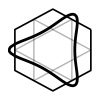
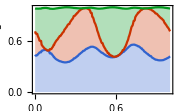

```mathematica
Block[{ϵ1=1.8,ϵ2=2,v1=1.6,v2=0.8,n=3,heff,vx,vy,Ek,ks,ψs,ρ,obs,ws},
heff[{kx_,ky_}]:=ArrayFlatten[{{ϵ1 PauliMatrix[1],v1(kx PauliMatrix[1]-ky PauliMatrix[2]),v1(kx PauliMatrix[2]+ky PauliMatrix[1])},{v1(kx PauliMatrix[1]-ky PauliMatrix[2]),ϵ2 PauliMatrix[0]+v2(kx PauliMatrix[1]+ky PauliMatrix[2]),0},{v1(kx PauliMatrix[2]+ky PauliMatrix[1]),0,-ϵ2 PauliMatrix[0]+v2(kx PauliMatrix[1]+ky PauliMatrix[2])}}];
vx=ArrayFlatten[{{0,v1 PauliMatrix[1],v1 PauliMatrix[2]},{v1 PauliMatrix[1],v2 PauliMatrix[1],0},{v1 PauliMatrix[2],0,v2 PauliMatrix[1]}}];
vy=ArrayFlatten[{{0,-v1 PauliMatrix[2],v1 PauliMatrix[1]},{-v1 PauliMatrix[2],v2 PauliMatrix[2],0},{v1 PauliMatrix[1],0,v2 PauliMatrix[2]}}];
Ek[k:{_?NumericQ,_?NumericQ}]:=Sort[Eigenvalues@heff[k]]⟦n⟧;
ks=First@Cases[ContourPlot[Ek[{kx,ky}]==-1.1,{kx,-2,2},{ky,-2,2},PlotRange->All,MaxRecursion->3,PlotPoints->5],GraphicsComplex[pts_,___]:>pts,∞];
ψs=Last@SortBy[Thread@Eigensystem@heff[#],First]⟦n⟧&/@ks;
ρ=(Transpose[ψs].Conjugate[ψs])/Length[ks];
obs=Last/@Reverse[SortBy[Thread@Eigensystem@ρ,First]]⟦;;3⟧;
ws=Abs[Conjugate[ψs].Transpose[obs]]^2;
Row@{Graphics[{{EdgeForm[AbsoluteThickness[1.2]],White,Polygon[CirclePoints[{1,π/6},6]]},{AbsoluteThickness[1],Opacity[0.3],Line[Append[#,First@#]]&@CirclePoints[{Sqrt[3]/2,#},3]&/@{0,π}},{AbsoluteThickness[2],Line[ks/Min[Norm/@ks]/2,VertexColors->RGBColor/@ws]}},ImageSize->{100,100}],
ListLinePlot[Thread@(Accumulate/@ws),Filling->{1->Axis,2->{1},3->{2}},DataRange->{0,1},FrameLabel->{"FS parameter","orbital weight"},ImageSize->180]}
]
```

If we project the Fermi surface states to the three leading orbitals, the total fidelity remains high (>0.95) along the Fermi surface

The orbital on Fermi surface is dominated by one component. Therefore it is justified to further simplify the model to a single orbital.

#### Around K_M Point

Collect the wave functions around K_M point (two frames are taken from upper and lower bands respectively)

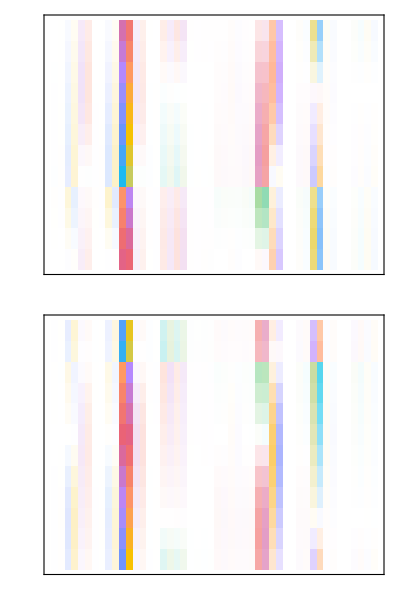

```mathematica
Block[{R=3,θ=1.08°,w0,w1,Q,Ks,ind,NK,σv,qs,T,h0,h1,h},
{w0,w1}=2.5{0.11,-0.12};
Q={{Sqrt[3],3},{-Sqrt[3],3}}/2;
Ks=Association[#->DeleteCases[Table[#+l.Q,{l,Tuples[Range[-#,#]&@Ceiling[2R/3],2]}]&[{-Sqrt[3],#}/2],k_/;Norm[N@k]-R>0.0001]&/@{1,-1}];
ind=AssociationThread[#->Range@Length@#]&[Join@@Ks];
NK=Length@ind;
σv[φ_,i_]:=Block[{U},
U=MatrixExp[ⅈ φ PauliMatrix[3]/2];
ConjugateTranspose[U].PauliMatrix[i].U];
h0[k:{_,_}]:=Sum[KroneckerProduct[SparseArray[ind/@{#,#}->-(k-#)⟦i⟧&/@Ks[s],{NK,NK}],σv[s θ/2,i]],{s,{1,-1}},{i,{1,2}}];
qs=RotationMatrix[# 2π/3].{0,-1}&/@{0,1,2};
T=AssociationThread[qs->(w0 σv[# 2π/3,0]+w1 σv[# 2π/3,1]&/@{0,1,2})];
h1=Sum[KroneckerProduct[SparseArray[DeleteCases[ind/@{#,#+q}->1&/@Ks[1],{_,_Missing}->_],{NK,NK}],T[q]],{q,qs}];
h1=h1+ConjugateTranspose[h1];
h[k_]:=h0[k]+h1;
Block[{u,K0={-Sqrt[3],1}/2,k0=0.2,dϕ=π/6,zs},
u[k:{_?NumericQ,_?NumericQ}]:=Block[{hk,eigs,n},
hk=h[k];
n=Length@hk;
eigs=SortBy[First]@Thread@Eigensystem@hk;
#/Sign[Mean@#]&/@eigs⟦n/2;;n/2+1,2⟧];
zs=Exp[ⅈ Range[dϕ,2π,dϕ]];
Column[ComplexMatrixPlot[#,PlotRangePadding->None,FrameStyle->Black,FrameTicks->None,ImageSize->160]&/@Thread[u[ReIm@#+K0]&/@(k0 zs)],Spacings->0.1]]]
```

Construct and diagonalize the density matrix

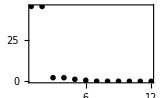

```mathematica
Block[{R=3,θ=1.08°,w0,w1,Q,Ks,ind,NK,σv,qs,T,h0,h1,h},
{w0,w1}=2.5{0.11,-0.12};
Q={{Sqrt[3],3},{-Sqrt[3],3}}/2;
Ks=Association[#->DeleteCases[Table[#+l.Q,{l,Tuples[Range[-#,#]&@Ceiling[2R/3],2]}]&[{-Sqrt[3],#}/2],k_/;Norm[N@k]-R>0.0001]&/@{1,-1}];
ind=AssociationThread[#->Range@Length@#]&[Join@@Ks];
NK=Length@ind;
σv[φ_,i_]:=Block[{U},
U=MatrixExp[ⅈ φ PauliMatrix[3]/2];
ConjugateTranspose[U].PauliMatrix[i].U];
h0[k:{_,_}]:=Sum[KroneckerProduct[SparseArray[ind/@{#,#}->-(k-#)⟦i⟧&/@Ks[s],{NK,NK}],σv[s θ/2,i]],{s,{1,-1}},{i,{1,2}}];
qs=RotationMatrix[# 2π/3].{0,-1}&/@{0,1,2};
T=AssociationThread[qs->(w0 σv[# 2π/3,0]+w1 σv[# 2π/3,1]&/@{0,1,2})];
h1=Sum[KroneckerProduct[SparseArray[DeleteCases[ind/@{#,#+q}->1&/@Ks[1],{_,_Missing}->_],{NK,NK}],T[q]],{q,qs}];
h1=h1+ConjugateTranspose[h1];
h[k_]:=h0[k]+h1;
Block[{u,K0={-Sqrt[3],1}/2,k0=0.3,dϕ=π/24,zs,ρ},
u[k:{_?NumericQ,_?NumericQ}]:=Block[{hk,eigs,n},
hk=h[k];
n=Length@hk;
eigs=SortBy[First]@Thread@Eigensystem@hk;
#/Sign[Mean@#]&/@eigs⟦n/2;;n/2+1,2⟧];
zs=Exp[ⅈ Range[dϕ,2π,dϕ]];
ρ=Total[Conjugate[#]⊗#&/@Flatten[u[ReIm@#+K0]&/@(k0 zs),1]];
ListPlot[Eigenvalues[ρ]⟦;;12⟧,PlotRange->All,PlotStyle->Black,FrameLabel->{"orbital","weight"},ImageSize->160]]]
```

There are only 2 leading orbitals, which are just the original A/B sublattice orbitals at each valley.

The pocket model in this case can be just trivially given by the k.p expansion around the valley.

h_(K,eff)(k)=ϵ_K σ^0+v k·σ.

### Pocket Model (Single-orbit)

#### Band Dispersion

We can diagonalize the 6-orbital model in Eq. (DisplayFormulaNumbered) and expand the band dispersion around Γ point for the two bands near the neutrality,

the upper band

ϵ_+(k)=+ϵ_1-(2 ϵ_1 v_1^2)/(ϵ_2^2-ϵ_1^2)k^2+(4 ϵ_1 ϵ_2 v_1^2 v_2)/((ϵ_2^2-ϵ_1^2)^2)(k_x^3-3 k_x k_y^2)+…

```mathematica
Block[{heff,es},
heff[{kx_,ky_}]:=ArrayFlatten[{{ϵ1 PauliMatrix[1],v1(kx PauliMatrix[1]-ky PauliMatrix[2]),v1(kx PauliMatrix[2]+ky PauliMatrix[1])},{v1(kx PauliMatrix[1]-ky PauliMatrix[2]),ϵ2 PauliMatrix[0]+v2(kx PauliMatrix[1]+ky PauliMatrix[2]),0},{v1(kx PauliMatrix[2]+ky PauliMatrix[1]),0,-ϵ2 PauliMatrix[0]+v2(kx PauliMatrix[1]+ky PauliMatrix[2])}}];
es=Eigenvalues@heff[{kx,ky}];
Simplify[Normal@Series[es⟦-1⟧/.{kx->k kx,ky->k ky},{k,0,3}]/.k->1]]
```

Root::sbr: Because of branch cuts, the series may represent a different root of -k^4 kx^4 v2^4 ϵ1^2-2 k^4 kx^2 ky^2 v2^4 ϵ1^2-k^4 ky^4 v2^4 ϵ1^2+«6»+(-4 k^2 kx^2 v1^2-4 k^2 ky^2 v1^2-2 k^2 kx^2 v2^2-2 k^2 ky^2 v2^2-ϵ1^2-2 ϵ2^2) #1^4+#1^6& for some values of {kx,ky,v1,v2,ϵ1,ϵ2,k}.

ϵ1+(4 kx (kx^2-3 ky^2) v1^2 v2 ϵ1 ϵ2)/((ϵ1^2-ϵ2^2)^2)+(2 (kx^2+ky^2) v1^2 ϵ1)/(ϵ1^2-ϵ2^2)

Expansion

the lower band

ϵ_-(k)=-ϵ_1+(2 ϵ_1 v_1^2)/(ϵ_2^2-ϵ_1^2)k^2+(4 ϵ_1 ϵ_2 v_1^2 v_2)/((ϵ_2^2-ϵ_1^2)^2)(k_x^3-3 k_x k_y^2)+…

```mathematica
Block[{heff,es},
heff[{kx_,ky_}]:=ArrayFlatten[{{ϵ1 PauliMatrix[1],v1(kx PauliMatrix[1]-ky PauliMatrix[2]),v1(kx PauliMatrix[2]+ky PauliMatrix[1])},{v1(kx PauliMatrix[1]-ky PauliMatrix[2]),ϵ2 PauliMatrix[0]+v2(kx PauliMatrix[1]+ky PauliMatrix[2]),0},{v1(kx PauliMatrix[2]+ky PauliMatrix[1]),0,-ϵ2 PauliMatrix[0]+v2(kx PauliMatrix[1]+ky PauliMatrix[2])}}];
es=Eigenvalues@heff[{kx,ky}];
Simplify[Normal@Series[es⟦1⟧/.{kx->k kx,ky->k ky},{k,0,3}]/.k->1]]
```

Root::sbr: Because of branch cuts, the series may represent a different root of -k^4 kx^4 v2^4 ϵ1^2-2 k^4 kx^2 ky^2 v2^4 ϵ1^2-k^4 ky^4 v2^4 ϵ1^2+«6»+(-4 k^2 kx^2 v1^2-4 k^2 ky^2 v1^2-2 k^2 kx^2 v2^2-2 k^2 ky^2 v2^2-ϵ1^2-2 ϵ2^2) #1^4+#1^6& for some values of {kx,ky,v1,v2,ϵ1,ϵ2,k}.

ϵ1 (-1+(4 kx (kx^2-3 ky^2) v1^2 v2 ϵ2)/((ϵ1^2-ϵ2^2)^2)-(2 (kx^2+ky^2) v1^2)/(ϵ1^2-ϵ2^2))

Expansion

The coefficients of the Re k_+^3 term remains positive in both bands.

If we just focus on a single band, we can simply consider

h_k=k^2-μ+α Re k_+^3.

k_+≡k_x+ⅈ k_y is the complex momentum.

α - anisotropy parameter, e.g. α=1/3

μ - chemical potential, e.g. μ=1(rounded), μ=4/3 (straight).

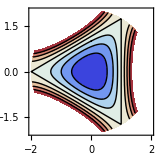

```mathematica
ContourPlot[(kx^2+ky^2)+(1/3)Re[(kx+ⅈ ky)^3],{kx,-2,2},{ky,-2,2},PlotRange->{0,8/3},Contours->Range[0,8/3,1/3],FrameLabel->{"\!\(k\_x\)","\!\(k\_y\)"},RegionFunction-> (Norm[{#1,#2}]≤2&),ContourStyle->Directive[AbsoluteThickness[1],Opacity[1]],ImageSize->160]
```

The model is only valid within the momentum range Λ=2/(3α).

##### Field Theory Approach

An alternative approach to derive the effective theory is to integrate out the high energy fermions

```mathematica
Block[{heff,es},
heff[{kx_,ky_}]:=ArrayFlatten[{{ϵ1 PauliMatrix[1],v1(kx PauliMatrix[0]-ⅈ ky PauliMatrix[3]),v1(kx PauliMatrix[0]-ⅈ ky PauliMatrix[3])},{v1(kx PauliMatrix[0]+ⅈ ky PauliMatrix[3]),ϵ2 PauliMatrix[0]+v2(kx PauliMatrix[1]+ky PauliMatrix[2]),0},{v1(kx PauliMatrix[0]+ⅈ ky PauliMatrix[3]),0,-ϵ2 PauliMatrix[0]-v2(kx PauliMatrix[1]+ky PauliMatrix[2])}}];
Block[{h,a,b,c,d,G0,Σ0,Σ,H},
h=heff[k{kx,ky}];
a=h⟦1;;2,1;;2⟧;
b=h⟦3;;6,1;;2⟧;
c=h⟦1;;2,3;;6⟧;
d=h⟦3;;6,3;;6⟧;
G0=Simplify@Inverse[ω IdentityMatrix[6]-ArrayFlatten[{{a,0},{0,d}}]];
Σ0=ArrayFlatten[{{0,c},{b,0}}];
Σ=Simplify[Σ0+Σ0.G0.Σ0]⟦1;;2,1;;2⟧;
H=Collect[Abstract[a+Σ],_σ,Simplify];
Simplify@Series[H,{k,0,3}]
]]
```

ϵ1 σ[1]+(2 (kx-ⅈ ky) (kx+ⅈ ky) v1^2 ω σ[0] k^2)/((-ϵ2+ω) (ϵ2+ω))+(4 v1^2 v2 ϵ2 ω (kx^3 σ[1]-3 kx ky^2 σ[1]+3 kx^2 ky σ[2]-ky^3 σ[2]) k^3)/((ϵ2-ω)^2 (ϵ2+ω)^2)+O[k]^4

```mathematica
σ[1]·σPower[kx σ[0]+ⅈ ky σ[3],3]//Expand
```

kx^3 σ[1]-3 kx ky^2 σ[1]+3 kx^2 ky σ[2]-ky^3 σ[2]

#### Quantum Oscillation

From Eq. (DisplayFormulaNumbered), the velocity at k is given by

v=∂_k h_k=(2 k_x+3α(k_x^2-k_y^2)
2 k_y-6α k_x k_y).

```mathematica
D[kx^2+ky^2-μ+α (kx^3-3kx ky^2),#]&/@{kx,ky}//Expand
```

{2 kx+3 kx^2 α-3 ky^2 α,2 ky-6 kx ky α}

Derivative.

The cyclotron motion is described by k̇=-v×B (assuming B=(0,0,B) is perpendicular to the graphene plane)

ⅆ/ⅆt(k_x
k_y)=B(-2 k_y+6α k_x k_y
2 k_x+3α(k_x^2-k_y^2)).

Initial condition: k_x^2-μ+α k_x^3=0, k_y=0.

Fermi surface density of state (FSDOS) is proportional to the inverse velocity (|v|)^-1 (peaks at turning corners of the triangular FS).

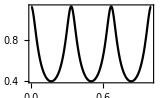

```mathematica
Block[{α=1/3,μ=1,v,k},
v[{kx_,ky_}]:={2kx+3α(kx^2-ky^2),2ky-6α kx ky};
k=FSOrbit[α,μ];
Block[{t0,t1},
{{t0,t1}}=k@"Domain";
Plot[1/Norm@v[k[t0+λ(t1-t0)]],{λ,0,1},PlotRange->{0,All},PlotStyle->Black,FrameLabel->{"FS parameter","FSDOS"},ImageSize->160]]]
```

Fermi Surface Orbit

```mathematica
FSOrbit[α_,μ_]:=Block[{h,f,k},
h[{kx_,ky_}]:=kx^2+ky^2+α(kx^3-3kx ky^2);
f[{kx_,ky_}]:={-2ky+6α kx ky,2kx+3α(kx^2-ky^2)};
Block[{τ=20,k0,r,c=False},
k0=Block[{sol,x},sol=NSolve[{h[{x,0}]==μ,x<0},x,Reals];
If[Length@sol==0,Return[{{0,∞}}&],Max[x/.sol]]];
r[{kx_,ky_}]:=kx<0.&&ky<0.;
NDSolveValue[{k'[t]==f[k[t]],k[0]=={k0,0},
WhenEvent[!r[k[t]],c=True],WhenEvent[r[k[t]]&&c,"StopIntegration"]},
k,{t,0,τ},StartingStepSize->0.01,Method->{"FixedStep",Method->{"ImplicitRungeKutta","Coefficients"->"ImplicitRungeKuttaGaussCoefficients","DifferenceOrder"->2,"ImplicitSolver"->{"FixedPoint","AccuracyGoal"->MachinePrecision,"PrecisionGoal"->MachinePrecision,"IterationSafetyFactor"->1}}}]]];
```

#### Assembling Valleys

Putting together both valley degrees of freedom, we consider the basis

c_k=(c_Kk
c_(K' k)).

We can write down the pocket model

H=∑_k c_k^†(β_k σ^0+α_k σ^3)c_k,
β_k=k^2-μ,
α_k=α Re k_+^3.

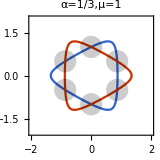

```mathematica
Block[{α=1/3,μ=1},ContourPlot[{(kx^2+ky^2)-μ+α Re[(kx+ⅈ ky)^3],(kx^2+ky^2)-μ-α Re[(kx+ⅈ ky)^3]},{kx,-2,2},{ky,-2,2},FrameLabel->{"\!\(k\_x\)","\!\(k\_y\)"},ContourStyle->Directive[Opacity[1]],ContourLabels->None,PlotLabel->"\!\(α="<>ToString[InputForm@α]<>",μ="<>ToString[InputForm@μ]<>"\)",Epilog->{{Opacity[0.2],PointSize[0.1],Point@CirclePoints[{Sqrt[μ],π/6},6]}},ImageSize->160]]
```

Fermi surfaces between K and K' valleys are approximately nested.

The six hot spots are of momentum k=μ^(1/2) from the Γ_M point.

In the action formalism,

S=∑_k c_k^†(-(ⅈ ω-β_k)σ^0+α_k σ^3)c_k,

Fermion bare propagator

G_0(k)=((ⅈ ω-β_k)σ^0-α_k σ^3)^-1
=1/2∑_(ϛ=±) (σ^0+ϛ σ^3)/(ⅈ ω-(β_k+ϛ α_k)).

```mathematica
σInverse[Sum[(σ[0]+ϛ σ[3])/(iω-(β+ϛ α)),{ϛ,{-1,1}}]/2]
```

(iω-β) σ[0]-α σ[3]

Verification.

#### Charging Interaction

We start with the Wannier orbital. On each site of the honeycomb super-lattice, there are two Wannier orbitals, given by

c_(i±)=c_iK±ⅈ c_(i K'),

So the on-site density operator is

n_i=c_(i++)^†c_(i++)+c_(i+-)^†c_(i+-)=c_iK^†c_iK+c_(i K')^†c_(i K').

If we introduce c_i=(c_iK,c_(i K'))ᵀ, we simply have

n_i=c_i^†σ^0 c_i.

The super-lattice density operator just treats the valley as an internal freedom.

The interaction can be modeled by the charging energy

H_int=U∑_ (1/6∑_(i∈) n_i-1)^2.

In the momentum space,

H_int=∑_(k,k',q) U(q)c_(k+q)^†σ^0 c_k c_(k'+q)^†σ^0 c_k'.

U(q) is given by (r_i are the positions of the six sites around a plaquette on the honeycomb super-lattice)

U(q)=(1/6∑_(i∈) e^(ⅈ q·r_i))^2.

```mathematica
Block[{U},
U[q:{_,_}]:=(Total[Exp[ⅈ 4π/(3Sqrt[3])q.#]&/@CirclePoints[6]]/6)^2;
Show[Plot3D[U[{qx,qy}],{qx,-Sqrt[3],Sqrt[3]},{qy,-3/2,3/2},MeshFunctions->{#3&},MeshStyle->AbsoluteThickness[1],ColorFunction->"Rainbow",AxesLabel->{"\!\(q\_x\)","\!\(q\_y\)","\!\(U(q)\)"},Boxed->All,AspectRatio->Automatic,PlotRange->{0,1},ImageSize->200],
Graphics3D[Table[Translate[{GraphicsComplex[Append[#,1]&/@CirclePoints[{1,π/6},6],{AbsoluteThickness[1],Line[{1,2,3,4,5,6,1}]}]},{a,b}.{{Sqrt[3],3,0},{-Sqrt[3],3,0}}/2],{a,-1,1},{b,-1,1}]]]]
```

-Graphics3D-

For simplicity, we may approximate U(q) by a constant U_0>0 (fall back to on-site interaction).

#### Symmetry Analysis

Let us include the spin degrees of freedom and switch to the Majorana basis

χ=(K
K')⊗(↑
↓)⊗(Re
Im).

The Hamiltonian reads

H=H_band+H_int,
H_band=1/2∑_k χ_-k ᵀ(β_k σ^002+α_k σ^300)χ_k,
H_int=U∑_i (χ_i σ^002 χ_i)^2.

In the absence of the FS anisotropy α, the Hamiltonian has the U(4) symmetry generated by σ^(ab*) (where *=0,2 to make the generator antisymmetric)

With the FS anisotropy α, the U(4) symmetry is broken down to (U(1))_c×(U(1))_v×SO(4), generated by

(U(1))_c:σ^002;
(U(1))_v:σ^302;
SO(4)≃SU(2)_K×(SU(2))_K':σ^012,σ^020,σ^032;σ^312,σ^320,σ^332.

Symmetry hierarchy

U(4) |  |  | 
(U(1))_c | SU(4)≃SO(6) |  | 
 | (U(1))_v | SO(4) | 
 |  | (SU(2))_K | (SU(2))_K'

Given the 8 dimensional space of the Majorana fermion in Eq. (DisplayFormulaNumbered), there are in total 28 fermion bilinear operators. They can be classified by the symmetries:

(U(1))_c | SU(4) | (U(1))_v | SO(4) | operator |  | order
16_0 | 1_sc | 1_0 | 1_sc | n_c | σ^002 | charge density
 | 15_ad | 7_0 | 1_ps | n_v | σ^302 | valley density
 |  |  | 6_ad | S_K
S_K' | σ^012,σ^020,σ^032,
σ^312,σ^320,σ^332 | spin×(valley 
FM/AFM)
 |  | 8_2 | 4_ve | I_x^μ | σ^102,σ^210,σ^222,σ^230 | VDW_x×(charge,spin)
 |  |  | 4_pv | I_y^μ | -σ^200,σ^112,σ^120,σ^132 | VDW_y×(charge,spin)
12_2 | 6_ve | 4_0 | 4_ve | Re Δ^μ | σ^123,σ^231,σ^203,σ^211 | Re inter-valley SC
 |  | 2_2 | 1_sc | ReΔ_K
Δ_K' | σ^021 | Re intra-valley SC
 |  |  | 1_ps |  | σ^323 | 
 | 6_pv | 4_0 | 4_pv | Im Δ^μ | σ^121,σ^233,σ^201,σ^213 | Im inter-valley SC
 |  | 2_2 | 1_sc | ImΔ_K
Δ_K' | σ^023 | Im intra-valley SC
 |  |  | 1_ps |  | -σ^321 |

#### Generic Symmetric Interaction

The generic (local) interaction that preserves the (U(1))_c×(U(1))_v×SO(4) and ℤ_2^T symmetry takes the form of

H_int=g_c/2 n_c^2-g_v/2 n_v^2-g_S/6(S_K^2+S_K'^2)-g_I/8(I_x^μ I_x^μ+I_y^μ I_y^μ)+g_Δ0/8 Δ^(μ†)Δ^μ+g_Δ1/4(Δ_K^†Δ_K+Δ_K'^†Δ_K').

However these interaction terms are not linearly independent, they can all be written in terms of density-density interaction (up to constant energy shift)

1/2 n_c^2=(n_(K↑)+n_(K↓))(n_(K'↑)+n_(K'↓))+(n_(K↑)n_(K↓)+n_(K'↑)n_(K'↓)),
-1/2 n_v^2=(n_(K↑)+n_(K↓))(n_(K'↑)+n_(K'↓))-(n_(K↑)n_(K↓)+n_(K'↑)n_(K'↓)),
-1/6(S_K^2+S_K'^2)=(n_(K↑)n_(K↓)+n_(K'↑)n_(K'↓)),
-1/8(I_x^μ I_x^μ+I_y^μ I_y^μ)=(n_(K↑)+n_(K↓))(n_(K'↑)+n_(K'↓)),
1/8 Δ^(μ†)Δ^μ=(n_(K↑)+n_(K↓))(n_(K'↑)+n_(K'↓)),
1/4(Δ_K^†Δ_K+Δ_K'^†Δ_K')=(n_(K↑)n_(K↓)+n_(K'↑)n_(K'↓)).

```mathematica
Block[{nc,nv,Ss,Ix,Iy,Re0,Rep,Rem,Im0,Imp,Imm,χ,rep,int,Vs},
nc={σ[0,0,2]};
nv={σ[3,0,2]};
Ss={σ[0,1,2],σ[0,2,0],σ[0,3,2],σ[3,1,2],σ[3,2,0],σ[3,3,2]};
Ix={σ[1,0,2],σ[2,1,0],σ[2,2,2],σ[2,3,0]};
Iy={-σ[2,0,0],σ[1,1,2],σ[1,2,0],σ[1,3,2]};
Re0={σ[1,2,3],σ[2,3,1],σ[2,0,3],σ[2,1,1]};
Rep={σ[0,2,1]};
Rem={σ[3,2,3]};
Im0={σ[1,2,1],σ[2,3,3],σ[2,0,1],σ[2,1,3]};
Imp={σ[0,2,3]};
Imm={-σ[3,2,1]};
χ=AssociationThread[Range@Length@#->#]&@Cl[8];
rep[a_]:=Total[#2/2 CenterDot@@χ/@#1&@@@Most@ArrayRules@Represent@a];
int[A_,B_]:=Total[#1·#2&@@@Thread@{rep/@A,rep/@B}];
Vs=Expand@{1/2int[nc,nc],-1/2int[nv,nv],-1/12int[Ss,Ss],-1/8(int[Ix,Ix]+int[Iy,Iy]),1/8(int[Re0,Re0]+int[Im0,Im0]),1/8(int[Rep,Rep]+int[Imp,Imp]+int[Rem,Rem]+int[Imm,Imm])};
Factor[Vs/.{σ[0,0,0,0]->0,σ[3,3,0,0]->Subscript[n, "K↑"] Subscript[n, "K↓"],σ[0,0,3,3]->Subscript[n, "K'↑"] Subscript[n, "K'↓"],σ[3,0,3,0]->Subscript[n, "K↑"] Subscript[n, "K'↑"],σ[0,3,0,3]->Subscript[n, "K↓"] Subscript[n, "K'↓"],σ[3,0,0,3]->Subscript[n, "K↑"] Subscript[n, "K'↓"],σ[0,3,3,0]->Subscript[n, "K↓"] Subscript[n, "K'↑"],σ[3,0,0,0]->Subscript[n, "K↑"],σ[0,3,0,0]->Subscript[n, "K↓"],σ[0,0,3,0]->Subscript[n, "K'↑"],σ[0,0,0,3]->Subscript[n, "K'↓"]}]]
```

{n_(K'↓) n_(K↓)+n_(K'↓) n_(K'↑)+n_(K↓) n_(K'↑)+n_(K'↓) n_(K↑)+n_(K↓) n_(K↑)+n_(K'↑) n_(K↑),n_(K'↓) n_(K↓)-n_(K'↓) n_(K'↑)+n_(K↓) n_(K'↑)+n_(K'↓) n_(K↑)-n_(K↓) n_(K↑)+n_(K'↑) n_(K↑),n_(K'↓) n_(K'↑)+n_(K↓) n_(K↑),(n_(K'↓)+n_(K'↑)) (n_(K↓)+n_(K↑)),(n_(K'↓)+n_(K'↑)) (n_(K↓)+n_(K↑)),n_(K'↓) n_(K'↑)+n_(K↓) n_(K↑)}

Details.

```mathematica
Block[{nc,nv,Ss,Ix,Iy,Re0,Rep,Rem,Im0,Imp,Imm,χ,rep,int,Vs},
nc={σ[0,0,2]};
nv={σ[3,0,2]};
Ss={σ[0,1,2],σ[0,2,0],σ[0,3,2],σ[3,1,2],σ[3,2,0],σ[3,3,2]};
Ix={σ[1,0,2],σ[2,1,0],σ[2,2,2],σ[2,3,0]};
Iy={-σ[2,0,0],σ[1,1,2],σ[1,2,0],σ[1,3,2]};
Re0={σ[1,2,3],σ[2,3,1],σ[2,0,3],σ[2,1,1]};
Rep={σ[0,2,1]};
Rem={σ[3,2,3]};
Im0={σ[1,2,1],σ[2,3,3],σ[2,0,1],σ[2,1,3]};
Imp={σ[0,2,3]};
Imm={-σ[3,2,1]};
χ=AssociationThread[Range@Length@#->#]&@Cl[8];
(*not χᵀχ/2 but χᵀχ/4 because χ=c/sqrt(2)*)
rep[a_]:=Total[#2/4 CenterDot@@χ/@#1&@@@Most@ArrayRules@Represent@a];
int[A_,B_]:=Total[#1·#2&@@@Thread@{rep/@A,rep/@B}];
Vs=Expand@{1/2int[nc,nc],-1/2int[nv,nv],-1/12int[Ss,Ss],-1/8(int[Ix,Ix]+int[Iy,Iy]),1/8(int[Re0,Re0]+int[Im0,Im0]),1/8(int[Rep,Rep]+int[Imp,Imp]+int[Rem,Rem]+int[Imm,Imm])};
Factor[Vs/.{σ[0,0,0,0]->0,σ[3,3,0,0]->4 Subscript[n, "K↑"] Subscript[n, "K↓"],σ[0,0,3,3]->4 Subscript[n, "K'↑"] Subscript[n, "K'↓"],σ[3,0,3,0]->4 Subscript[n, "K↑"] Subscript[n, "K'↑"],σ[0,3,0,3]->4 Subscript[n, "K↓"] Subscript[n, "K'↓"],σ[3,0,0,3]->4 Subscript[n, "K↑"] Subscript[n, "K'↓"],σ[0,3,3,0]->4 Subscript[n, "K↓"] Subscript[n, "K'↑"],σ[3,0,0,0]->2 Subscript[n, "K↑"],σ[0,3,0,0]->2 Subscript[n, "K↓"],σ[0,0,3,0]->2 Subscript[n, "K'↑"],σ[0,0,0,3]->2 Subscript[n, "K'↓"]}]]
```

{n_(K'↓) n_(K↓)+n_(K'↓) n_(K'↑)+n_(K↓) n_(K'↑)+n_(K'↓) n_(K↑)+n_(K↓) n_(K↑)+n_(K'↑) n_(K↑),n_(K'↓) n_(K↓)-n_(K'↓) n_(K'↑)+n_(K↓) n_(K'↑)+n_(K'↓) n_(K↑)-n_(K↓) n_(K↑)+n_(K'↑) n_(K↑),n_(K'↓) n_(K'↑)+n_(K↓) n_(K↑),(n_(K'↓)+n_(K'↑)) (n_(K↓)+n_(K↑)),(n_(K'↓)+n_(K'↑)) (n_(K↓)+n_(K↑)),n_(K'↓) n_(K'↑)+n_(K↓) n_(K↑)}

Fix the factor.

There are only two independent interactions

H_int=U_0(n_(K↑)+n_(K↓))(n_(K'↑)+n_(K'↓))+U_1(n_(K↑)n_(K↓)+n_(K'↑)n_(K'↓)),

where U_0=g_c+g_v+g_I+g_Δ0 and U_1=g_c-g_v+g_S+g_Δ1.

Decoupling

Decoupling the interaction in the pairing channel

```mathematica
Block[{nc,nv,Ss,Ix,Iy,Re0,Rep,Rem,Im0,Imp,Imm,coll,χ,rep,c,reph,repp,σRe,σIm},
nc={σ[0,0,2]};
nv={σ[3,0,2]};
Ss={σ[0,1,2],σ[0,2,0],σ[0,3,2],σ[3,1,2],σ[3,2,0],σ[3,3,2]};
Ix={σ[1,0,2],σ[2,1,0],σ[2,2,2],σ[2,3,0]};
Iy={-σ[2,0,0],σ[1,1,2],σ[1,2,0],σ[1,3,2]};
Re0={σ[1,2,3],σ[2,3,1],σ[2,0,3],σ[2,1,1]};
Rep={σ[0,2,1]};
Rem={σ[3,2,3]};
Im0={σ[1,2,1],σ[2,3,3],σ[2,0,1],σ[2,1,3]};
Imp={σ[0,2,3]};
Imm={-σ[3,2,1]};
coll[a_]:=Collect[a,_σ];
χ=AssociationThread[Range@Length@#->#]&@Cl[8];
rep[a_]:=Total[#2/2 CenterDot@@χ/@#1&@@@Most@ArrayRules@Represent@a];
c=Association[#->(χ[2#-1]-ⅈ χ[2#])/Sqrt[2]&/@Range[Length[χ]/2]];
reph[a_]:=Total[#2σHermitian[c[#1⟦1⟧]]·c[#1⟦2⟧]&@@@Most@ArrayRules@Represent@a];
repp[a_]:=Total[#2c[#1⟦1⟧]·c[#1⟦2⟧]&@@@Most@ArrayRules@Represent@a];
σRe[a_]:=(a+σHermitian[a])/2;
σIm[a_]:=(a-σHermitian[a])/(2ⅈ);
Block[{V1,V2},
V1=Represent[(σ[1,0,1,0]+σ[2,1,2,1]+σ[2,2,2,2]+σ[2,3,2,3]+σ[2,0,2,0]+σ[1,1,1,1]+σ[1,2,1,2]+σ[1,3,1,3])];
V2=Represent[ⅈ(-σ[1,0,2,0]+σ[2,1,1,1]+σ[2,2,1,2]+σ[2,3,1,3]+σ[2,0,1,0]-σ[1,1,2,1]-σ[1,2,2,2]-σ[1,3,2,3])];
ArrayRules@SparseArray@ArrayReshape[V1-V2,{4,4,4,4}]]
]
```

{{3,1,1,3}→8,{3,2,2,3}→8,{4,1,1,4}→8,{4,2,2,4}→8,{_,_,_,_}→0}

#### Susceptibility

General bare susceptibility

χ_0^AB(q)=⟨c_(k'-q)^†σ^A c_k' c_(k+q)^†σ^B c_k⟩_0
=-Tr G_0(k)σ^A G_0(k+q)σ^B,

where σ^A can be any of the 28 fermion bilinear operators. Substitute Eq. (DisplayFormulaNumbered) to Eq. (DisplayFormulaNumbered), the zero frequency (static) susceptibility is given by

χ_0^AB(q)=1/4∑_(ϛ_(1,2)=±) η_(ϛ_1 ϛ_2)^AB f_(ϛ_1 ϛ_2)(q),
 η_(ϛ_1 ϛ_2)^AB=Tr(σ^002+ϛ_1 σ^300)σ^A(σ^002+ϛ_2 σ^300)σ^B,
f_(ϛ_1 ϛ_2)(q)=∑_k ((Θ(β_(k+q)+ϛ_2 α_(k+q))-Θ(β_k+ϛ_1 α_k))/((β_(k+q)+ϛ_2 α_(k+q))-(β_k+ϛ_1 α_k))).

The form factor f_(ϛ_1 ϛ_2) has the general structure

f_(++)(q)=f_(--)(q)=f_0(q)/2,
f_(-+)(q)=(f_1(q)+f_2(q))/2,
f_(+-)(q)=(f_1(q)-f_2(q))/2.

The bare susceptibility are summarized as

operator | χ_0/4 | U
n_c | f_0 | (U_0+U_1)/4
n_v | f_0 | (U_1-U_0)/4
(S_K,S_K') | (f_0 | 0
0 | f_0) | -U_1/12
(I_x^μ,I_y^μ) | (f_1 | ⅈ f_2
-ⅈ f_2 | f_1) | -U_0/8
Δ^μ | -f_0 | U_0/8
(Δ_K,Δ_K') | (-f_1 | ⅈ f_2
-ⅈ f_2 | -f_1) | U_1/8

```mathematica
Block[{nc,nv,Ss,Ix,Iy,Re0,Rep,Rem,Im0,Imp,Imm,χ,f,f0,f1,f2},
nc={σ[0,0,2]};
nv={σ[3,0,2]};
Ss={σ[0,1,2],σ[0,2,0],σ[0,3,2],σ[3,1,2],σ[3,2,0],σ[3,3,2]};
Ix={σ[1,0,2],σ[2,1,0],σ[2,2,2],σ[2,3,0]};
Iy={-σ[2,0,0],σ[1,1,2],σ[1,2,0],σ[1,3,2]};
Re0={σ[1,2,3],σ[2,3,1],σ[2,0,3],σ[2,1,1]};
Rep={σ[0,2,1]};
Rem={σ[3,2,3]};
Im0={σ[1,2,1],σ[2,3,3],σ[2,0,1],σ[2,1,3]};
Imp={σ[0,2,3]};
Imm={-σ[3,2,1]};
χ[A_,B_]:=Table[Sum[f[ϛ1,ϛ2]σTr[(σ[0,0,2]+ϛ1 σ[3,0,0])·a·(σ[0,0,2]+ϛ2 σ[3,0,0])·b],{ϛ1,{-1,1}},{ϛ2,{-1,1}}]/4,{a,A},{b,B}];
f[1,1]:=f0/2;
f[-1,-1]:=f0/2;
f[-1,1]:=(f1+f2)/2;
f[1,-1]:=(f1-f2)/2;
Simplify[χ[Imp,Imm]/4]]
```

{{-ⅈ f2}}

Susceptibility.

The RPA corrected interaction is

U_RPA=U/(1+U χ_0).

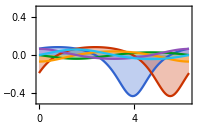

```mathematica
Block[{f0,f1,f2,χ,cols,ords},
Block[{fs,qs,gs,max},
{fs,qs}=FortranGet[FileNameJoin[{NotebookDirectory[],"Fortran","twopocket","data",#}]]&/@{"SS_10","QS_10"};
{f0,f1,f2}=Max/@Abs@Thread@fs];
χ[{U0_,U1_}]:=Min[Eigenvalues[#2 Inverse[IdentityMatrix[Dimensions@#1]+4 #2 #1]]]&@@@{{{{f0}},(U0+U1)/4},{{{f0}},(U1-U0)/4},{{{f0}},-U1/12},{{{f1,ⅈ f2},{-ⅈ f2,f1}},-U0/8},{{{-f0}},U0/8},{{{-f1,ⅈ f2},{-ⅈ f2,-f1}},U1/8}};
cols={Blue,Red,Green,Orange,Purple,Cyan};
ords="\!\("<>#<>"\)"&/@{"n\_c","n\_v","S","I","Δ\_0","Δ\_1"};
ListLinePlot[Thread@Table[χ[0.4ReIm[Exp[ⅈ θ]]],{θ,0,2π,π/48}],Filling->Axis,DataRange->{0,2π},PlotRange->{-0.5,0.5},PlotStyle->cols,PlotLegends->ords,FrameLabel->{"\!\(arg(U\_0,U\_1)\)","\!\(U\_RPA\)"},ImageSize->200]]
```

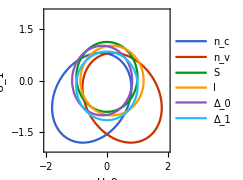

```mathematica
Block[{f0,f1,f2,χ,cols,ords},
Block[{fs,qs,gs,max},
{fs,qs}=FortranGet[FileNameJoin[{NotebookDirectory[],"Fortran","twopocket","data",#}]]&/@{"SS_10","QS_10"};
{f0,f1,f2}=Max/@Abs@Thread@fs];
χ[{U0_,U1_}]:=Min[Eigenvalues[#2 Inverse[IdentityMatrix[Dimensions@#1]+4 #2 #1]]]&@@@{{{{f0}},(U0+U1)/4},{{{f0}},(U1-U0)/4},{{{f0}},-U1/12},{{{f1,ⅈ f2},{-ⅈ f2,f1}},-U0/8},{{{-f0}},U0/8},{{{-f1,ⅈ f2},{-ⅈ f2,-f1}},U1/8}};
cols={Blue,Red,Green,Orange,Purple,Cyan};
ords="\!\("<>#<>"\)"&/@{"n\_c","n\_v","S","I","Δ\_0","Δ\_1"};
ListPolarPlot[Thread@Table[{θ,Exp[-5#]}&/@χ[0.25ReIm[Exp[ⅈ θ]]],{θ,0,2π,π/48}],Joined->True,PlotRange->2,PlotStyle->cols,PlotLegends->ords,FrameLabel->{"\!\(U\_0\)","\!\(U\_1\)"},ImageSize->180]]
```

When U_0=U_1>0, the strongest instability is in the valley density wave channel.

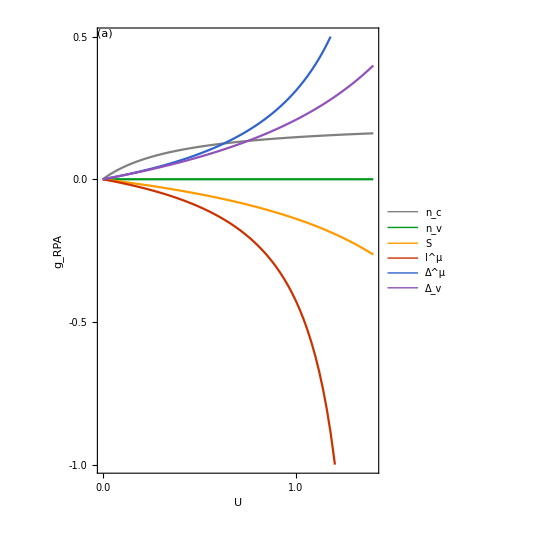
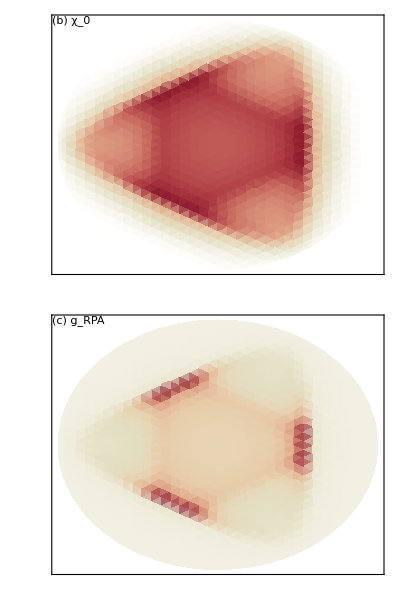
-Graphics- | -Graphics-

```mathematica
Grid[{{Block[{f0,f1,f2,χ,cols,ords},
Block[{fs,qs,gs,max},
{fs,qs}=FortranGet[FileNameJoin[{NotebookDirectory[],"Fortran","twopocket","data",#}]]&/@{"SS_10","QS_10"};
{f0,f1,f2}=Max/@Abs@Thread@fs];
χ[{U0_,U1_}]:=Min[Eigenvalues[#2 Inverse[IdentityMatrix[Dimensions@#1]+4 #2 #1]]]&@@@{{{{f0}},(U0+U1)/4},{{{f0}},(U1-U0)/4},{{{f0}},-U1/12},{{{f1,ⅈ f2},{-ⅈ f2,f1}},-U0/8},{{{-f0}},U0/8},{{{-f1,ⅈ f2},{-ⅈ f2,-f1}},U1/8}};
cols={Gray,Green,Orange,Red,Blue,Purple};
ords=Style["\!\("<>#<>"\)",12,SingleLetterItalics->True,FontFamily->"CMU"]&/@{"n\_c","n\_v","S\_v","\!\(I\^μ\)","Δ\^μ","Δ\_v"};
ListLinePlot[Thread@Table[{U,#}&/@χ[U{1,1.}],{U,0,1.4,0.02}],PlotStyle->cols,PlotRange->{-1,0.5},Axes->False,FrameLabel->{"\!\(U\)","\!\(g\_RPA\)"},FrameTicks->Block[{tk},
tk=Table[If[Mod[2x,1]==0,{x,NumberForm[x,{1,1}],{0.02,0}},{x,"",{0.01,0}}],{x,-1,2,0.1}];{{tk,None},{tk,None}}],Epilog->{Inset[Grid[Thread@{Graphics[{#,Line[{{0,0},{1,0}}]},AspectRatio->0.1,ImageSize->16]&/@cols,ords},Alignment->Left,Spacings->{0.2,0.1}],{0.3,-0.52}],Text["(a)",Scaled[{0,1}],{-1.5,1}]},BaselinePosition->Scaled[0.58],AspectRatio->1.4,ImageSize->{Automatic,200}]],
Block[{R=3.2,U0=0.7,fs,qs,gs,f,g,max},
{fs,qs}=FortranGet[FileNameJoin[{NotebookDirectory[],"Fortran","twopocket","data",#}]]&/@{"SS_10","QS_10"};
gs=Flatten[{U0/(1-U0#1),{U0-U0^2#2,U0^2#3}/(1-2U0#2+U0^2(#2^2-#3^2))}]&@@@fs;
f=fs.{0,1,1};
f=f/Max@Abs@Flatten@f;
g=gs.{0,1,1};
g=g/Max@Abs@Flatten@g;
Column[ListDensityPlot[MapThread[Append,{qs,Rescale[Chop[#1],{-1,1}]}],ColorFunctionScaling->False,PlotRange->{{-R,R},{-R,R},All},PlotRangeClipping->False,RegionFunction->(Norm[{#1,#2}]<R&),ImagePadding->{{15,2},{15,2}},Epilog->{Text[#2,Scaled[{0,1}],{-1.2,1}],Text["\!\(q\_x\)",{0,-3.8}],Text["\!\(q\_y\)",{-4.2,0},{0,0},{0,1}]},FrameTicks->None,AspectRatio->Automatic,ImageSize->{Automatic,100}]&@@@{{f,"(b) \!\(χ\_0(q)\)"},{g,"(c) \!\(g\_RPA(q)\)"}},Spacings->0]]}},
Alignment->Top]
```

### Valley Fluctuation

#### Valley Susceptibility

Define the valley operator

I_q^a=∑_k c_(k-q)^†σ^a c_k,

with the vertex operator σ^a (a=0,1,2,3). Define the valley correlation

χ^ab(q)=⟨I_q^a I_-q^b⟩.

The (bare) dynamic susceptibility is given by

χ_0^ab(q)=⟨c_(k'-q)^†σ^a c_k' c_(k+q)^†σ^b c_k⟩_0
=-Tr G_0(k)σ^a G_0(k+q)σ^b.

Substitute Eq. (DisplayFormulaNumbered) to Eq. (DisplayFormulaNumbered), the zero frequency (static) susceptibility is given by

χ_0^ab(q)=1/4∑_(ϛ_(1,2)=±) f_(ϛ_1 ϛ_2)(q)Tr(σ^0+ϛ_1 σ^3)σ^a(σ^0+ϛ_2 σ^3)σ^b,

where the structural factor at zero temperature limit is given by

f_(ϛ_1 ϛ_2)(q)=∑_k (Θ(β_(k+q)+ϛ_2 α_(k+q))-Θ(β_k+ϛ_1 α_k))/((β_(k+q)+ϛ_2 α_(k+q))-(β_k+ϛ_1 α_k)).

In matrix form,

χ_0=(f_(++)+f_(--) | 0 | 0 | f_(++)-f_(--)
0 | f_(-+)+f_(+-) | -ⅈ(f_(-+)-f_(+-)) | 0
0 | ⅈ(f_(-+)-f_(+-)) | f_(-+)+f_(+-) | 0
f_(++)-f_(--) | 0 | 0 | f_(++)+f_(--)).

```mathematica
Simplify@Table[Sum[f[ϛ1,ϛ2]σTr[(σ[0]+ϛ1 σ[3])·σ[a]·(σ[0]+ϛ2 σ[3])·σ[b]],{ϛ1,{-1,1}},{ϛ2,{-1,1}}]/4,{a,0,3},{b,0,3}]
```

{{f[-1,-1]+f[1,1],0,0,-f[-1,-1]+f[1,1]},{0,f[-1,1]+f[1,-1],-ⅈ (f[-1,1]-f[1,-1]),0},{0,ⅈ (f[-1,1]-f[1,-1]),f[-1,1]+f[1,-1],0},{-f[-1,-1]+f[1,1],0,0,f[-1,-1]+f[1,1]}}

σTr.

f_(++)-f_(--)=0 by M_y symmetry that connects the two valleys.

So we are left with

χ_0(q)=(f_0(q) |   |   |  
  | f_1(q) | -ⅈ f_2(q) |  
  | ⅈ f_2(q) | f_1(q) |  
  |   |   | f_0(q)),

where

f_0(q)=f_(++)(q)+f_(--)(q),
f_1(q)=f_(-+)(q)+f_(+-)(q),
f_2(q)=f_(-+)(q)-f_(+-)(q).

α=1/3, μ=1 approximated nested

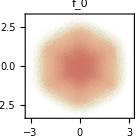
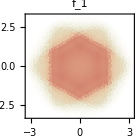
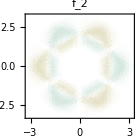

```mathematica
Block[{R=3.2,fs,qs,max=1.8},
{fs,qs}=FortranGet[FileNameJoin[{NotebookDirectory[],"Fortran","twopocket","data",#}]]&/@{"SS_10","QS_10"};
(*max=Max@Abs@Flatten@fs;*)
Row[ListDensityPlot[MapThread[Append,{qs,Rescale[Chop[#1],{-max,max}]}],ColorFunctionScaling->False,PlotRange->{{-R,R},{-R,R},All},RegionFunction->(Norm[{#1,#2}]<R&),PlotLabel->"\!\(f\_"<>#2<>"(q)\)",FrameLabel->{"\!\(q\_x\)","\!\(q\_y\)"},AspectRatio->Automatic,ImageSize->140]&@@@Thread@{Thread@fs,{"0","1","2"}}]]
```

α=1/3, μ=1.3 better nested (perfect nesting at μ=4/3)

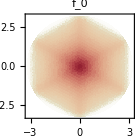
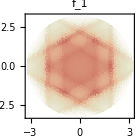
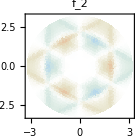

```mathematica
Block[{R=3.2,fs,qs,max=1.8},
{fs,qs}=FortranGet[FileNameJoin[{NotebookDirectory[],"Fortran","twopocket","data",#}]]&/@{"SS_13","QS_13"};
(*max=Max@Abs@Flatten@fs;*)
Row[ListDensityPlot[MapThread[Append,{qs,Rescale[Chop[#1],{-max,max}]}],ColorFunctionScaling->False,PlotRange->{{-R,R},{-R,R},All},RegionFunction->(Norm[{#1,#2}]<R&),PlotLabel->"\!\(f\_"<>#2<>"(q)\)",FrameLabel->{"\!\(q\_x\)","\!\(q\_y\)"},AspectRatio->Automatic,ImageSize->140]&@@@Thread@{Thread@fs,{"0","1","2"}}]]
```

But be aware that the single-orbital model has an artifact close to the perfect nesting, i.e. there are other vertex sharing electron pockets as we go further in the momentum space. But this is not the case in the actual band. This artifact leads to an enhancement of susceptibility in the f_0 channel around Γ_M.

#### RPA Correction

Start from the density interaction in Eq. (DisplayFormulaNumbered) and rewrite in the valley channel,

S_int=U_0 c_(k+q)^†σ^0 c_k' c_(k'-q)^†σ^0 c_k 
=-U_0/2 c_(k+q)^†σ^a c_k c_(k'-q)^†σ^a c_k'
=1/(2 U_0)ϕ_-q^a ϕ_q^a+c_(k+q)^†σ^a c_k ϕ_q^a
=1/(2 U_0)ϕ_-q^a ϕ_q^a-1/2 ϕ_-q^a⟨c_(k'-q)^†σ^a c_k' c_(k+q)^†σ^b c_k⟩_0 ϕ_q^b+c_(k+q)^†σ^a c_k ϕ_q^a
=1/2 ϕ_-q^a(U_0^-1 δ^ab-χ_0^ab(q))ϕ_q^b+c_(k+q)^†σ^a c_k ϕ_q^a
=-1/2U^ab(q)c_(k+q)^†σ^a c_k c_(k'-q)^†σ^b c_k'.

Vallon field ϕ_a is introduced via Hubbard-Stratonovich transformation.

The RPA corrected interaction is given by U^-1=U_0^-1-χ_0, s.t.

U=(1-U_0 χ_0)^-1 U_0=(g_0 |   |   |  
  | g_1 | -ⅈ g_2 |  
  | ⅈ g_2 | g_1 |  
  |   |   | g_0),

where

g_0=U_0/(1-U_0 f_0),
(g_1,g_2)=(U_0-U_0^2 f_1,U_0^2 f_2)/(1-2 U_0 f_1+U_0^2(f_1^2-f_2^2)).

```mathematica
Simplify@Inverse[IdentityMatrix[4]/U0-{{f0,0,0,0},{0,f1,-ⅈ f2,0},{0,ⅈ f2,f1,0},{0,0,0,f0}}]
```

{{U0/(1-f0 U0),0,0,0},{0,(U0-f1 U0^2)/(1-2 f1 U0+f1^2 U0^2-f2^2 U0^2),(ⅈ f2 U0^2)/(-1+2 f1 U0-f1^2 U0^2+f2^2 U0^2),0},{0,(ⅈ f2 U0^2)/(1-2 f1 U0+f1^2 U0^2-f2^2 U0^2),(U0-f1 U0^2)/(1-2 f1 U0+f1^2 U0^2-f2^2 U0^2),0},{0,0,0,U0/(1-f0 U0)}}

Solve Dyson.

RPA corrected interaction (under α=1/3, μ=1, U_0=0.72)

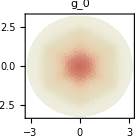
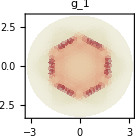
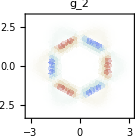

```mathematica
Block[{R=3.2,U0=0.72,fs,qs,gs,max},
{fs,qs}=FortranGet[FileNameJoin[{NotebookDirectory[],"Fortran","twopocket","data",#}]]&/@{"SS_10","QS_10"};
gs=Flatten[{U0/(1-U0#1),{U0-U0^2#2,U0^2#3}/(1-2U0#2+U0^2(#2^2-#3^2))}]&@@@fs;
max=Max@Abs@Flatten@gs;
Row[ListDensityPlot[MapThread[Append,{qs,Rescale[Chop[#1],{-max,max}]}],ColorFunctionScaling->False,PlotRange->{{-R,R},{-R,R},All},RegionFunction->(Norm[{#1,#2}]<R&),PlotLabel->"\!\(g\_"<>#2<>"(q)\)",FrameLabel->{"\!\(q\_x\)","\!\(q\_y\)"},AspectRatio->Automatic,ImageSize->140]&@@@Thread@{Thread@gs,{"0","1","2"}}]]
```

The interaction form factor can be roughly captured by the following model

g_1(q)≃(|Re q_+^3|)/((q^2-2μ)^2+δ)+c,g_2(q)≃(Re q_+^3)/((q^2-2μ)^2+δ)

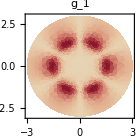
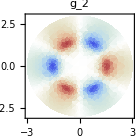

```mathematica
Block[{μ=1,g1,g2,gmax},
g1[{qx_,qy_}]:=Abs@(qx^3-3qx qy^2)/((qx^2+qy^2-2μ)^2+1)+1;
g2[{qx_,qy_}]:=(qx^3-3qx qy^2)/((qx^2+qy^2-2μ)^2+1);
gmax=g1[{Sqrt[2μ],0}];
Row[DensityPlot[Rescale[#1[{qx,qy}],{-gmax,gmax}],{qx,-3,3},{qy,-3,3},ColorFunctionScaling->False,RegionFunction->(Norm[{#1,#2}]<3&),PlotLabel->"\!\(g\_"<>#2<>"(q)\)",FrameLabel->{"\!\(q\_x\)","\!\(q\_y\)"},PlotRange->All,ImageSize->140]&@@@{{g1,"1"},{g2,"2"}}]]
```

Form Factor Model

```mathematica
Block[{R=3.2,U0=0.72,μ=1,fs,qs,gs,max,g1,g2},
{fs,qs}=FortranGet[FileNameJoin[{NotebookDirectory[],"Fortran","twopocket","data",#}]]&/@{"SS_10","QS_10"};
gs=Flatten[{U0/(1-U0#1),{U0-U0^2#2,U0^2#3}/(1-2U0#2+U0^2(#2^2-#3^2))}]&@@@fs;
max=Max@Abs@Flatten@gs;
g1[{qx_,qy_}]:=(Abs[(qx^3-3qx qy^2)]+3)/((qx^2+qy^2-2μ)^2+1)+1;
g2[{qx_,qy_}]:=(qx^3-3qx qy^2)/((qx^2+qy^2-2μ)^2+1);
Row@{Show[{ListLinePlot[Cases[Thread@{qs,Thread[gs]⟦2⟧},{{x_,0.},z_}:>{x,z}],PlotRange->All],Plot[0.5g1[{qx,0}],{qx,-4,4},PlotStyle->Red,PlotRange->All]},PlotRange->All,ImageSize->120],
Show[{ListLinePlot[Cases[Thread@{qs,Thread[gs]⟦3⟧},{{x_,0.},z_}:>{x,z}],PlotRange->All],Plot[0.5 g2[{qx,0}],{qx,-4,4},PlotStyle->Red,PlotRange->All]},PlotRange->All,ImageSize->120]}]
```

-Graphics--Graphics-

### Valley Density Wave Phase

#### VDW Gap

In the presence of the VDW,

H=∑_(Q,k) c_(Q+k)^†(β_(Q+k)σ^0+α_(Q+k)σ^3)c_(Q+k)+∑_(⟨Q Q'⟩,k) (c_(Q'+k)^†I(Q'-Q)c_(Q+k)+h.c.).

The ordering momentum Q spans a honeycomb lattice in the momentum space.

The VDW order is Q_a dependent (a=1,2,3 label the three nearest neighboring momentum transfers)

I(±Q_a)=g(σ^1±ⅈ σ^2).

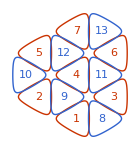

```mathematica
Block[{μ=1,α=1/3,Q=1.7,Qs,FS,Qind},
Qs=Block[{R=1},Association@Table[(-1)^d->Cases[Flatten[Table[Q({3(l1-l2),Sqrt[3](l1+l2)}/2+{d,0}),{l1,-R,R},{l2,-R,R}],1],q_/;Norm[q]≤Q(3R+1.0001)/2],{d,{0,1}}]];
FS=Block[{kF,t0,t1},
kF=FSOrbit[α,μ];
{{t0,t1}}=kF@"Domain";
Cases[ParametricPlot[kF[t0+λ(t1-t0)],{λ,0,1}],_Line,∞]];
Qind=AssociationThread[#->Range@Length@#]&[Join@@(Qs/@{1,-1})];
Graphics[Table[Translate[{Switch[ϛ,1,Red,-1,Blue],Scale[FS,{ϛ,1},{0,0}],Text[Qind[#],{0,0}]},#]&/@Qs[ϛ],{ϛ,Keys@Qs}],ImageSize->140]]
```

##### Well-Nested

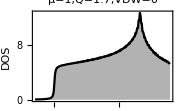
-Graphics--Graphics-

```mathematica
Block[{μ=1,α=1/3,Q=1.7,VDW=0,Qs,Qind,h0,h1,h,kws,dat},
Qs=Block[{R=1},Flatten[Table[Append[#,(-1)^d]&/@Cases[Flatten[Table[Q({3(l1-l2),Sqrt[3](l1+l2)}/2+{d,0}),{l1,-R,R},{l2,-R,R}],1],q_/;Norm[q]≤Q(3R+1.0001)/2],{d,{0,1}}],1]];
h1=SparseArray@Table[Boole[Chop[Abs[Norm@Most@#-Q]]+Abs[Last@#]-2&[Q1-Q2]==0],{Q1,Qs},{Q2,Qs}];
h0[k:{_,_}]:=Block[{ϵ},
ϵ[{kx_,ky_,ϛ_}]:=If[Norm[{kx,ky}]≤2/(3α),kx^2+ky^2-μ-ϛ α(kx^3-3 kx ky^2),2];
SparseArray@DiagonalMatrix[ϵ[Append[k,0]-#]&/@Qs]];
h[k:{_?NumericQ,_?NumericQ}]:=N[h0[k]+VDW h1];
kws=Block[{L=64},Table[If[Sort[l].{1,2}/3≤L,{2Q/Sqrt[3](l.{{1/Sqrt[3],1},{-1/Sqrt[3],1}}/(2L)),Which[l=={0,0},1/6,l=={L,L},1/3,Sort[l]=={0,3L/2},1/4,Sort[l].{1,0}==0||Sort[l].{1,2}/3==L,1/2,True,1]},Nothing],
{l,Tuples[Range[0,3L/2],2]}]];
dat=Eigenvalues@h[First@#]&/@kws;
Row@{Block[{fs0,fs},
fs0=Block[{kF,t0,t1},
kF=FSOrbit[α,μ];{{t0,t1}}=kF@"Domain";
Cases[ParametricPlot[kF[t0+λ(t1-t0)],{λ,0,1},PlotPoints->15,MaxRecursion->1],_Line,∞]];
fs=First@ListContourPlot[MapThread[Append,{First/@kws,Times@@@dat}],InterpolationOrder->1,Contours->{0},ContourStyle->Directive[Black,Opacity[1]],ContourLabels->None,ContourShading->None];
Graphics[{{LightGray,Polygon@CirclePoints[{2Q/Sqrt[3],π/6},6]},Block[{plt},plt[{kx_,ky_,ϛ_}]:={Switch[ϛ,1,Red,-1,Blue],Translate[Scale[fs0,{ϛ,1},{0,0}],{kx,ky}]};{Opacity[0.2],plt/@Qs}],Scale[Rotate[fs,2π#/3,{0,0}]&/@Range[3],{1,#},{0,0}]&/@{-1,1}},PlotRange->2Q/Sqrt[3],ImageSize->120]],
Block[{dω=0.01,es,ws,A},
{es,ws}=Thread@SortBy[Flatten[MapThread[Table[{e,#2},{e,Cases[#1,x_/;x<1]}]&,{dat,Last/@kws}],1],First];
ws=ws/Total[Last/@kws];
A[ω_]:=-2Im[1/(ω+ⅈ dω-es)].ws;
ListLinePlot[Table[{ω,A[ω]},{ω,-1.3,0.8,dω}],Filling->Axis,PlotStyle->Black,FrameLabel->{None,"DOS"},PlotLabel->Style["\!\("<>StringJoin[Riffle[#2<>"="<>ToString[InputForm[#1]]&@@@{{μ,"μ"},{Q,"Q"},{VDW,"VDW"}},","]]<>"\)",12,FontFamily->"CMU"],ImageSize->180]]}
]
```

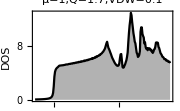
-Graphics--Graphics-

```mathematica
Block[{μ=1,α=1/3,Q=1.7,VDW=0.1,Qs,Qind,h0,h1,h,kws,dat},
Qs=Block[{R=1},Flatten[Table[Append[#,(-1)^d]&/@Cases[Flatten[Table[Q({3(l1-l2),Sqrt[3](l1+l2)}/2+{d,0}),{l1,-R,R},{l2,-R,R}],1],q_/;Norm[q]≤Q(3R+1.0001)/2],{d,{0,1}}],1]];
h1=SparseArray@Table[Boole[Chop[Abs[Norm@Most@#-Q]]+Abs[Last@#]-2&[Q1-Q2]==0],{Q1,Qs},{Q2,Qs}];
h0[k:{_,_}]:=Block[{ϵ},
ϵ[{kx_,ky_,ϛ_}]:=If[Norm[{kx,ky}]≤2/(3α),kx^2+ky^2-μ-ϛ α(kx^3-3 kx ky^2),2];
SparseArray@DiagonalMatrix[ϵ[Append[k,0]-#]&/@Qs]];
h[k:{_?NumericQ,_?NumericQ}]:=N[h0[k]+VDW h1];
kws=Block[{L=64},Table[If[Sort[l].{1,2}/3≤L,{2Q/Sqrt[3](l.{{1/Sqrt[3],1},{-1/Sqrt[3],1}}/(2L)),Which[l=={0,0},1/6,l=={L,L},1/3,Sort[l]=={0,3L/2},1/4,Sort[l].{1,0}==0||Sort[l].{1,2}/3==L,1/2,True,1]},Nothing],
{l,Tuples[Range[0,3L/2],2]}]];
dat=Eigenvalues@h[First@#]&/@kws;
Row@{Block[{fs0,fs},
fs0=Block[{kF,t0,t1},
kF=FSOrbit[α,μ];{{t0,t1}}=kF@"Domain";
Cases[ParametricPlot[kF[t0+λ(t1-t0)],{λ,0,1},PlotPoints->15,MaxRecursion->1],_Line,∞]];
fs=First@ListContourPlot[MapThread[Append,{First/@kws,Times@@@dat}],InterpolationOrder->1,Contours->{0},ContourStyle->Directive[Black,Opacity[1]],ContourLabels->None,ContourShading->None];
Graphics[{{LightGray,Polygon@CirclePoints[{2Q/Sqrt[3],π/6},6]},Block[{plt},plt[{kx_,ky_,ϛ_}]:={Switch[ϛ,1,Red,-1,Blue],Translate[Scale[fs0,{ϛ,1},{0,0}],{kx,ky}]};{Opacity[0.2],plt/@Qs}],Scale[Rotate[fs,2π#/3,{0,0}]&/@Range[3],{1,#},{0,0}]&/@{-1,1}},PlotRange->2Q/Sqrt[3],ImageSize->120]],
Block[{dω=0.01,es,ws,A},
{es,ws}=Thread@SortBy[Flatten[MapThread[Table[{e,#2},{e,Cases[#1,x_/;x<1]}]&,{dat,Last/@kws}],1],First];
ws=ws/Total[Last/@kws];
A[ω_]:=-2Im[1/(ω+ⅈ dω-es)].ws;
ListLinePlot[Table[{ω,A[ω]},{ω,-1.3,0.8,dω}],Filling->Axis,PlotStyle->Black,FrameLabel->{None,"DOS"},PlotLabel->Style["\!\("<>StringJoin[Riffle[#2<>"="<>ToString[InputForm[#1]]&@@@{{μ,"μ"},{Q,"Q"},{VDW,"VDW"}},","]]<>"\)",12,FontFamily->"CMU"],ImageSize->180]]}
]
```

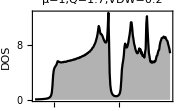
-Graphics--Graphics-

```mathematica
Block[{μ=1,α=1/3,Q=1.7,VDW=0.2,Qs,Qind,h0,h1,h,kws,dat},
Qs=Block[{R=1},Flatten[Table[Append[#,(-1)^d]&/@Cases[Flatten[Table[Q({3(l1-l2),Sqrt[3](l1+l2)}/2+{d,0}),{l1,-R,R},{l2,-R,R}],1],q_/;Norm[q]≤Q(3R+1.0001)/2],{d,{0,1}}],1]];
h1=SparseArray@Table[Boole[Chop[Abs[Norm@Most@#-Q]]+Abs[Last@#]-2&[Q1-Q2]==0],{Q1,Qs},{Q2,Qs}];
h0[k:{_,_}]:=Block[{ϵ},
ϵ[{kx_,ky_,ϛ_}]:=If[Norm[{kx,ky}]≤2/(3α),kx^2+ky^2-μ-ϛ α(kx^3-3 kx ky^2),2];
SparseArray@DiagonalMatrix[ϵ[Append[k,0]-#]&/@Qs]];
h[k:{_?NumericQ,_?NumericQ}]:=N[h0[k]+VDW h1];
kws=Block[{L=64},Table[If[Sort[l].{1,2}/3≤L,{2Q/Sqrt[3](l.{{1/Sqrt[3],1},{-1/Sqrt[3],1}}/(2L)),Which[l=={0,0},1/6,l=={L,L},1/3,Sort[l]=={0,3L/2},1/4,Sort[l].{1,0}==0||Sort[l].{1,2}/3==L,1/2,True,1]},Nothing],
{l,Tuples[Range[0,3L/2],2]}]];
dat=Eigenvalues@h[First@#]&/@kws;
Row@{Block[{fs0,fs},
fs0=Block[{kF,t0,t1},
kF=FSOrbit[α,μ];{{t0,t1}}=kF@"Domain";
Cases[ParametricPlot[kF[t0+λ(t1-t0)],{λ,0,1},PlotPoints->15,MaxRecursion->1],_Line,∞]];
fs=First@ListContourPlot[MapThread[Append,{First/@kws,Times@@@dat}],InterpolationOrder->1,Contours->{0},ContourStyle->Directive[Black,Opacity[1]],ContourLabels->None,ContourShading->None];
Graphics[{{LightGray,Polygon@CirclePoints[{2Q/Sqrt[3],π/6},6]},Block[{plt},plt[{kx_,ky_,ϛ_}]:={Switch[ϛ,1,Red,-1,Blue],Translate[Scale[fs0,{ϛ,1},{0,0}],{kx,ky}]};{Opacity[0.2],plt/@Qs}],Scale[Rotate[fs,2π#/3,{0,0}]&/@Range[3],{1,#},{0,0}]&/@{-1,1}},PlotRange->2Q/Sqrt[3],ImageSize->120]],
Block[{dω=0.01,es,ws,A},
{es,ws}=Thread@SortBy[Flatten[MapThread[Table[{e,#2},{e,Cases[#1,x_/;x<1]}]&,{dat,Last/@kws}],1],First];
ws=ws/Total[Last/@kws];
A[ω_]:=-2Im[1/(ω+ⅈ dω-es)].ws;
ListLinePlot[Table[{ω,A[ω]},{ω,-1.3,0.8,dω}],Filling->Axis,PlotStyle->Black,FrameLabel->{None,"DOS"},PlotLabel->Style["\!\("<>StringJoin[Riffle[#2<>"="<>ToString[InputForm[#1]]&@@@{{μ,"μ"},{Q,"Q"},{VDW,"VDW"}},","]]<>"\)",12,FontFamily->"CMU"],ImageSize->180]]}
]
```

##### Doping

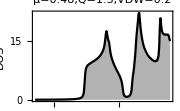
-Graphics--Graphics-

```mathematica
Block[{μ=0.48,α=1/3,Q=1.3,VDW=0.2,Qs,Qind,h0,h1,h,kws,dat},
Qs=Block[{R=1},Flatten[Table[Append[#,(-1)^d]&/@Cases[Flatten[Table[Q({3(l1-l2),Sqrt[3](l1+l2)}/2+{d,0}),{l1,-R,R},{l2,-R,R}],1],q_/;Norm[q]≤Q(3R+1.0001)/2],{d,{0,1}}],1]];
h1=SparseArray@Table[Boole[Chop[Abs[Norm@Most@#-Q]]+Abs[Last@#]-2&[Q1-Q2]==0],{Q1,Qs},{Q2,Qs}];
h0[k:{_,_}]:=Block[{ϵ},
ϵ[{kx_,ky_,ϛ_}]:=If[Norm[{kx,ky}]≤2/(3α),kx^2+ky^2-μ-ϛ α(kx^3-3 kx ky^2),2];
SparseArray@DiagonalMatrix[ϵ[Append[k,0]-#]&/@Qs]];
h[k:{_?NumericQ,_?NumericQ}]:=N[h0[k]+VDW h1];
kws=Block[{L=64},Table[If[Sort[l].{1,2}/3≤L,{2Q/Sqrt[3](l.{{1/Sqrt[3],1},{-1/Sqrt[3],1}}/(2L)),Which[l=={0,0},1/6,l=={L,L},1/3,Sort[l]=={0,3L/2},1/4,Sort[l].{1,0}==0||Sort[l].{1,2}/3==L,1/2,True,1]},Nothing],
{l,Tuples[Range[0,3L/2],2]}]];
dat=Eigenvalues@h[First@#]&/@kws;
Row@{Block[{fs0,fs},
fs0=Block[{kF,t0,t1},
kF=FSOrbit[α,μ];{{t0,t1}}=kF@"Domain";
Cases[ParametricPlot[kF[t0+λ(t1-t0)],{λ,0,1},PlotPoints->15,MaxRecursion->1],_Line,∞]];
fs=First@ListContourPlot[MapThread[Append,{First/@kws,Times@@@dat}],InterpolationOrder->1,Contours->{0},ContourStyle->Directive[Black,Opacity[1]],ContourLabels->None,ContourShading->None];
Graphics[{{LightGray,Polygon@CirclePoints[{2Q/Sqrt[3],π/6},6]},Block[{plt},plt[{kx_,ky_,ϛ_}]:={Switch[ϛ,1,Red,-1,Blue],Translate[Scale[fs0,{ϛ,1},{0,0}],{kx,ky}]};{Opacity[0.2],plt/@Qs}],Scale[Rotate[fs,2π#/3,{0,0}]&/@Range[3],{1,#},{0,0}]&/@{-1,1}},PlotRange->2Q/Sqrt[3],ImageSize->120]],
Block[{dω=0.01,es,ws,A},
{es,ws}=Thread@SortBy[Flatten[MapThread[Table[{e,#2},{e,Cases[#1,x_/;x<1]}]&,{dat,Last/@kws}],1],First];
ws=ws/Total[Last/@kws];
A[ω_]:=-2Im[1/(ω+ⅈ dω-es)].ws;
ListLinePlot[Table[{ω,A[ω]},{ω,-1.3,0.8,dω}],Filling->Axis,PlotStyle->Black,FrameLabel->{None,"DOS"},PlotLabel->Style["\!\("<>StringJoin[Riffle[#2<>"="<>ToString[InputForm[#1]]&@@@{{μ,"μ"},{Q,"Q"},{VDW,"VDW"}},","]]<>"\)",12,FontFamily->"CMU"],ImageSize->180]]}
]
```

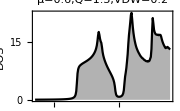
-Graphics--Graphics-

```mathematica
Block[{μ=0.6,α=1/3,Q=1.3,VDW=0.2,Qs,Qind,h0,h1,h,kws,dat},
Qs=Block[{R=1},Flatten[Table[Append[#,(-1)^d]&/@Cases[Flatten[Table[Q({3(l1-l2),Sqrt[3](l1+l2)}/2+{d,0}),{l1,-R,R},{l2,-R,R}],1],q_/;Norm[q]≤Q(3R+1.0001)/2],{d,{0,1}}],1]];
h1=SparseArray@Table[Boole[Chop[Abs[Norm@Most@#-Q]]+Abs[Last@#]-2&[Q1-Q2]==0],{Q1,Qs},{Q2,Qs}];
h0[k:{_,_}]:=Block[{ϵ},
ϵ[{kx_,ky_,ϛ_}]:=If[Norm[{kx,ky}]≤2/(3α),kx^2+ky^2-μ-ϛ α(kx^3-3 kx ky^2),2];
SparseArray@DiagonalMatrix[ϵ[Append[k,0]-#]&/@Qs]];
h[k:{_?NumericQ,_?NumericQ}]:=N[h0[k]+VDW h1];
kws=Block[{L=64},Table[If[Sort[l].{1,2}/3≤L,{2Q/Sqrt[3](l.{{1/Sqrt[3],1},{-1/Sqrt[3],1}}/(2L)),Which[l=={0,0},1/6,l=={L,L},1/3,Sort[l]=={0,3L/2},1/4,Sort[l].{1,0}==0||Sort[l].{1,2}/3==L,1/2,True,1]},Nothing],
{l,Tuples[Range[0,3L/2],2]}]];
dat=Eigenvalues@h[First@#]&/@kws;
Row@{Block[{fs0,fs},
fs0=Block[{kF,t0,t1},
kF=FSOrbit[α,μ];{{t0,t1}}=kF@"Domain";
Cases[ParametricPlot[kF[t0+λ(t1-t0)],{λ,0,1},PlotPoints->15,MaxRecursion->1],_Line,∞]];
fs=First@ListContourPlot[MapThread[Append,{First/@kws,Times@@@dat}],InterpolationOrder->1,Contours->{0},ContourStyle->Directive[Black,Opacity[1]],ContourLabels->None,ContourShading->None];
Graphics[{{LightGray,Polygon@CirclePoints[{2Q/Sqrt[3],π/6},6]},Block[{plt},plt[{kx_,ky_,ϛ_}]:={Switch[ϛ,1,Red,-1,Blue],Translate[Scale[fs0,{ϛ,1},{0,0}],{kx,ky}]};{Opacity[0.2],plt/@Qs}],Scale[Rotate[fs,2π#/3,{0,0}]&/@Range[3],{1,#},{0,0}]&/@{-1,1}},PlotRange->2Q/Sqrt[3],ImageSize->120]],
Block[{dω=0.01,es,ws,A},
{es,ws}=Thread@SortBy[Flatten[MapThread[Table[{e,#2},{e,Cases[#1,x_/;x<1]}]&,{dat,Last/@kws}],1],First];
ws=ws/Total[Last/@kws];
A[ω_]:=-2Im[1/(ω+ⅈ dω-es)].ws;
ListLinePlot[Table[{ω,A[ω]},{ω,-1.3,0.8,dω}],Filling->Axis,PlotStyle->Black,FrameLabel->{None,"DOS"},PlotLabel->Style["\!\("<>StringJoin[Riffle[#2<>"="<>ToString[InputForm[#1]]&@@@{{μ,"μ"},{Q,"Q"},{VDW,"VDW"}},","]]<>"\)",12,FontFamily->"CMU"],ImageSize->180]]}
]
```

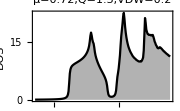
-Graphics--Graphics-

```mathematica
Block[{μ=0.72,α=1/3,Q=1.3,VDW=0.2,Qs,Qind,h0,h1,h,kws,dat},
Qs=Block[{R=1},Flatten[Table[Append[#,(-1)^d]&/@Cases[Flatten[Table[Q({3(l1-l2),Sqrt[3](l1+l2)}/2+{d,0}),{l1,-R,R},{l2,-R,R}],1],q_/;Norm[q]≤Q(3R+1.0001)/2],{d,{0,1}}],1]];
h1=SparseArray@Table[Boole[Chop[Abs[Norm@Most@#-Q]]+Abs[Last@#]-2&[Q1-Q2]==0],{Q1,Qs},{Q2,Qs}];
h0[k:{_,_}]:=Block[{ϵ},
ϵ[{kx_,ky_,ϛ_}]:=If[Norm[{kx,ky}]≤2/(3α),kx^2+ky^2-μ-ϛ α(kx^3-3 kx ky^2),2];
SparseArray@DiagonalMatrix[ϵ[Append[k,0]-#]&/@Qs]];
h[k:{_?NumericQ,_?NumericQ}]:=N[h0[k]+VDW h1];
kws=Block[{L=64},Table[If[Sort[l].{1,2}/3≤L,{2Q/Sqrt[3](l.{{1/Sqrt[3],1},{-1/Sqrt[3],1}}/(2L)),Which[l=={0,0},1/6,l=={L,L},1/3,Sort[l]=={0,3L/2},1/4,Sort[l].{1,0}==0||Sort[l].{1,2}/3==L,1/2,True,1]},Nothing],
{l,Tuples[Range[0,3L/2],2]}]];
dat=Eigenvalues@h[First@#]&/@kws;
Row@{Block[{fs0,fs},
fs0=Block[{kF,t0,t1},
kF=FSOrbit[α,μ];{{t0,t1}}=kF@"Domain";
Cases[ParametricPlot[kF[t0+λ(t1-t0)],{λ,0,1},PlotPoints->15,MaxRecursion->1],_Line,∞]];
fs=First@ListContourPlot[MapThread[Append,{First/@kws,Times@@@dat}],InterpolationOrder->1,Contours->{0},ContourStyle->Directive[Black,Opacity[1]],ContourLabels->None,ContourShading->None];
Graphics[{{LightGray,Polygon@CirclePoints[{2Q/Sqrt[3],π/6},6]},Block[{plt},plt[{kx_,ky_,ϛ_}]:={Switch[ϛ,1,Red,-1,Blue],Translate[Scale[fs0,{ϛ,1},{0,0}],{kx,ky}]};{Opacity[0.2],plt/@Qs}],Scale[Rotate[fs,2π#/3,{0,0}]&/@Range[3],{1,#},{0,0}]&/@{-1,1}},PlotRange->2Q/Sqrt[3],ImageSize->120]],
Block[{dω=0.01,es,ws,A},
{es,ws}=Thread@SortBy[Flatten[MapThread[Table[{e,#2},{e,Cases[#1,x_/;x<1]}]&,{dat,Last/@kws}],1],First];
ws=ws/Total[Last/@kws];
A[ω_]:=-2Im[1/(ω+ⅈ dω-es)].ws;
ListLinePlot[Table[{ω,A[ω]},{ω,-1.3,0.8,dω}],Filling->Axis,PlotStyle->Black,FrameLabel->{None,"DOS"},PlotLabel->Style["\!\("<>StringJoin[Riffle[#2<>"="<>ToString[InputForm[#1]]&@@@{{μ,"μ"},{Q,"Q"},{VDW,"VDW"}},","]]<>"\)",12,FontFamily->"CMU"],ImageSize->180]]}
]
```

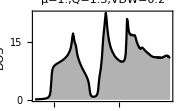
-Graphics--Graphics-

```mathematica
Block[{μ=1.,α=1/3,Q=1.3,VDW=0.2,Qs,Qind,h0,h1,h,kws,dat},
Qs=Block[{R=1},Flatten[Table[Append[#,(-1)^d]&/@Cases[Flatten[Table[Q({3(l1-l2),Sqrt[3](l1+l2)}/2+{d,0}),{l1,-R,R},{l2,-R,R}],1],q_/;Norm[q]≤Q(3R+1.0001)/2],{d,{0,1}}],1]];
h1=SparseArray@Table[Boole[Chop[Abs[Norm@Most@#-Q]]+Abs[Last@#]-2&[Q1-Q2]==0],{Q1,Qs},{Q2,Qs}];
h0[k:{_,_}]:=Block[{ϵ},
ϵ[{kx_,ky_,ϛ_}]:=If[Norm[{kx,ky}]≤2/(3α),kx^2+ky^2-μ-ϛ α(kx^3-3 kx ky^2),2];
SparseArray@DiagonalMatrix[ϵ[Append[k,0]-#]&/@Qs]];
h[k:{_?NumericQ,_?NumericQ}]:=N[h0[k]+VDW h1];
kws=Block[{L=64},Table[If[Sort[l].{1,2}/3≤L,{2Q/Sqrt[3](l.{{1/Sqrt[3],1},{-1/Sqrt[3],1}}/(2L)),Which[l=={0,0},1/6,l=={L,L},1/3,Sort[l]=={0,3L/2},1/4,Sort[l].{1,0}==0||Sort[l].{1,2}/3==L,1/2,True,1]},Nothing],
{l,Tuples[Range[0,3L/2],2]}]];
dat=Eigenvalues@h[First@#]&/@kws;
Row@{Block[{fs0,fs},
fs0=Block[{kF,t0,t1},
kF=FSOrbit[α,μ];{{t0,t1}}=kF@"Domain";
Cases[ParametricPlot[kF[t0+λ(t1-t0)],{λ,0,1},PlotPoints->15,MaxRecursion->1],_Line,∞]];
fs=First@ListContourPlot[MapThread[Append,{First/@kws,Times@@@dat}],InterpolationOrder->1,Contours->{0},ContourStyle->Directive[Black,Opacity[1]],ContourLabels->None,ContourShading->None];
Graphics[{{LightGray,Polygon@CirclePoints[{2Q/Sqrt[3],π/6},6]},Block[{plt},plt[{kx_,ky_,ϛ_}]:={Switch[ϛ,1,Red,-1,Blue],Translate[Scale[fs0,{ϛ,1},{0,0}],{kx,ky}]};{Opacity[0.2],plt/@Qs}],Scale[Rotate[fs,2π#/3,{0,0}]&/@Range[3],{1,#},{0,0}]&/@{-1,1}},PlotRange->2Q/Sqrt[3],ImageSize->120]],
Block[{dω=0.01,es,ws,A},
{es,ws}=Thread@SortBy[Flatten[MapThread[Table[{e,#2},{e,Cases[#1,x_/;x<1]}]&,{dat,Last/@kws}],1],First];
ws=ws/Total[Last/@kws];
A[ω_]:=-2Im[1/(ω+ⅈ dω-es)].ws;
ListLinePlot[Table[{ω,A[ω]},{ω,-1.3,0.8,dω}],Filling->Axis,PlotStyle->Black,FrameLabel->{None,"DOS"},PlotLabel->Style["\!\("<>StringJoin[Riffle[#2<>"="<>ToString[InputForm[#1]]&@@@{{μ,"μ"},{Q,"Q"},{VDW,"VDW"}},","]]<>"\)",12,FontFamily->"CMU"],ImageSize->180]]}
]
```

#### MBZ Formulation

We can represent the momentum by MBZ parameter

k/q=m·(+(√3)/2 | 3/2
-(√3)/2 | 3/2)=m·Q

The matrix will be call Q.

With this, the MBZ is parameterized by (m∈[0,1))^(×2).

The Dirac points are located at

m(K_top)=(2/3,2/3),m(K_bot)=(1/3,1/3).

The three K_top→K_bot vectors are

m(q_1)=(-1/3,-1/3), m(q_2)=m(q_1)+(1,0),m(q_3)=m(q_1)+(0,1).

We extract the dispersion of the lower band (branch) that is closest to the charge neutrality.

The result is saved in interpolation function.

We create functions for K and K' valleys.

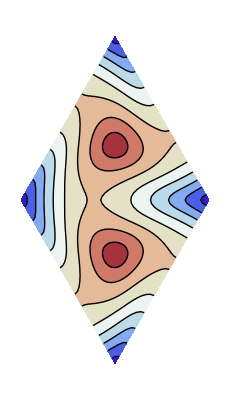
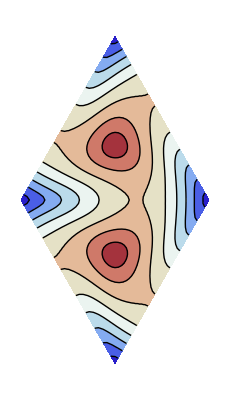

```mathematica
Block[{w0,w1,w3,Qmat},
{w0,w1,w3}=2.5{0.11,-0.12,0.00};
Qmat={{Sqrt[3],3},{-Sqrt[3],3}}/2;
Module[{L=2,dm=1/48,ls,NK,ind,hD,T,hT,ms},
ls=Tuples[Range[-L,L],2];
NK=Length@ls;
ind=AssociationThread[ls->Range@NK];
hD[m_]:=
Total[MapIndexed[KroneckerProduct[SparseArray[{Band[{1,1}]->#1}],PauliMatrix[First@#2]]&,Thread[-Join[m-#-{2/3,2/3}&/@ls,m-#-{1/3,1/3}&/@ls].Qmat]]];
T=Association@Table[s->SparseArray[w0 PauliMatrix[0]+w1(s-{1/3,1/3}).Qmat.{PauliMatrix[2],-PauliMatrix[1]}+ⅈ w3 PauliMatrix[3]],{s,{{0,0},{1,0},{0,1}}}];
hT=(#+ConjugateTranspose[#])&@Sum[KroneckerProduct[SparseArray[Table[{0,NK}+(ind/@Mod[{l,l+s},2L+1,-L])->1,{l,ls}],{2NK,2NK}],T[s]],{s,Keys@T}];
ms=Tuples[Range[0,1,dm],2];
hK=Interpolation[Table[Block[{h,e},
h=hD[m]+hT;
e=Min[SortBy[Eigenvalues[h,8,Method->{"Arnoldi","Shift"->0}],Abs]⟦;;2⟧];
Append[m,e]],{m,ms}]];
hKp[m1_,m2_]:=hK[m2,m1];
ListContourPlot[Table[Append[m.Qmat,#@@m],{m,ms}],ContourStyle->Directive[AbsoluteThickness[1],Black,Opacity[1]],AspectRatio->Automatic,Frame->None,ImageSize->{Automatic,120}]&/@{hK,hKp}]]
```

Using these dispersions, we construct the VDW Hamiltonian in the reduced BZ ([0,1/2))^(×2).

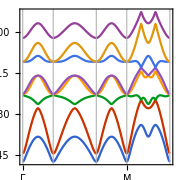

```mathematica
Block[{VDW=0.06,h0,h1,h},
h0[{m1_,m2_},b_:1]:=DiagonalMatrix[Flatten@Table[b f[m1+s1,m2+s2],{f,{hK,hKp}},{s1,{0,1/2}},{s2,{0,1/2}}]];
h1=VDW ArrayFlatten[{{0,#},{#,0}}&@(1-IdentityMatrix[4])];
h[m_,b_:1]:=h0[m,b]+h1;
Block[{Es},
Es[m_]:=Sort@Eigenvalues@h[m];
(*Es[m_]:=Sort[Join@@Table[Eigenvalues@h[m,b],{b,{-1,1}}]];*)
BZPlot[Es,{"Γ","X","Y","M","Γ"},BZRules->{"Γ"->{0,0},"X"->{1,0}/2,"M"->{1,1}/2,"Y"->{0,1}/2},MomentumResolution->1/72,AspectRatio->1,ImageSize->180]]]
```

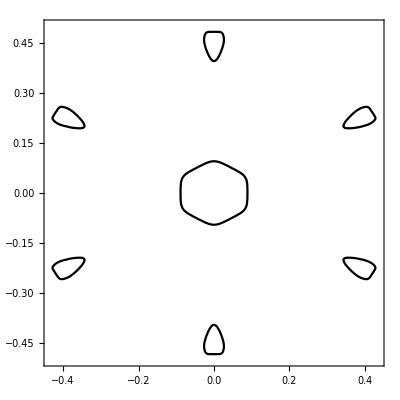

```mathematica
Block[{VDW=0.015,Qmat,h0,h1,h},
Qmat={{Sqrt[3],3},{-Sqrt[3],3}}/2;
h0[{m1_,m2_}]:=DiagonalMatrix[Flatten@Table[f[m1+s1,m2+s2],{f,{hK,hKp}},{s1,{0,1/2}},{s2,{0,1/2}}]];
h1=VDW ArrayFlatten[{{0,#},{#,0}}&@(1-IdentityMatrix[4])];
h[m_]:=h0[m]+h1;
Block[{dω=0.001,ms,es,FS,ws,A,νs,μs},
ms=DeleteCases[Tuples[Range[0,1/2,1/120],2],{m1_,m2_}/;m1+m2>1/2];
es=Table[Eigenvalues@h[m],{m,ms}];
FS[μ_]:=Block[{dets,dat,f0,invQ,f1},
dets=Times@@@(20(es-μ));
dat=DeleteDuplicates[Join[MapThread[Append,{ms,dets}],MapThread[Append,{1/2-ms,dets}]],Most[#1]==Most[#2]&];
f0=Interpolation[dat];
invQ=N@Inverse[Qmat];
f1[{k1_,k2_}]:=f0@@Mod[({k1,k2}.invQ),1/2];
ContourPlot[f1[{k1,k2}]==0,{k1,-Sqrt[3]/4,Sqrt[3]/4},{k2,-1/2,1/2},Exclusions->None,RegionFunction->(Abs[#1]/Sqrt[3]+Abs[#2]≤1/2&),ContourStyle->Black,ContourLabels->False]];
FS[-0.2]]]
```

Dispersion and Density of State

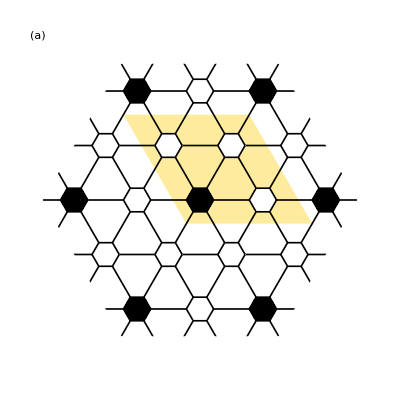
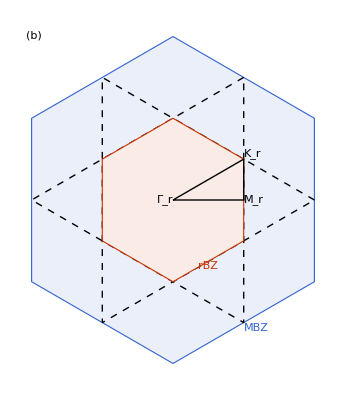
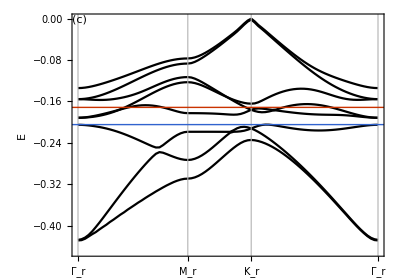
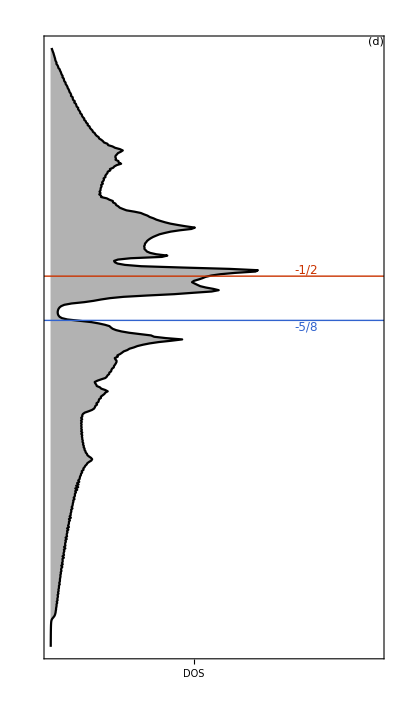

```mathematica
Column[{Row[{Block[{L=3,dsk},
dsk=Polygon[CirclePoints[{0.25,0},6]];
Graphics[
{{Lighter[Yellow,0.5],Parallelogram[{-1/4,-Sqrt[3]/4},{{4/Sqrt[3],0},{-2/Sqrt[3],2}}]},{AbsoluteThickness[1.2],Rotate[Table[Line[{#,y}&/@{-L,L}],{y,-L,L}],2π #/3,{0,0}]&/@{0,1,2}},
{EdgeForm[Directive[AbsoluteThickness[1.2],Black]],Table[Translate[{If[EvenQ[l1]&&EvenQ[l2],Black,White],dsk},{(2l1+l2)/Sqrt[3],l2}],{l1,-L,L},{l2,-L,L}]},{White,Rotate[Rectangle[{-2L,L-0.5},{2L,L+3}],π #/3,{0,0}]&/@Range[0,5]},
Text["(a)",Scaled[{0,1}],{-1,1}]},PlotRange->{{-L,L},{-L,L}},ImageSize->{Automatic,110}]],
Block[{lt=0.9},Graphics[{{EdgeForm[Blue],Lighter[Blue,lt],Polygon[CirclePoints[{1,π/6},6]]},
GraphicsComplex[CirclePoints[{Sqrt[3]/2,0},6],{Dashed,Line[{1,3,5,1}],Line[{2,4,6,2}]}],{EdgeForm[Red],Lighter[Red,lt],Polygon[CirclePoints[{1/2,π/6},6]]},
GraphicsComplex[{{0,0},{Sqrt[3]/4,0},{Sqrt[3]/4,1/4}},{AbsoluteThickness[1],Line[{1,2,3,1}],Text["\!\(Γ\_r\)",1,{1,0}],Text[Style["\!\(M\_r\)",Background->Lighter[Blue,lt]],2,{-1.2,0}],Text["\!\(K\_r\)",3,{-1,-0.5}]}],
{Blue,Text["MBZ",{Sqrt[3]/4,-3/4},{-1,1},{Sqrt[3],1}]},{Red,Text[Style["rBZ",Background->Lighter[Blue,lt]],{Sqrt[3]/8,-3/8},{0,1},{Sqrt[3],1}]},
Text["(b)",Scaled[{0,1}],{-1,1}]},ImageSize->{Automatic,110}]]},Spacer[12]],
Block[{VDW=0.018,Qmat,h0,h1,h},
Qmat={{Sqrt[3],3},{-Sqrt[3],3}}/2;
h0[{m1_,m2_}]:=DiagonalMatrix[Flatten@Table[f[m1+s1,m2+s2],{f,{hK,hKp}},{s1,{0,1/2}},{s2,{0,1/2}}]];
h1=VDW ArrayFlatten[{{0,#},{#,0}}&@(1-IdentityMatrix[4])];
h[m_]:=h0[m]+h1;
Block[{dω=0.001,ms,es,emax,ws,A,νs,μs,invQ,Es},
ms=DeleteCases[Tuples[Range[0,1/2,1/240],2],{m1_,m2_}/;m1+m2>1/2];
es=Table[Eigenvalues@h[m],{m,ms}];
emax=Max@Flatten@es;
es=es-emax;
ws=If[#1==0,If[#2==0,1/6,If[#2==1/2,1/6,1/2]],If[#2==0,If[#1==1/2,1/6,1/2],If[#1+#2==1/2,1/2,1]]]&@@@ms;
ws=ws/Total[ws];
νs={3/8,1/2};
μs=Quantile[Flatten[es],νs];
A[ω_]:=Mean[-ws.Im[1/(ω+ⅈ dω-es)]]/π;
invQ=Inverse[Qmat];
Es[k_]:=Sort@Eigenvalues@h[Mod[k.invQ,1/2]]-emax;
Row[{BZPlot[Es,{"\!\(Γ\_r\)","\!\(M\_r\)","\!\(K\_r\)","\!\(Γ\_r\)"},BZRules->{"\!\(Γ\_r\)"->{0,0},"\!\(M\_r\)"->{Sqrt[3]/4,0},"\!\(K\_r\)"->{Sqrt[3]/4,1/4}},MomentumResolution->1/72,PlotStyle->Black,FrameLabel->{None,Style["\!\(E\)",14]},PlotRange->{-0.45,0},Epilog->{AbsoluteThickness[1],MapThread[{#1,InfiniteLine[{{0,#2},{1,#2}}]}&,{ColorData[0]/@Range[Length@νs],μs}],
Text["(c)",Scaled[{0,1}],{-1.5,1}]},AspectRatio->0.7,ImageSize->{Automatic,130}],
Graphics[Rotate[First@ListLinePlot[Table[{-ω,A[ω]},{ω,-0.45,0.0,dω}],Filling->Axis,PlotStyle->Black],-π/2,{0,0}],PlotRange->{{0,16},{-0.45,0}},Frame->True,FrameTicks->{{Table[{y,"",{0.02,0}},{y,0,-0.5,-0.02}],Automatic},{{{7,"DOS",{0,0}}},Automatic}},Epilog->{AbsoluteThickness[1],MapThread[{#1,InfiniteLine[{{0,#2},{1,#2}}],Text[Style[ToString@InputForm@(#3-1),12],{12.5,#2},{0,#4}]}&,{ColorData[0]/@Range[Length@νs],μs,νs,{1,-1}}],
Text["(d)",Scaled[{1,1}],{1.5,1}]},AspectRatio->1.8,ImageSize->{Automatic,130}]}]]]},Alignment->Center]
```

A 2*2 patter on the Moire lattice, little hexagon represents the AA stacking region. The enlarged unit-cell is highlighted.

#### Nesting at K

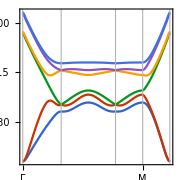

```mathematica
Block[{VDW=0.03,h0,h1,h},
h0[m:{_,_},b_:1]:=DiagonalMatrix[Flatten@Table[b f@@Mod[m+q,1],{f,{hK,hKp}},{q,{{0,0},{1/3,1/3},-{1/3,1/3}}}]];
h1=VDW ArrayFlatten[{{0,#},{#,0}}&@(1-IdentityMatrix[3])];
h[m_,b_:1]:=h0[m,b]+h1;
Block[{Es},
Es[m_]:=Sort@Eigenvalues@h[m];
(*Es[m_]:=Sort[Join@@Table[Eigenvalues@h[m,b],{b,{-1,1}}]];*)
BZPlot[Es,{"Γ","X","Y","M","Γ"},BZRules->{"Γ"->{0,0},"X"->{1,0}/3,"M"->{1,1}/6,"Y"->{0,1}/3},MomentumResolution->1/72,AspectRatio->1,ImageSize->180]]]
```

### Superconducting Phase

#### Pairing Instability

The interaction in Eq. (DisplayFormulaNumbered) can be rewrite in the pairing channel as

H_int=-1/2∑_(k,k',q) U^ab(q)c_(k+q,α)^†σ_αγ^a c_(k,γ) c_(k'-q,β)^†σ_βδ^b c_(k',δ)
=-∑_(k,k',q) (g(q))_(αβ,γδ)c_(k'-q,β)^†c_(k+q,α)^†c_(k,γ) c_(k',δ)
≃-∑_(k,q) (g(q))_(αβ,γδ)Δ_(k+q,αβ)^†Δ_(k,γδ).

Δ_(k,αβ)=c_(k,α) c_(-k,β) is the pairing operator.

The pairing interaction is given by

g(q)=(g_0(q) | 0 | 0 | 0
0 | 0 | g_1(q)+g_2(q) | 0
0 | g_1(q)-g_2(q) | 0 | 0
0 | 0 | 0 | g_0(q)).

```mathematica
Block[{U,vs,g},
U={{g0,0,0,0},{0,g1,-ⅈ g2,0},{0,ⅈ g2,g1,0},{0,0,0,g0}};
vs=σ/@Range[0,3];
g=(1/2)Represent@Total@Flatten[U Outer[CircleTimes,vs,vs]];
MatrixForm@Simplify@g]
```

(g0 | 0 | 0 | 0
0 | 0 | g1+g2 | 0
0 | g1-g2 | 0 | 0
0 | 0 | 0 | g0)

Details.

Note that we have switch the basis from the bosonic channel in Eq. (DisplayFormulaNumbered) to the valley basis (KK,K K',K' K,K' K').

Only the inter-valley pairing has the strongest instability, we will focus on it and define

Δ_(K+k)=c_(K+k) c_(K'-k),Δ_(K'+k)=c_(K'+k)c_(K-k).

Then the pairing interaction simplifies to

H_int=-∑_(k,k') (Δ_(K+k)^†g_+(k-k')Δ_(K'+k')+Δ_(K'+k')^†g_-(k'-k)Δ_(K+k)),
g_±(q)=g_1(q)±g_2(q).

Coupled gap equation

∑_(k'∈FS) 1/(2π |v_k'|)g_+(k-k')Δ_(K'+k')=λ Δ_(K+k),
∑_(k∈FS) 1/(2π |v_k|)g_-(k'-k)Δ_(K+k)=λ Δ_(K'+k').

The pairing instability arises in the following channels

```mathematica
Block[{α=1/3,μ=1,Nk=72,g1,g2,v,Kks,Kps,g,eigs},
g1[{qx_,qy_}]:=Abs@(qx^3-3qx qy^2)/((qx^2+qy^2-2μ)^2+1)+1;
g2[{qx_,qy_}]:=(qx^3-3qx qy^2)/((qx^2+qy^2-2μ)^2+1);
v[{kx_,ky_}]:={2kx+3α(kx^2-ky^2),2ky-6α kx ky};
Kks=Block[{k,t0,t1,ts,dt,vs,eq},
k=FSOrbit[α,μ];
{{t0,t1}}=k@"Domain";dt=(t1-t0)/120;
vs=Table[Norm@v[k[t]],{t,t0+dt/2,t1,dt}];
eq=Interpolation[Thread@{#/Max[#]&@Prepend[Accumulate@vs,0],Range[t0,t1,dt]}];
k/@eq/@Most@Range[0,1,1/Nk]];
Kps=-Kks;
g=1/(2π)Transpose@MapThread[Times,{Join[#,#]&[1/(Norm/@v/@Kks)],ArrayFlatten[{{0,Table[g1[#]+g2[#]&[Kk-Kp],{Kk,Kks},{Kp,Kps}]},
{Table[g1[#]-g2[#]&[Kp-Kk],{Kp,Kps},{Kk,Kks}],0}}]}];
eigs=Reverse@SortBy[First]@Thread@Eigensystem@g;
eigs⟦{2,3},2⟧=ⅈ{{1,ⅈ},{1,-ⅈ}}.{{1,1},{1,-1}}.eigs⟦{2,3},2⟧;
eigs⟦{10,11},2⟧=ⅈ{{1,ⅈ},{1,-ⅈ}}.eigs⟦{10,11},2⟧;
Row[{Row[Graphics[Append[First@#1,Text[Style[#2,LineSpacing->{1,-1}]]],List@@Rest@#1]&@@@Thread@{Graphics[{AbsoluteThickness[2.5],Block[{Δ=#2,close},
Δ=Partition[#/Max[Abs@#]&@Δ,Nk];
close[xs_]:=Append[xs,First@xs];
MapThread[Line[close@#1,VertexColors->close[ComplexColor/@#2]]&,{{Kks,Kps},Δ}]]},PlotLabel->Style["\!\(λ="<>ToString[NumberForm[#1/eigs⟦2,1⟧,{3,1}]]<>"\)",14,Black],ImageSize->90]&@@@eigs⟦{2,3,7}⟧,{"\!\(p+ⅈ p\)\n\!\(d-ⅈ d\)","\!\(p-ⅈ p\)\n\!\(d+ⅈ d\)","\!\(f\)"}}],
Graphics[{Raster[List/@List@@@ComplexColor/@Exp[ⅈ Range[0,2π,π/24]],{{-0.2,0},{0,2π}}],AbsoluteThickness[1],Translate[{Line[{{0,0},{0.1,0}}],Text[Style["\!\("<>#2<>"\)",12],{0.2,0},{-1,0}]},{0,#}]&@@@{{0,"0"},{π/3,"π/3"},{2π/3,"2π/3"},{π,"π"},{4π/3,"4π/3"},{5π/3,"5π/3"},{2π,"2π"}},Text["\!\(Δ\_k\) phase",{2.2,π},{0,-1},{0,-1}]},ImageSize->{Automatic,100}]},Spacer[0.1]]
]
```

-Graphics--Graphics--Graphics--Graphics-

The leading instability is s-wave pairing Δ_(K+k)=Δ_(K'+k)=Δ, because both valley and orbital wave function are symmetric, we must put the spin into singlet pairing

Δ_s=c_(K+k) ϵ c_(K'-k)+c_(K'-k)ϵ c_(K+k).

Fermi surfaces are fully gapped.

The sub-leading instability are degenerated p_x±ⅈ p_y mixed with d_(x^2-y^2)∓ⅈ d_xy wave (due to the triangular anisotropy, the angular momentum is only mod 3 conserved, so there is no difference between p and d wave).

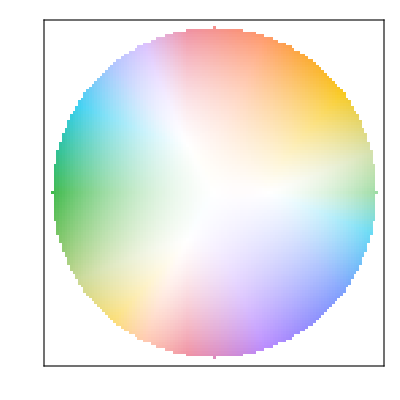
| K:p-d | K^′:p+d
p+ⅈ p
d-ⅈ d | -Graphics- | -Graphics-
p-ⅈ p
d+ⅈ d | -Graphics- | -Graphics-

```mathematica
Style[TableForm[Table[ComplexMatrixPlot[Reverse@Transpose@Table[f[((kx+ⅈ ky)+s((kx^2-ky^2)-ⅈ 2 kx ky))]Boole[Norm[{kx,ky}]≤3],{kx,-3,3,0.05},{ky,-3,3,0.05}],FrameTicks->False,ImageSize->60],{f,{Identity,Conjugate}},{s,{-1,1}}],
TableHeadings->{{"\!\(p+ⅈ p\)\n\!\(d-ⅈ d\)","\!\(p-ⅈ p\)\n\!\(d+ⅈ d\)"},{"\!\(K:p-d\)","\!\(\(K\^′\):p+d\)"}}],14,SingleLetterItalics->True,FontFamily->"CMU"]
```

In this case the valley-orbital wave function is antisymmetric, we must put the spin into triplet pairing

Δ_t=c_(K+k) ϵ σ c_(K'-k)-c_(K'-k)ϵ σc_(K+k).

Fermi surfaces have three-fold nodal lines.

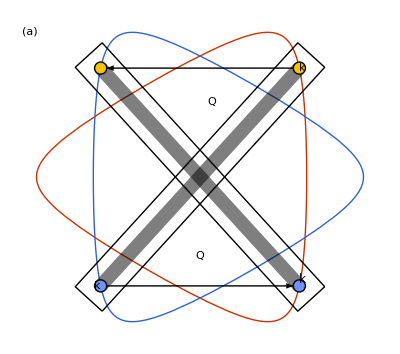
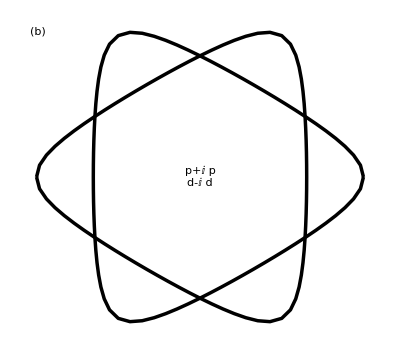
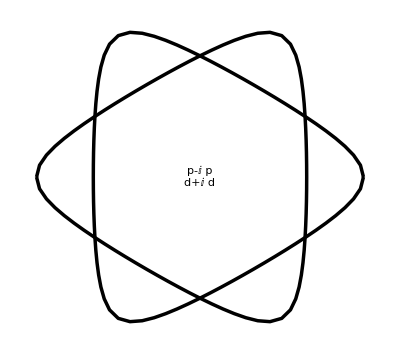
-Graphics--Graphics--Graphics--Graphics-

```mathematica
Row[{Block[{μ=1,α=1/3,FS,k1,k2,pair},
Block[{kF,t0,t1},
kF=FSOrbit[α,μ];
{{t0,t1}}=kF@"Domain";
{k1,k2}=kF/@Rescale[{0.6,0.4},{0,1},{t0,t1}];
FS=Cases[ParametricPlot[kF[t0+λ(t1-t0)],{λ,0,1}],_Line,∞]];
pair[k_]:={{AbsoluteThickness[10],Opacity[0.5],Line[{-k,{0,0},k},VertexColors->(ComplexColor/@{-ⅈ,0,ⅈ})]},{EdgeForm[Directive[Black,AbsoluteThickness[1]]],{ComplexColor[#1],Disk[#2 k,0.05]}&@@@{{ⅈ,1},{-ⅈ,-1}},
{Opacity[0],Block[{d=0.15},Rotate[Rectangle[{-1.12Norm[k],-d},{1.12Norm[k],d},RoundingRadius->d],ArcTan@@k,{0,0}]]}}};
Graphics[{{Red,FS,Blue,Scale[FS,{-1,1},{0,0}]},{pair/@{k1,-k2}},
{Arrowheads[{0.12}],Arrow[{-k1+{0.05,0},k2-{0.05,0}}],Arrow[{k1-{0.05,0},-k2+{0.05,0}}]},{Text["\!\(Q\_1\)",{0,-0.65}],Text["\!\(-Q\_1\)",{0.1,0.62}],Text["\!\(k\)",k1,{-2.2,0.2}],Text["\!\(-k\)",-k1,{1.8,0.2}],Text[Style["\!\(-k+Q\_1\)",12],k2,{-1.2,-0.6}]},Text["(a)",Scaled[{0,1}],{-0.2,1}]},ImageSize->{Automatic,80}]],Block[{α=1/3,μ=1,Nk=72,g1,g2,v,Kks,Kps,g,eigs},
g1[{qx_,qy_}]:=Abs@(qx^3-3qx qy^2)/((qx^2+qy^2-2μ)^2+1)+1;
g2[{qx_,qy_}]:=(qx^3-3qx qy^2)/((qx^2+qy^2-2μ)^2+1);
v[{kx_,ky_}]:={2kx+3α(kx^2-ky^2),2ky-6α kx ky};
Kks=Block[{k,t0,t1,ts,dt,vs,eq},
k=FSOrbit[α,μ];
{{t0,t1}}=k@"Domain";dt=(t1-t0)/120;
vs=Table[Norm@v[k[t]],{t,t0+dt/2,t1,dt}];
eq=Interpolation[Thread@{#/Max[#]&@Prepend[Accumulate@vs,0],Range[t0,t1,dt]}];
k/@eq/@Most@Range[0,1,1/Nk]];
Kps=-Kks;
g=1/(2π)Transpose@MapThread[Times,{Join[#,#]&[1/(Norm/@v/@Kks)],ArrayFlatten[{{0,Table[g1[#]+g2[#]&[Kk-Kp],{Kk,Kks},{Kp,Kps}]},
{Table[g1[#]-g2[#]&[Kp-Kk],{Kp,Kps},{Kk,Kks}],0}}]}];
eigs=Reverse@SortBy[First]@Thread@Eigensystem@g;
eigs⟦{2,3},2⟧=ⅈ{{1,ⅈ},{1,-ⅈ}}.{{1,1},{1,-1}}.eigs⟦{2,3},2⟧;
eigs⟦{10,11},2⟧=ⅈ{{1,ⅈ},{1,-ⅈ}}.eigs⟦{10,11},2⟧;
Row[{Row[Graphics[Append[First@#1,{Text[Style[#2,LineSpacing->{1,-1}]],#3}],List@@Rest@#1]&@@@Thread@{Graphics[{AbsoluteThickness[2.5],Block[{Δ=#2,close},
Δ=Partition[#/Max[Abs@#]&@Δ,Nk];
close[xs_]:=Append[xs,First@xs];
MapThread[Line[close@#1,VertexColors->close[ComplexColor/@#2]]&,{{Kks,Kps},Δ}]]},ImageSize->{Automatic,80}]&@@@eigs⟦{2,3}⟧,{"\!\(p+ⅈ p\)\n\!\(d-ⅈ d\)","\!\(p-ⅈ p\)\n\!\(d+ⅈ d\)"},{Text["(b)",Scaled[{0,1}],{-1,1}],{}}}],
Graphics[{Raster[List/@List@@@ComplexColor/@Exp[ⅈ Range[0,2π,π/24]],{{-0.3,0},{0,2π}}],AbsoluteThickness[1],Translate[{Line[{{0,0},{0.2,0}}],Text[Style["\!\("<>#2<>"\)",12],{0.4,0},{-1,0}]},{0,#}]&@@@{{0,"0"},{π,"π"},{2π,"2π"}},Text["\!\(Δ\_k\%μ\) phase",{1.2,π},{0,-1},{0,-1}]},ImageSize->{Automatic,80}]},Spacer[0.1]]
]}]
```

#### Landau-Ginzburg Theory

Denote the leading form factor as

w_k=w_d k_+^2+w_p k_-^2, w_k^*=w_d k_-^2+w_p k_+^2.

General pairing gap

Δ_k^μ=u^μ w_k+v^μ w_k^*,

In the BdG Hamiltonian

H_BdG=∑_k ψ_k^†h_BdG ψ_k, ψ_k=(c_(K k)
ⅈ σ^2 c_(K'-k)),
h_BdG=(ξ_k | Δ_k^†
Δ_k | -ξ_k).

Let γ^μ=(σ^0,ⅈ σ^1,ⅈ σ^2,ⅈ σ^3), then the gap matrix

Δ_k=Δ_k^μ γ^μ
=w_k u^μ γ^μ+w_k^*v^μ γ^μ.

Since ξ_k is trivial in the spin space, so the SC gap is purely determined by the singular value of Δ_k. As Δ_k is a 2×2 matrix, there will be two singular values, corresponding to the gap of the two spin components. These two singular values must be optimized independently.

Suppose δ_(1k) and δ_(2k) are two singular values of Δ_k, the LG theory is given by

F=∑_k r (δ_(1k)^2+δ_(2k)^2)+g (δ_(1k)^4+δ_(2k)^4)+…,
=∑_k r Tr Δ_k^†Δ_k+g Tr Δ_k^†Δ_k Δ_k^†Δ_k+….

Let γ^μ=(σ^0,ⅈ σ^1,ⅈ σ^2,ⅈ σ^3), then Δ_k=Δ_k^μ γ^μ, substitute into Eq. (DisplayFormulaNumbered)

Tr Δ_k^†Δ_k=Δ_k^(μ*)Δ_k^ν Tr γ^(μ†)γ^ν=Δ_k^(μ*)Δ_k^μ,

Tr Δ_k^†Δ_k Δ_k^†Δ_k=Δ_k^(μ*)Δ_k^ν Δ_k^(κ*)Δ_k^λ Tr γ^(μ†)γ^ν γ^(κ†)γ^λ
=Δ_k^(μ*)Δ_k^ν Δ_k^(κ*)Δ_k^λ(δ^μν δ^κλ-δ^μκ δ^νλ+δ^μλ δ^νκ-ϵ^μνκλ)
=Δ_k^(μ*)Δ_k^μ Δ_k^(ν*)Δ_k^ν-Δ_k^(μ*)Δ_k^ν Δ_k^(μ*)Δ_k^ν+Δ_k^(μ*)Δ_k^ν Δ_k^(ν*)Δ_k^μ
=2(Δ_k^(μ*)Δ_k^μ)^2-(|Δ_k^μ Δ_k^μ|)^2.

```mathematica
Block[{γs,R,G},
γs={σ[0],ⅈ σ[1],ⅈ σ[2],ⅈ σ[3]};
R=Table[σTr[σHermitian[γ1]·γ2]/2,{γ1,γs},{γ2,γs}];
G=Table[σTr[σHermitian[γ1]·γ2·σHermitian[γ3]·γ4]/2,{γ1,γs},{γ2,γs},{γ3,γs},{γ4,γs}];
{ArrayRules[R-Table[KroneckerDelta[μ,ν],{μ,4},{ν,4}]],
ArrayRules[G-Table[KroneckerDelta[μ,ν]KroneckerDelta[κ,λ]-KroneckerDelta[μ,κ]KroneckerDelta[ν,λ]+KroneckerDelta[μ,λ]KroneckerDelta[ν,κ]-Signature[{μ,ν,κ,λ}],{μ,4},{ν,4},{κ,4},{λ,4}]]}]
```

{{{_,_}→0},{{_,_,_,_}→0}}

Evaluate Tr.

Therefore Eq. (DisplayFormulaNumbered) becomes

F=∑_k r Δ_k^(μ*)Δ_k^μ+g (2(Δ_k^(μ*)Δ_k^μ)^2-(|Δ_k^μ Δ_k^μ|)^2)+….

As we sum over momentum on the Fermi surface, to the lowest fourth order, only the following terms survives

∑_(k∈FS) w_k^*w_k=A,∑_(k∈FS) w_k^(*2)w_k^2=B,∑_(k∈FS) w_k^3=C,…

All the other terms will vanish. (In fact, C will never be used in the calculation, but we just list it anyway. It arises from the anisotropy of the FS.)

With this, according to Eq. (DisplayFormulaNumbered), we have

∑_k Δ_k^(μ*)Δ_k^μ=A(u^(μ*)u^μ+v^(μ*)v^μ),
∑_k (Δ_k^(μ*)Δ_k^μ)^2=B((u^(μ*)u^μ+v^(μ*)v^μ)^2+2(|u^(μ*)v^μ|)^2),
∑_k (|Δ_k^μ Δ_k^μ|)^2=B(4(|u^μ v^μ|)^2+(|u^μ u^μ|)^2+(|v^μ v^μ|)^2),

```mathematica
Block[{ω,e,uv},
ω={Exp[ⅈ],Exp[-ⅈ]};
e=Conjugate[ω]⊗ω⊗Conjugate[ω]⊗ω/._Power->0;
uv[μ_]:={Indexed[u,μ],Indexed[v,μ]};
Expand@tTr[{e,Conjugate[uv[μ]],uv[μ],Conjugate[uv[ν]],uv[ν]},{{1,5},{2,6},{3,7},{4,8}}]
]
```

Conjugate[uμ] Conjugate[uν] uμ uν+Conjugate[uν] Conjugate[vμ] uν vμ+Conjugate[uμ] Conjugate[vν] uν vμ+Conjugate[uν] Conjugate[vμ] uμ vν+Conjugate[uμ] Conjugate[vν] uμ vν+Conjugate[vμ] Conjugate[vν] vμ vν

Details1

```mathematica
Block[{ω,e,uv},
ω={Exp[ⅈ],Exp[-ⅈ]};
e=Conjugate[ω]⊗ω⊗Conjugate[ω]⊗ω/._Power->0;
uv[μ_]:={Indexed[u,μ],Indexed[v,μ]};
Expand@tTr[{e,Conjugate[uv[μ]],uv[ν],Conjugate[uv[μ]],uv[ν]},{{1,5},{2,6},{3,7},{4,8}}]
]
```

Conjugate[uμ]^2 uν^2+4 Conjugate[uμ] Conjugate[vμ] uν vν+Conjugate[vμ]^2 vν^2

Details2.

Therefore Eq. (DisplayFormulaNumbered) becomes

F=r(u^(μ*)u^μ+v^(μ*)v^μ)+g (2(u^(μ*)u^μ+v^(μ*)v^μ)^2+4(|u^(μ*)v^μ|)^2-4(|u^μ v^μ|)^2-(|u^μ u^μ|)^2-(|v^μ v^μ|)^2)+….

Find F minimum, and calculate the zero gradient perturbations around the saddle point. Here we assume that u and v are complex O(2) vectors (the result can be easily generalized to O(4) vectors)

Generic search

```mathematica
Block[{F,psol},
F[p_List]:=Block[{u,v},
{u,v}=ArrayReshape[p,{2,2,2}].{1,ⅈ};
-2(Conjugate[u].u+Conjugate[v].v)+2(Conjugate[u].u+Conjugate[v].v)^2+4Abs[Conjugate[u].v]^2-Abs[u.u]^2-4Abs[u.v]^2-Abs[v.v]^2];
psol=Block[{p1,p2,p3,p4,p5,p6,p7,p8,ps,init},
ps={p1,p2,p3,p4,p5,p6,p7,p8};
init=Thread[{ps,Flatten[ReIm/@Flatten[RandomComplex[{-1-ⅈ,1+ⅈ},{2,2}]]]}];
ps/.Last@FindMinimum[F[ps],init,AccuracyGoal->7]];
(* gauge fixing *)
On[Assert];
Block[{chop,u,v,u2,v2,type},
chop=Chop[#,1*^-6]&;
{u,v}=chop[ArrayReshape[psol,{2,2,2}].{1,ⅈ}];
{u2,v2}={Conjugate[u].u,Conjugate[v].v};
type=If[u2==0,"A1",If[v2==0,"A2",If[chop[u2-v2]==0.,"B","C"]]];
Switch[type,
"A1",
v=chop[v/Sign@First@MaximalBy[v,Abs]];
Assert[Im[v]=={0,0}];
v=chop[RotationMatrix[-ArcTan@@v].v];,
"A2",
u=chop[u/Sign@First@MaximalBy[u,Abs]];
Assert[Im[u]=={0,0}];
u=chop[RotationMatrix[-ArcTan@@u].u];,
"B",
u=chop[u/Sign@First@u];
v=chop[v/Sign@First@v];
Assert[chop[Re[u]-Re[v]]=={0,0}];
Assert[chop[Im[u]+Im[v]]=={0,0}];
Assert[chop[Re[u].Im[u]]==0];
{u,v}=chop[RotationMatrix[{Re[u],{1,0}}].#&/@{u,v}]];
<|"type"->type,"F"->chop@F[Flatten[ReIm/@Flatten[{u,v}]]],"u"->u,"v"->v|>]]
```

<|type→B,F→-1.,u→{0.5,0.-0.5 ⅈ},v→{0.5,0.+0.5 ⅈ}|>

The chiral solution

u^μ=e^(ⅈ ϕ)n^μ
v^μ=0 or u^μ=0
v^μ=e^(ⅈ ϕ)n^μ.

The non-chiral solution

u^μ=e^(ⅈ ϕ_1)(n_1^μ+ⅈ n_2^μ)
v^μ=e^(ⅈ ϕ_2)(n_1^μ-ⅈ n_2^μ)

To go beyond BCS

F=∑_k r Δ_k^(μ*)Δ_k^μ+∑_(k_1,k_2) g (k_1-k_2)(2 Δ_k_1^(μ*)Δ_k_1^μ Δ_k_2^(ν*)Δ_k_2^ν-Δ_k_1^(μ*)Δ_k_1^(μ*)Δ_k_2^ν Δ_k_2^ν)+….

Define

g_1=∑_(k_1,k_2) g (k_1-k_2)(|w_k_1|)^2(|w_k_2|)^2,
g_2=∑_(k_1,k_2) g (k_1-k_2)w_k_1^(*2)w_k_2^2.

```mathematica
Block[{α=1/3,q0=0.1,q1=1.9,w,g,ω,ks,e,uv},
w[k:{kx_,ky_}]:=(kx+ⅈ ky)^2+(kx-ⅈ ky);
g[q_]:=1/(((Norm[q]-q1)/q0)^2+1);
ω[k_]:={w[k],Conjugate[w[k]]};
ks=Block[{n=48,kF,t0,t1},
kF=FSOrbit[α,1];
{{t0,t1}}=kF@"Domain";
Table[kF[t0+λ(t1-t0)],{λ,1/n,1,1/n}]];
{Chop[Sum[g[k1-k2]Abs[w[k1]]^2Abs[w[k2]]^2,{k1,ks},{k2,ks}]/Length[ks]^2],Chop[Sum[g[k1-k2]Conjugate[w[k1]]^2w[k2]^2,{k1,ks},{k2,ks}]/Length[ks]^2]}
]
```

{0.279273,-0.181026}

Example

g_2 can be negative.

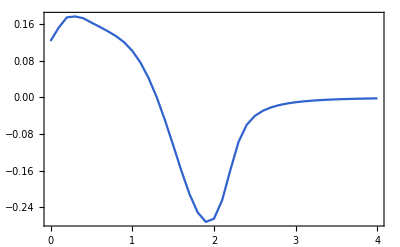

```mathematica
Block[{α=1/3,w,g,ω,ks,e,uv,y},
w[k:{kx_,ky_}]:=(kx+ⅈ ky)^2+(kx-ⅈ ky);
ω[k_]:={w[k],Conjugate[w[k]]};
ks=Block[{n=48,kF,t0,t1},
kF=FSOrbit[α,1];
{{t0,t1}}=kF@"Domain";
Table[kF[t0+λ(t1-t0)],{λ,1/n,1,1/n}]];
g[q_,q0_,q1_]:=1/(((Norm[q]-q1)/q0)^2+1);
ListLinePlot[Table[{q1,Chop[Sum[g[k1-k2,0.2,q1]Conjugate[w[k1]]^2w[k2]^2,{k1,ks},{k2,ks}]/Length[ks]^2]},{q1,0,4,0.1}],PlotRange->All]]
```

Using this

∑_(k_1,k_2) g (k_1-k_2)Δ_k_1^(μ*)Δ_k_1^μ Δ_k_2^(ν*)Δ_k_2^ν=g_1(u^(μ*)u^μ+v^(μ*)v^μ)^2+2 g_2(|u^(μ*)v^μ|)^2,

```mathematica
Block[{α=1/3,q0=0.1,q1=1.9,w,g,ω,ks,e,uv},
w[k:{kx_,ky_}]:=(kx+ⅈ ky)^2+(kx-ⅈ ky);
g[q_]:=1/(((Norm[q]-q1)/q0)^2+1);
ω[k_]:={w[k],Conjugate[w[k]]};
ks=Block[{n=48,kF,t0,t1},
kF=FSOrbit[α,1];
{{t0,t1}}=kF@"Domain";
Table[kF[t0+λ(t1-t0)],{λ,1/n,1,1/n}]];
e=Chop[Sum[g[k1-k2]Conjugate[ω[k1]]⊗ω[k1]⊗Conjugate[ω[k2]]⊗ω[k2],{k1,ks},{k2,ks}]/Length[ks]^2,1*^-5];
uv[μ_]:={Indexed[u,μ],Indexed[v,μ]};
Expand@tTr[{e,Conjugate[uv[μ]],uv[μ],Conjugate[uv[ν]],uv[ν]},{{1,5},{2,6},{3,7},{4,8}}]
]
```

0.279273 Conjugate[uμ] Conjugate[uν] uμ uν+0.279273 Conjugate[uν] Conjugate[vμ] uν vμ-0.181026 Conjugate[uμ] Conjugate[vν] uν vμ-0.181026 Conjugate[uν] Conjugate[vμ] uμ vν+0.279273 Conjugate[uμ] Conjugate[vν] uμ vν+0.279273 Conjugate[vμ] Conjugate[vν] vμ vν

Demonstration.

∑_(k_1,k_2) g (k_1-k_2)Δ_k_1^(μ*)Δ_k_1^(μ*)Δ_k_2^ν Δ_k_2^ν=2(g_1+g_2)(|u^μ v^μ|)^2+g_1((|u^μ u^μ|)^2+(|v^μ v^μ|)^2).

```mathematica
Block[{α=1/3,q0=0.1,q1=1.9,w,g,ω,ks,e,uv},
w[k:{kx_,ky_}]:=(kx+ⅈ ky)^2+(kx-ⅈ ky);
g[q_]:=1/(((Norm[q]-q1)/q0)^2+1);
ω[k_]:={w[k],Conjugate[w[k]]};
ks=Block[{n=48,kF,t0,t1},
kF=FSOrbit[α,1];
{{t0,t1}}=kF@"Domain";
Table[kF[t0+λ(t1-t0)],{λ,1/n,1,1/n}]];
e=Chop[Sum[g[k1-k2]Conjugate[ω[k1]]⊗ω[k1]⊗Conjugate[ω[k2]]⊗ω[k2],{k1,ks},{k2,ks}]/Length[ks]^2,1*^-5];
uv[μ_]:={Indexed[u,μ],Indexed[v,μ]};
Expand@tTr[{e,Conjugate[uv[μ]],uv[ν],Conjugate[uv[μ]],uv[ν]},{{1,5},{2,6},{3,7},{4,8}}]
]
```

0.279273 Conjugate[uμ]^2 uν^2+0.196495 Conjugate[uμ] Conjugate[vμ] uν vν+0.279273 Conjugate[vμ]^2 vν^2

Demonstration.

After momentum summation

F=r(u^(μ*)u^μ+v^(μ*)v^μ)+2(g_1(u^(μ*)u^μ+v^(μ*)v^μ))^2+4 g_2(|u^(μ*)v^μ|)^2-2(g_1+g_2)(|u^μ v^μ|)^2-g_1((|u^μ u^μ|)^2+(|v^μ v^μ|)^2)+….

When g_2<0, the nematic state can be realized

```mathematica
Block[{r=-2,g1=1,g2=-0.1,F,psol},
F[p_List]:=Block[{u,v},
{u,v}=ArrayReshape[p,{2,2,2}].{1,ⅈ};
r(Conjugate[u].u+Conjugate[v].v)+2g1(Conjugate[u].u+Conjugate[v].v)^2+4g2 Abs[Conjugate[u].v]^2-2(g1+g2)Abs[u.v]^2-g1(Abs[u.u]^2+Abs[v.v]^2)];
psol=Block[{p1,p2,p3,p4,p5,p6,p7,p8,ps,init},
ps={p1,p2,p3,p4,p5,p6,p7,p8};
init=Thread[{ps,Flatten[ReIm/@Flatten[RandomComplex[{-1-ⅈ,1+ⅈ},{2,2}]]]}];
ps/.Last@FindMinimum[F[ps],init,AccuracyGoal->7]];
(* gauge fixing *)
On[Assert];
Block[{chop,u,v,u2,v2,type},
chop=Chop[#,1*^-6]&;
{u,v}=chop[ArrayReshape[psol,{2,2,2}].{1,ⅈ}];
{u2,v2}={Conjugate[u].u,Conjugate[v].v};
type=If[u2==0,"A1",If[v2==0,"A2",If[chop[u2-v2]==0.,"B","C"]]];
Switch[type,
"A1",
v=chop[v/Sign@First@MaximalBy[v,Abs]];
Assert[Im[v]=={0,0}];
v=chop[RotationMatrix[-ArcTan@@v].v];,
"A2",
u=chop[u/Sign@First@MaximalBy[u,Abs]];
Assert[Im[u]=={0,0}];
u=chop[RotationMatrix[-ArcTan@@u].u];,
"B",
u=chop[u/Sign@First@u];
v=chop[v/Sign@First@v];
Assert[chop[Re[u]-Re[v]]=={0,0}];
Assert[chop[Im[u]+Im[v]]=={0,0}];
Assert[chop[Re[u].Im[u]]==0];
{u,v}=chop[RotationMatrix[{Re[u],{1,0}}].#&/@{u,v}]];
<|"type"->type,"F"->chop@F[Flatten[ReIm/@Flatten[{u,v}]]],"u"->u,"v"->v|>]]
```

<|type→B,F→-1.05263,u→{0.725476,0},v→{0.725476,0}|>

##### Failed Attempt

To go beyond the BCS mean field theory, we can further consider that there are interactions between the Cooper pairs (this will be 8 fermion interactions), such that Eq. (DisplayFormulaNumbered) can be generalized to

F=∑_k r Tr Δ_k^†Δ_k+ ∑_(k_1,k_2) g(k_1-k_2)Tr Δ_k_1^†Δ_k_1 Δ_k_2^†Δ_k_2+….

Still following Eq. (DisplayFormulaNumbered), we get

F=∑_k r Δ_k^(μ*)Δ_k^μ+∑_(k_1,k_2) g(k_1-k_2) Δ_k_1^(μ*)Δ_k_1^ν Δ_k_2^(κ*)Δ_k_2^λ(δ^μν δ^κλ-δ^μκ δ^νλ+δ^μλ δ^νκ-ϵ^μνκλ)+….

The momentum average leads to

∑_k Δ_k^(μ*)Δ_k^ν=u^(μ*)u^ν+v^(μ*)v^ν

```mathematica
Block[{α=1/3,q0=0.4,q1=0.1,w,g,ω,ks,e,uv},
w[k:{kx_,ky_}]:=(kx+ⅈ ky)^2+(kx-ⅈ ky);
ω[k_]:={w[k],Conjugate[w[k]]};
ks=Block[{n=48,kF,t0,t1},
kF=FSOrbit[α,1];
{{t0,t1}}=kF@"Domain";
Table[kF[t0+λ(t1-t0)],{λ,1/n,1,1/n}]];
e=Chop[Sum[Conjugate[ω[k]]⊗ω[k],{k,ks}]/Length[ks],1*^-5];
uv[μ_]:={Indexed[u,μ],Indexed[v,μ]};
Expand@tTr[{e,Conjugate[uv[μ]],uv[ν]},{{1,3},{2,4}}]
]
```

1.30755 Conjugate[uμ] uν+1.30755 Conjugate[vμ] vν

Momentum sum.

∑_(k_1,k_2) g(k_1-k_2) Δ_k_1^(μ*)Δ_k_1^ν Δ_k_2^(κ*)Δ_k_2^λ=g_1(u^(μ*)u^ν+v^(μ*)v^ν)(u^(κ*)u^λ+v^(κ*)v^λ)+g_2(u^(μ*)v^ν v^(κ*)u^λ+v^(μ*)u^ν u^(κ*) v^λ).

```mathematica
Block[{α=1/3,q0=0.3,q1=0.1,w,g,ω,ks,e,uv},
w[k:{kx_,ky_}]:=(kx+ⅈ ky)^2+(kx-ⅈ ky);
g[q_]:=1/(((Norm[q]-q1)/q0)^2+1);
ω[k_]:={w[k],Conjugate[w[k]]};
ks=Block[{n=48,kF,t0,t1},
kF=FSOrbit[α,1];
{{t0,t1}}=kF@"Domain";
Table[kF[t0+λ(t1-t0)],{λ,1/n,1,1/n}]];
e=Chop[Sum[g[k1-k2]Conjugate[ω[k1]]⊗ω[k1]⊗Conjugate[ω[k2]]⊗ω[k2],{k1,ks},{k2,ks}]/Length[ks]^2,1*^-5];
uv[μ_]:={Indexed[u,μ],Indexed[v,μ]};
Expand@tTr[{e,Conjugate[uv[μ]],uv[ν],Conjugate[uv[κ]],uv[λ]},{{1,5},{2,6},{3,7},{4,8}}]
]
```

0.292096 Conjugate[uκ] Conjugate[uμ] uλ uν+0.292096 Conjugate[uμ] Conjugate[vκ] uν vλ+0.190582 Conjugate[uκ] Conjugate[vμ] uν vλ+0.190582 Conjugate[uμ] Conjugate[vκ] uλ vν+0.292096 Conjugate[uκ] Conjugate[vμ] uλ vν+0.292096 Conjugate[vκ] Conjugate[vμ] vλ vν

Momentum sum.

Now we plug this result into Eq. (DisplayFormulaNumbered),

F=r (u^(μ*)u^ν+v^(μ*)v^ν)+(g_1(u^(μ*)u^ν u^(κ*)u^λ+u^(μ*)u^ν v^(κ*)v^λ+v^(μ*)v^ν u^(κ*)u^λ+v^(μ*)v^ν v^(κ*)v^λ)+g_2(u^(μ*)v^ν v^(κ*)u^λ+v^(μ*)u^ν u^(κ*) v^λ))(δ^μν δ^κλ-δ^μκ δ^νλ+δ^μλ δ^νκ-ϵ^μνκλ)+….
=r (u^(μ*)u^ν+v^(μ*)v^ν)+g_1((2 u^(μ*)u^μ u^(ν*)u^ν+2 u^(μ*)u^μ v^(ν*)v^ν+u^(μ*)v^μ v^(ν*)u^ν+v^(μ*)u^μ u^(ν*)v^ν+2 v^(μ*)v^μ v^(ν*)v^ν)-(u^(μ*)u^ν u^(μ*)u^ν+u^(μ*)u^ν v^(μ*)v^ν+v^(μ*)v^ν u^(μ*)u^ν+v^(μ*)v^ν v^(μ*)v^ν)-2 ϵ^μνκλ u^(μ*)u^ν v^(κ*)v^λ)+g_2((u^(μ*)v^μ v^(ν*)u^ν+v^(μ*)u^μ u^(ν*) v^ν)-(u^(μ*)v^ν v^(μ*)u^ν+v^(μ*)u^ν u^(μ*) v^ν)+(u^(μ*)u^μ v^(ν*)v^ν+v^(μ*)v^μ u^(ν*)u^ν )-2 u^(μ*)v^ν v^(κ*)u^λ ϵ^μνκλ)+….

```mathematica
Block[{r=-2,g1=1,g2=0.5,F,psol},
F[p_List]:=Block[{u,v},
{u,v}=ArrayReshape[p,{2,2,2}].{1,ⅈ};
r(Conjugate[u].u+Conjugate[v].v)+2g1((Conjugate[u].u)^2+(Conjugate[v].v)^2)+2(g1+g2)(Conjugate[u].u)(Conjugate[v].v)+2(g1+g2)Abs[Conjugate[u].v]^2-2(g1+g2)Abs[u.v]^2-g1(Abs[u.u]^2+Abs[v.v]^2)];
psol=Block[{p1,p2,p3,p4,p5,p6,p7,p8,ps,init},
ps={p1,p2,p3,p4,p5,p6,p7,p8};
init=Thread[{ps,Flatten[ReIm/@Flatten[RandomComplex[{-1-ⅈ,1+ⅈ},{2,2}]]]}];
ps/.Last@FindMinimum[F[ps],init,AccuracyGoal->7]];
(* gauge fixing *)
On[Assert];
Block[{chop,u,v,u2,v2,type},
chop=Chop[#,1*^-6]&;
{u,v}=chop[ArrayReshape[psol,{2,2,2}].{1,ⅈ}];
{u2,v2}={Conjugate[u].u,Conjugate[v].v};
type=If[u2==0,"A1",If[v2==0,"A2",If[chop[u2-v2]==0.,"B","C"]]];
Switch[type,
"A1",
v=chop[v/Sign@First@MaximalBy[v,Abs]];
Assert[Im[v]=={0,0}];
v=chop[RotationMatrix[-ArcTan@@v].v];,
"A2",
u=chop[u/Sign@First@MaximalBy[u,Abs]];
Assert[Im[u]=={0,0}];
u=chop[RotationMatrix[-ArcTan@@u].u];,
"B",
u=chop[u/Sign@First@u];
v=chop[v/Sign@First@v];
Assert[chop[Re[u]-Re[v]]=={0,0}];
Assert[chop[Im[u]+Im[v]]=={0,0}];
Assert[chop[Re[u].Im[u]]==0];
{u,v}=chop[RotationMatrix[{Re[u],{1,0}}].#&/@{u,v}]];
<|"type"->type,"F"->chop@F[Flatten[ReIm/@Flatten[{u,v}]]],"u"->u,"v"->v|>]]
```

<|type→A1,F→-1.,u→{0,0},v→{1.,0}|>

#### Symmetry Analysis

##### Without SC

Without SC, we have the (U(1))_c×(U(1))_v×SO(4) symmetry

(U(1))_c:σ^002,
(U(1))_v:σ^302,
SO(4):σ^012,σ^020,σ^032,σ^312,σ^320,σ^332

Time reversal

spin independent

ℤ_2^𝒯:χ→𝒦 σ^103 χ,

involving spin

ℤ_2^𝒯_s:χ→𝒦 σ^223 χ.

##### Type A: Chiral TSC

Assuming n^μ=(1,0,0,0) in the singlet channel,

Δ_k=w_k c_(K k)ⅈ σ^2 c_(K'-k)

The mean field Hamiltonian in the Majorana basis

h=β_k σ^002+α_k σ^300+Re w_k σ^223+Im w_k σ^221
≃ⅈ ∂_x σ^223+ⅈ ∂_y σ^221+m σ^002

The remaining O(3) vector (triplet) pairing

Re Δ:σ^131,σ^103,σ^111
Im Δ:σ^133,σ^101,σ^113

In the TSC phase

Remaining symmetry

ℤ_2^F:χ→-χ,
(U(1))_v:σ^302,
(SO(3))_+:σ^012,σ^020,σ^032 (corotation)

Broken symmetry

(SO(3))_-:σ^312,σ^320,σ^332,
ℤ_2^𝒯:χ→𝒦 σ^103 χ,
ℤ_2^𝒯_s:χ→𝒦 σ^223 χ.

Note: no time reversal symmetry can be implement in this case, because the momentum and mass terms σ^223,σ^221,σ^002 product to σ^000, thus no additional matrix can be found to anticommute with all three of them.

Two routes of implementing the ℤ_2 ⇒ therefore the ℤ_2 symmetry is not an additional symmetry but a subgroup in (U(1))_v×(SO(3))_+.

χ⟶^((SO(3))_-)ⅈ σ^332 χ⟶^((U(1))_c)σ^330χ,
χ⟶^((SO(3))_+)ⅈ σ^032 χ⟶^((U(1))_v)σ^330χ.

After projection to topological order, we have the additional gauge group generated by

(U(1))_c⊂(SU(2))_g:σ^021,σ^023,σ^002

But the momentum and the mass terms k_x σ^223+k_y σ^221+m σ^002+α σ^300 has already broken the gauge structure to ℤ_2, none of the ℤ_4 subgroup of (SU(2))_g can keep the kinetic term invariant. Unlike in the SMG story, the gapless Dirac fermion preserves the full (SU(2))_g, therefore we can use the ℤ_4 gauge subgroup to implement some improper ℤ_2 transformation of the O(n) vector. But here if we want to use ℤ_4 gauge subgroup to do the same thing, additional transformation must be applied to the momentum. For example, if we take the χ→ⅈ σ^002χ, then this gauge transformation must be followed by k→-k according to the momentum term. It seems to be an inversion symmetry, but α σ^300 breaks this inversion symmetry explicitly, so there is no way to keep the mean field Hamiltonian invariant, while reflecting the O(3) vector. So the improper ℤ_2 does not exist even on the PSG level.

##### Type B: Helical TSC

Assuming n_1^μ=(0,1,0,0), n_2^μ=(0,0,1,0) in the triplet channel,

Δ_k=c_(K k)(w_k(σ^0-σ^3)/2+w_k^*(σ^0+σ^3)/2)c_(K'-k)
=c_(K k)(Re w_k σ^0-ⅈ Im w_k σ^3)c_(K'-k)

The mean field Hamiltonian in the Majorana basis

h=β_k σ^002+α_k σ^300+Re w_k σ^103+Im w_k σ^131
≃ⅈ ∂_x σ^103+ⅈ ∂_y σ^131+m σ^002

The remaining O(2) vector (triplet) pairing

Re Δ:σ^223,σ^111
Im Δ:σ^221,σ^113

In the TSC phase

Remaining symmetry

ℤ_2^F:χ→-χ,
(U(1))_v:σ^302,
SO(2):σ^332 (conterrotation),
ℤ_2^𝒯_s:χ→𝒦 σ^223 χ, χ→𝒦 ⅈ σ^213 χ.

Broken symmetry

SO(4)/SO(2):σ^012,σ^020,σ^032,σ^312,σ^320,
ℤ_2^𝒯:χ→𝒦 σ^103 χ.

Two routes of implementing the ℤ_2 ⇒ therefore the ℤ_2 symmetry is not an additional symmetry but a subgroup in (U(1))_v×SO(2).

χ⟶^(SO(4)/SO(2))ⅈ σ^032 χ⟶^((U(1))_c)σ^030χ,
χ⟶^(SO(2))ⅈ σ^332 χ⟶^((U(1))_v)σ^030χ.

#### Time-Reversal Symmetry for Helical State

Starting form the definition

Δ_k=(u^μ w_k+v^μ w_k^*)c_Kk ᵀⅈ σ^2 σ^μ c_(K'-k).

For helical TSC state,

u^μ=e^(ⅈ ϕ_1)(n_1^μ+ⅈ n_2^μ),v^μ=e^(ⅈ ϕ_2)(n_1^μ-ⅈ n_2^μ).

We assume that ϕ_1=ϕ_2=0. Substitute Eq. (DisplayFormulaNumbered) into Eq. (DisplayFormulaNumbered),

Δ_k=2(n_1^μ Re w_k-n_2^μ Im w_k)c_Kk ᵀⅈ σ^2 σ^μ c_(K'-k).

Both Re w_k and Im w_k are real.

For p-wave, w_k=-w_-k. For d-wave w_k=-w_-k.

We propose the time-reversal symmetry

𝒯:c_(K k)→𝒦 ⅈ σ^2 c_(K'-k), c_(K' k)→𝒦 ⅈ σ^2 c_(K-k),

we can show that under this time-reversal

c_Kk ᵀⅈ σ^2 σ^μ c_(K'-k)→c_(K'-k)ᵀ(ⅈ σ^2)ᵀ(ⅈ σ^2 σ^μ)^*ⅈ σ^2 c_Kk
=-c_Kk ᵀ(ⅈ σ^2)ᵀ(ⅈ σ^2 σ^μ)^†ⅈ σ^2 c_(K'-k)
=c_Kk ᵀⅈ σ^2 σ^μ c_(K'-k).

```mathematica
-σTranspose[ⅈ σ[2]]·σHermitian[ⅈ σ[2]·σ[#]]·(ⅈ σ[2])==ⅈ σ[2]·σ[#]&/@Range[0,3]
```

{True,True,True,True}

Verification.

In the Majorana basis

d-wave

Δ^μ=(σ^121,σ^231,σ^203,σ^211), 𝒯=𝒦 ⅈ σ^123.

```mathematica
Abstract@ArrayFlatten[{{0,Represent[-σTranspose[ⅈ σ[2]·σ[#]]]},{Represent[ⅈ σ[2]·σ[#]],0}}]&/@Range[0,3]
```

{ⅈ σ[1,2],-ⅈ σ[2,3],σ[2,0],ⅈ σ[2,1]}

Details.

p-wave

Δ^μ=(σ^223,σ^133,σ^101,σ^113), 𝒯=𝒦 ⅈ σ^123.

```mathematica
Abstract@ArrayFlatten[{{0,Represent[σTranspose[ⅈ σ[2]·σ[#]]]},{Represent[ⅈ σ[2]·σ[#]],0}}]&/@Range[0,3]
```

{σ[2,2],σ[1,3],ⅈ σ[1,0],-σ[1,1]}

Details.

In conclusion, there exist a universal time-reversal 𝒯=𝒦 ⅈ σ^123 that applies for both d-wave and p-wave and satisfies 𝒯^2=-1.

#### Symmetry Fractionalization on Visons

##### Type A Chiral TSC

Starting from the p+ⅈ p

h=ⅈ ∂_x σ^223+ⅈ ∂_y σ^221+m σ^002,
U(1)_v:σ^302,
SO(3):σ^012,σ^020,σ^032

Under basis transformation,

h=ⅈ ∂_x σ^003+ⅈ ∂_y σ^001+m σ^002,
U(1)_v:σ^200,
SO(3):σ^210,σ^020,σ^230

```mathematica
Column@Normal@AssociationMap[OrthogonalTransform[C4[σ[2,2,2]],C4[σ[3,2,0]],C4[-σ[0,2,0]],C4[-σ[0,0,2]]],{kx σ[2,2,3],ky σ[2,2,1],m σ[0,0,2],Qv σ[3,0,2],Sx σ[0,1,2],Sy σ[0,2,0],Sz σ[0,3,2]}]
```

kx σ[2,2,3]→kx σ[0,0,3]
ky σ[2,2,1]→ky σ[0,0,1]
m σ[0,0,2]→m σ[0,0,2]
Qv σ[3,0,2]→Qv σ[2,0,0]
Sx σ[0,1,2]→Sx σ[2,1,0]
Sy σ[0,2,0]→Sy σ[0,2,0]
Sz σ[0,3,2]→Sz σ[2,3,0]

Basis transformation.

Vison - π flux for all fermions. Apply the following projection to the vison core

P=1+σ^001 e^(ⅈ θ σ^002),

Hilbert space dimension: 8→4, we obtain 4 Majorana zero modes

Both (U(1))_v and SO(3) survives as

U(1)_v:σ^20,
SO(3):σ^21,σ^02,σ^23

Now we switch to a the many body basis in the vison core. The symmetry generators are represented as

U(1)_v:σ^12-σ^21,
SO(3):σ^11-σ^22,σ^03+σ^30,-σ^12-σ^21.

```mathematica
Block[{χ,rep},
χ=AssociationThread[Range@Length@#->#]&@Cl[4];
rep[a_]:=Total[#2/2 CenterDot@@χ/@#1&@@@Most@ArrayRules@Represent@a];
rep/@{σ[2,0],σ[2,1],σ[0,2],σ[2,3]}
]
```

{σ[1,2]-σ[2,1],σ[1,1]-σ[2,2],σ[0,3]+σ[3,0],-σ[1,2]-σ[2,1]}

Representation.

The most generic Hamiltonian that preserves these symmetries is represented as

H=σ^33=-χ_1 χ_2 χ_3 χ_4.

```mathematica
Block[{χ,rep},
χ=AssociationThread[Range@Length@#->#]&@Cl[4];
rep[a_]:=Total[#2/2 CenterDot@@χ/@#1&@@@Most@ArrayRules@Represent@a];
σSelect[CommuteQ/@rep/@{σ[2,0],σ[2,1],σ[0,2],σ[2,3]}]
]
```

{σ[0,0],σ[3,3]}

Select interaction.

The Hamiltonian itself is also the Fermi parity operator in the vison core, which splits the many-body space into even and odd fermion parity sectors.

Odd parity sector

U(1)_v:0,
SO(3):σ^1,σ^2,σ^3.

Even parity sector

U(1)_v:σ^2 (q=±1),
SO(3):0,0,0.

```mathematica
Block[{χ,rep,Qs,hs,H,w,U},
χ=AssociationThread[Range@Length@#->#]&@Cl[4];
rep[a_]:=Total[#2/2 CenterDot@@χ/@#1&@@@Most@ArrayRules@Represent@a];
Qs=rep/@{σ[2,0]/2,σ[2,1]/4,σ[0,2]/4,σ[2,3]/4};
hs=σSelect[CommuteQ/@Qs];
H=hs.RandomReal[{0,1},Length@hs];
{w,U}=Thread@SortBy[First]@Thread@Eigensystem@Represent@H;
Thread[{"H","Qv","Sx","Sy","Sz"}->(ComplexMatrixPlot[Conjugate[U].Represent[#].Transpose[U],Mesh->All,FrameTicks->None,ImageSize->40]&/@Prepend[Qs,H])]
]
```

{H→-Graphics-,Qv→-Graphics-,Sx→-Graphics-,Sy→-Graphics-,Sz→-Graphics-}

Diagonalize Hamiltonian.

If we extend the calculation to d+ⅈ d, we found that

Odd parity sector: 8 states (same representation as fermions)

(U(1))_v | q=+1 | q=-1
SO(3) | 2_sp | 2_sp
mul. | ×2 | ×2

Even parity sector: 8 states (representations that can become trivial)

(U(1))_v | q=0 |  | q=2 | q=-2
SO(3) | 1_sc | 3_ve | 1_sc | 1_sc
mul. | ×3 | ×1 | ×1 | ×1

```mathematica
Block[{χ,rep,Qs,hs,H,w,U,PF},
χ=AssociationThread[Range@Length@#->#]&@Cl[8];
rep[a_]:=Total[#2/2 CenterDot@@χ/@#1&@@@Most@ArrayRules@Represent@a];
Qs=rep/@{σ[0,2,0]/2,σ[0,2,1]/4,σ[0,0,2]/4,σ[0,2,3]/4};
hs=σSelect[CommuteQ/@Qs];
H=hs.RandomReal[{0,1},Length@hs];
{w,U}=Thread@SortBy[First]@Thread@Eigensystem@Represent@H;
PF=CenterDot@@χ;
U=ArrayFlatten@Table[Block[{Up,proj},
Up=Cases[U,u_/;s Conjugate[u].Represent[PF].u>0];
proj=Conjugate[Up].Represent[#].Transpose[Up]&;
Up=(Last@Thread@SortBy[First]@Thread@Eigensystem[100proj[H]+10proj[First@Qs]+(#1.#1+#2.#2+#3.#3+0.1#3&@@(proj/@Rest@Qs))]).Up;
{Up}],{s,{-1,1}}];
Thread[{"PF","H","Qv","Sx","Sy","Sz"}->(ComplexMatrixPlot[Conjugate[U].Represent[#].Transpose[U],Mesh->All,FrameTicks->None,ImageSize->100]&/@Join[{CenterDot@@χ,H},Qs])]
]
```

{PF→-Graphics-,H→-Graphics-,Qv→-Graphics-,Sx→-Graphics-,Sy→-Graphics-,Sz→-Graphics-}

Diagonalize Hamiltonian.

##### Type B Helical TSC

Starting from the p+ⅈ p

h=ⅈ ∂_x σ^103+ⅈ ∂_y σ^131+m σ^002,
U(1)_v:σ^302,
SO(2):σ^332,
𝒯:𝒦 ⅈ σ^213.

Under basis transformation,

h=ⅈ ∂_x σ^001+ⅈ ∂_y σ^003+m σ^032,
U(1)_v:σ^200,
SO(2):σ^230,
𝒯:𝒦 ⅈ σ^012.

```mathematica
Column@Normal@AssociationMap[OrthogonalTransform[C4[σ[1,0,2]],C4[σ[2,0,1]],C4[σ[2,3,1]]],{kx σ[1,0,3],ky σ[1,3,1],m σ[0,0,2],Qv σ[3,0,2],Qs σ[3,3,2],T σ[2,1,3]}]
```

kx σ[1,0,3]→kx σ[0,0,1]
ky σ[1,3,1]→ky σ[0,0,3]
m σ[0,0,2]→-m σ[0,3,2]
Qv σ[3,0,2]→-Qv σ[2,0,0]
Qs σ[3,3,2]→-Qs σ[2,3,0]
T σ[2,1,3]→-T σ[0,1,2]

Basis transformation.

Vison - π flux for all fermions. Apply the following projection to the vison core

P=1+σ^033 e^(ⅈ θ σ^002),

Hilbert space dimension: 8→4, we obtain 4 Majorana zero modes

Both (U(1))_v and SO(2) and 𝒯 survives as

U(1)_v:σ^20,
SO(2):σ^23,
𝒯:𝒦 ⅈ σ^02.

Now we switch to a the many body basis in the vison core. The symmetry generators are represented as

U(1)_v:σ^12-σ^21,
SO(2):-σ^12-σ^21.

```mathematica
Block[{χ,rep},
χ=AssociationThread[Range@Length@#->#]&@Cl[4];
rep[a_]:=Total[#2/2 CenterDot@@χ/@#1&@@@Most@ArrayRules@Represent@a];
rep/@{σ[2,0],σ[2,3]}
]
```

{σ[1,2]-σ[2,1],-σ[1,2]-σ[2,1]}

Representation.

The time reversal symmetry is realized in a more subtle way. Let χ_i be the many-body representation of the Majorana fermion operator. Define

T=e^(ⅈ π/4(σ^30+σ^03))σ^12,

then the time-reversal acts as

χ_i→T^-1 χ_i^*T.

It can be verified that under this transformation, χ→𝒦 ⅈ σ^02 χ on the single particle level.

```mathematica
Block[{χ,T},
χ=AssociationThread[Range@Length@#->#]&@Cl[4];
T=C4[σ[3,0]]·C4[σ[0,3]]·σ[1,2];
Abstract@Table[σTr[χ[i]·σInverse[T]·σConjugate[χ[j]]·T]/4,{i,4},{j,4}]
]
```

ⅈ σ[0,2]

Verification.

The most generic Hamiltonian that preserves these symmetries is represented as

H=a(σ^12+σ^21)+b σ^33=a(ⅈ χ_1 χ_3-ⅈ χ_2 χ_4)-b χ_1 χ_2 χ_3 χ_4.

```mathematica
Block[{χ,rep,T,Qs,hs,H},
χ=AssociationThread[Range@Length@#->#]&@Cl[4];
rep[a_]:=Total[#2/2 CenterDot@@χ/@#1&@@@Most@ArrayRules@Represent@a];
T=C4[σ[3,0]]·C4[σ[0,3]]·σ[1,2];
Qs=rep/@{σ[2,0]/2,σ[2,3]/2};
hs=σSelect[CommuteQ/@Qs];
H=hs.RandomReal[{-1,1},Length@hs];
H=Chop@Simplify[σInverse[T]·σConjugate[H]·T+H]]
```

-0.394657 σ[0,0]+0.908445 σ[1,2]+0.908445 σ[2,1]+0.380981 σ[3,3]

Select interaction.

By design,

T T^*=(-)^F⇒𝒯^2=-1.

```mathematica
Block[{χ,rep,T},
χ=AssociationThread[Range@Length@#->#]&@Cl[4];
rep[a_]:=Total[#2/2 CenterDot@@χ/@#1&@@@Most@ArrayRules@Represent@a];
T=C4[σ[3,0]]·C4[σ[0,3]]·σ[1,2];
T·σConjugate[T]
]
```

σ[3,3]

𝒯^2

The reduced symmetry simply allows two chemical potential terms for (U(1))_v×SO(2) charges. The most important term is still the fermion parity term that splits the sectors.

Odd parity sector

U(1)_v:q=0,
SO(2):q=±1.

Even parity sector

U(1)_v:q=±1,
SO(2):q=0.

```mathematica
Block[{χ,rep,T,Qs,hs,H,w,U,PF},
χ=AssociationThread[Range@Length@#->#]&@Cl[4];
rep[a_]:=Total[#2/2 CenterDot@@χ/@#1&@@@Most@ArrayRules@Represent@a];
T=C4[σ[3,0]]·C4[σ[0,3]]·σ[1,2];
Qs=rep/@{σ[2,0]/2,σ[2,3]/2};
hs=σSelect[CommuteQ/@Qs];
H=hs.RandomReal[{-1,1},Length@hs];
H=Chop@Simplify[σInverse[T]·σConjugate[H]·T+H];
{w,U}=Thread@SortBy[First]@Thread@Eigensystem@Represent@H;
PF=CenterDot@@χ;
U=ArrayFlatten@Table[Block[{Up,proj},
Up=Cases[U,u_/;s Conjugate[u].Represent[PF].u>0];
proj=Conjugate[Up].Represent[#].Transpose[Up]&;
Up=(Last@Thread@SortBy[First]@Thread@Eigensystem[100proj[H]+10proj[First@Qs]+proj[Last@Qs]]).Up;
{Up}],{s,{-1,1}}];
Thread[{"PF","H","Qv","Qs"}->(ComplexMatrixPlot[Conjugate[U].Represent[#].Transpose[U],Mesh->All,FrameTicks->None,ImageSize->40]&/@Join[{CenterDot@@χ,H},Qs])]
]
```

{PF→-Graphics-,H→-Graphics-,Qv→-Graphics-,Qs→-Graphics-}

Diagonalize Hamiltonian.

If we extend the calculation to d+ⅈ d, we found that

Odd parity sector: 8 states (same representation as fermions)

(U(1))_v | q=+1 |  | q=-1 | 
SO(2) | q=+1 | q=-1 | q=+1 | q=-1
mul. | ×2 | ×2 | ×2 | ×2

Even parity sector: 8 states (representations that can become trivial)

(U(1))_v | q=0 | q=0 |  | q=2 | q=-2
SO(2) | q=0 | q=2 | q=-2 | q=0 | 
mul. | ×4 | ×1 | ×1 | ×1 | ×1

```mathematica
Block[{χ,rep,Qs,hs,H,w,U,PF},
χ=AssociationThread[Range@Length@#->#]&@Cl[8];
rep[a_]:=Total[#2/2 CenterDot@@χ/@#1&@@@Most@ArrayRules@Represent@a];
Qs=rep/@{σ[0,2,0]/2,σ[0,2,3]/2};
hs=σSelect[CommuteQ/@Qs];
H=hs.RandomReal[{-1,1},Length@hs];
{w,U}=Thread@SortBy[First]@Thread@Eigensystem@Represent@H;
PF=CenterDot@@χ;
U=ArrayFlatten@Table[Block[{Up,proj},
Up=Cases[U,u_/;s Conjugate[u].Represent[PF].u>0];
proj=Conjugate[Up].Represent[#].Transpose[Up]&;
Up=(Last@Thread@SortBy[First]@Thread@Eigensystem[100proj[H]+10proj[First@Qs]+proj[Last@Qs]]).Up;
{Up}],{s,{-1,1}}];
Thread[{"PF","H","Qv","Qs"}->(ComplexMatrixPlot[Conjugate[U].Represent[#].Transpose[U],Mesh->All,FrameTicks->None,ImageSize->100]&/@Join[{CenterDot@@χ,H},Qs])]
]
```

{PF→-Graphics-,H→-Graphics-,Qv→-Graphics-,Qs→-Graphics-}

Diagonalize Hamiltonian.

#### Mean Field Theory

We switch to the Majorana fermion basis

χ_k=(K
K')⊗(↑
↓)⊗(Re
Im).

The BCS mean field Hamiltonian is

H_BCS=1/2∑_k χ_-k ᵀ(β_k σ^002+α_k σ^300+Δ σ^123)χ_k.

Note that β_k=k^2-μ is even in k and α_k=α Re k_+^3 is odd in k.

The charge U(1) generator is represented as σ^002. The charge U(1) symmetry is broken in the SC phase.

The valley U(1) generator is represented as σ^302. The valley U(1) symmetry (realized as translation) remains unbroken in the SC phase.

In the action formalism

S_BCS=1/2∑_k χ_-k ᵀ(-ⅈ ω σ^000+β_k σ^002+α_k σ^300+Δ σ^123)χ_k.

Green’s function G(k)=-⟨χ_k χ_-k ᵀ⟩,

G(k)=((ⅈ ω)^2-(β_k+α_k)^2-Δ^2)^-1((ⅈ ω)^2-(β_k-α_k)^2-Δ^2)^-1(((ⅈ ω)^2-β_k^2-α_k^2-Δ^2)σ^000+2 β_k α_k σ^302)(ⅈ ω σ^000+β_k σ^002+α_k σ^300+Δ σ^123).

```mathematica
Simplify@σInverse[iω σ[0,0,0]-β σ[0,0,2]-α σ[3,0,0]-Δ σ[1,2,3]]
```

-((-iω (iω^2-α^2-β^2-Δ^2) σ[0,0,0]+β (-iω^2-α^2+β^2+Δ^2) σ[0,0,2]+Δ (-iω^2+α^2+β^2+Δ^2) σ[1,2,3]+2 α β Δ σ[2,2,1]+α (-iω^2+α^2-β^2+Δ^2) σ[3,0,0]-2 iω α β σ[3,0,2])/(iω^4+α^4-2 α^2 (β^2-Δ^2)+(β^2+Δ^2)^2-2 iω^2 (α^2+β^2+Δ^2)))

Details.

Poles of G(k) appear at

E_k=±√((β_k±α_k)^2-Δ^2),

so the fermi surface is fully gapped by Δ.

#### Spectral Function

Project the Green’s function to the K pocket (and ignore the spin)

KG(k)K=(ⅈ ω+β_k+α_k)/((ⅈ ω)^2-(β_k+α_k)^2-Δ^2).

Wick rotate to the real frequency, the spectral function for K valley is given by

KA_G(ω,k)K=-2ImKG(k)K_(ⅈ ω → ω + ⅈ0_+).

ARPES should see

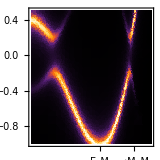

```mathematica
Block[{α=1/3,μ=1,Δ=0.2,δ=0.05,h,G,A},
h[{kx_,ky_}]:=kx^2+ky^2-μ+α(kx^3-3kx ky^2);
G[{ω_,kx_,ky_}]:=(ω+h[{kx,ky}])/(ω^2-h[{kx,ky}]^2-Δ^2);
A[{ω_,kx_,ky_}]:=-2Im[G[{ω+ⅈ δ,kx,ky}]];
DensityPlot[(δ/2)A[{ω,kx,0}],{kx,-2,1.5},{ω,-1,0.5},ColorFunction->"SunsetColors",PlotPoints->15,MaxRecursion->5,PlotRange->All,FrameTicks->{{Automatic,Automatic},{{{0,"\!\(Γ\_M\)"},{-1,"\!\(M\_M←\)",{0,0}},{1,"\!\(→M\_M\)",{0,0}}},Automatic}},FrameLabel->{None,"\!\(ω\)"},ImageSize->160]]
```

STM should see U-shape gap in dI/dV

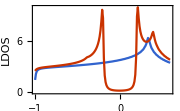

```mathematica
Block[{dat},
dat=FortranGet[FileNameJoin[{NotebookDirectory[],"Fortran","twopocket","data","DOS"}]];
ListLinePlot[{dat⟦All,{1,2}⟧,dat⟦All,{1,3}⟧},FrameLabel->{"\!\(ω\)","LDOS"},PlotRange->All,ImageSize->180]]
```

blue - normal state (Δ=0), red - SC state (Δ=0.2).

#### Valley Resonance

Valley operators in the Majorana basis

I=1/2 χ_-k ᵀ(σ^102,σ^200,σ^302)χ_k

I^(x,y) operator anticommute with the pairing Δ σ^123,

I^z operator commute with the pairing Δ σ^123.

This results in different behaviors of the valley fluctuation spectrum in the SC phase.

Argument: consider the bare susceptibility in the SC phase

χ_0^ab(q)=-Tr G_0(k)I^a G_0(k+q)I^b.

Continuum is gapped by SC → low energy fluctuation (near the lower edge of the continuum) comes from excitations across the SC gap. Near the SC gap edge, Δ≫β_k±α_k, Eq. (DisplayFormulaNumbered) may be simplified to

G(k)=(ⅈ ω σ^000+Δ σ^123)/((ⅈ ω)^2-Δ^2).

Substitute to Eq. (DisplayFormulaNumbered) and carry out the frequency summation

χ_0^ab(q)=-(1-Tr σ^123 I^a σ^123 I^b)Δ/((ⅈ ν)^2-(2Δ)^2)tanh(β Δ)/2.

The coherence factor (1-Tr σ^123 I^a σ^123 I^b):

For I^(x,y) operator,

Tr σ^123 σ^102 σ^123 σ^102=Tr σ^123 σ^200 σ^123 σ^200=-1,

coherence factor remains finite → Im χ_0 will have a hard cutoff at 2Δ → logarithmic divergence of Re χ_0 (according to KK relation) → easy to induce resonance in valley fluctuation.

For I^z operator,

Tr σ^123 σ^302 σ^123 σ^302=+1,

coherence factor vanishes → χ_0 singularity at 2Δ is removed → hard to induce resonance.

Computation Notes

To use efficient real number algebra, we perform a basis rotation to take the complex Hamiltonian

h=β_k σ^002+α_k σ^300+Δ σ^123+I_x σ^102+I_y σ^200+I_z σ^302,

to the real form (apart from I_y which we will only use its Im part)

h=β_k σ^010+α_k σ^300+Δ σ^130+I_x σ^110+I_y σ^200+I_z σ^310.

```mathematica
Column@Normal@AssociationMap[UnitaryTransform[C4[-σ[0,0,3]],Controlled[σ[0,2,1],-σ[0,0,1]],Swap[σ[0,_,_]]],{β σ[0,0,2],α σ[3,0,0],Δ σ[1,2,3],Ix σ[1,0,2],Iy σ[2,0,0],Iz σ[3,0,2]}]
```

β σ[0,0,2]→β σ[0,1,0]
α σ[3,0,0]→α σ[3,0,0]
Δ σ[1,2,3]→Δ σ[1,3,0]
Ix σ[1,0,2]→Ix σ[1,1,0]
Iy σ[2,0,0]→Iy σ[2,0,0]
Iz σ[3,0,2]→Iz σ[3,1,0]

Unitary Transform.

Then we drop the last ineffective bit,

h=β_k σ^01+α_k σ^30+Δ σ^13+I_x σ^11+I_y σ^20+I_z σ^31.

```mathematica
Block[{h,B,A,D,X,Z},
h=B σ[0,1]+A σ[3,0]+D σ[1,3];
CellPrint@Cell[StringJoin["\t\tH("<>ToString[Row[#1,", "]]<>") = "<>ToString[#2]<>"\n"&@@@Most@ArrayRules@Represent@h],"Program"]]
```

H(1, 1) = A
		H(1, 2) = B
		H(1, 3) = D
		H(2, 2) = A
		H(2, 1) = B
		H(2, 4) = -D
		H(3, 3) = -A
		H(3, 4) = B
		H(3, 1) = D
		H(4, 4) = -A
		H(4, 3) = B
		H(4, 2) = -D

Data Processing

equal energy cut

```mathematica
Block[{χ0,qs,ωs,max},
{χ0,qs,ωs}=FortranGet[FileNameJoin[{NotebookDirectory[],"Fortran","resonance","data",#<>"_NS"}]]&/@{"CHI0","QS","WS"};
max=Max@Abs@Flatten@χ0;
ListDensityPlot[MapThread[Append,{qs,Rescale[χ0⟦1,All,#⟧&@14,{-max,max}]}],MeshFunctions->{#3&},ColorFunctionScaling->False,InterpolationOrder->0,PlotRange->All]]
```

```mathematica
Block[{χ0,qs,ωs,max},
{χ0,qs,ωs}=FortranGet[FileNameJoin[{NotebookDirectory[],"Fortran","resonance","data",#<>"_NS"}]]&/@{"CHI0","QS","WS"};
max=Max@Abs@Flatten@χ0;
ListDensityPlot[MapThread[Append,{qs,Rescale[(χ0⟦2,All,#⟧+χ0⟦3,All,#⟧)/2&@14,{-max,max}]}],MeshFunctions->{#3&},ColorFunctionScaling->False,InterpolationOrder->0,PlotRange->All]]
```

momentum line cut along q_x

```mathematica
Block[{χ0,qs,ωs,max,qls,ids},
{χ0,qs,ωs}=FortranGet[FileNameJoin[{NotebookDirectory[],"Fortran","resonance","data",#<>"_NS"}]]&/@{"CHI0","QS","WS"};
max=Max@Abs@Flatten@χ0;
{ids,qls}=Thread@SortBy[Last]@Thread@{#,qs⟦#,1⟧}&@Flatten@Position[qs,{_,0.}];
ListDensityPlot[Transpose@Rescale[χ0⟦1,ids,All⟧,{-max,max}],MeshFunctions->{#3&},ColorFunctionScaling->False,InterpolationOrder->0,PlotRange->All]]
```

```mathematica
Block[{χ0,qs,ωs,max,qls,ids},
{χ0,qs,ωs}=FortranGet[FileNameJoin[{NotebookDirectory[],"Fortran","resonance","data",#<>"_NS"}]]&/@{"CHI0","QS","WS"};
max=Max@Abs@Flatten@χ0;
{ids,qls}=Thread@SortBy[Last]@Thread@{#,qs⟦#,1⟧}&@Flatten@Position[qs,{_,0.}];
ListDensityPlot[Transpose@Rescale[χ0⟦2,ids,All⟧+χ0⟦3,ids,All⟧,{-max,max}],MeshFunctions->{#3&},ColorFunctionScaling->False,InterpolationOrder->0,PlotRange->All]]
```

momentum line cut along q_y

```mathematica
Block[{χ0,qs,ωs,max,qls,ids},
{χ0,qs,ωs}=FortranGet[FileNameJoin[{NotebookDirectory[],"Fortran","resonance","data",#<>"_NS"}]]&/@{"CHI0","QS","WS"};
max=Max@Abs@Flatten@χ0;
{ids,qls}=Thread@SortBy[Last]@Thread@{#,qs⟦#,1⟧}&@Flatten@Position[qs,{0.,_}];
ListDensityPlot[Transpose@Rescale[χ0⟦1,ids,All⟧,{-max,max}],MeshFunctions->{#3&},ColorFunctionScaling->False,InterpolationOrder->0,PlotRange->All]]
```

```mathematica
Block[{χ0,qs,ωs,max,qls,ids},
{χ0,qs,ωs}=FortranGet[FileNameJoin[{NotebookDirectory[],"Fortran","resonance","data",#<>"_NS"}]]&/@{"CHI0","QS","WS"};
max=Max@Abs@Flatten@χ0;
{ids,qls}=Thread@SortBy[Last]@Thread@{#,qs⟦#,1⟧}&@Flatten@Position[qs,{0.,_}];
ListDensityPlot[Transpose@Rescale[χ0⟦2,ids,All⟧+χ0⟦3,ids,All⟧,{-max,max}],MeshFunctions->{#3&},ColorFunctionScaling->False,InterpolationOrder->0,PlotRange->All]]
```

### Breaking SO(4)

#### Anti-Hunds Interaction

The anti-Hunds interaction is an interaction that breaks SO(4) down to SO(3). It is actually a valley ferromagnetic coupling (in the singlet channel)

H_aH=-(I_x^0 I_x^0+I_y^0 I_y^0)=1/2(-Δ^(0†)Δ^0+Δ^(1†)Δ^1+Δ^(2†)Δ^2+Δ^(3†)Δ^3)

```mathematica
Block[{nc,nv,Ss,Ix,Iy,Re0,Rep,Rem,Im0,Imp,Imm,χ,rep,int,H1,H2},
nc={σ[0,0,2]};
nv={σ[3,0,2]};
Ss={σ[0,1,2],σ[0,2,0],σ[0,3,2],σ[3,1,2],σ[3,2,0],σ[3,3,2]};
Ix={σ[1,0,2],σ[2,1,0],σ[2,2,2],σ[2,3,0]};
Iy={-σ[2,0,0],σ[1,1,2],σ[1,2,0],σ[1,3,2]};
Re0={σ[1,2,3],σ[2,3,1],σ[2,0,3],σ[2,1,1]};
Rep={σ[0,2,1]};
Rem={σ[3,2,3]};
Im0={σ[1,2,1],σ[2,3,3],σ[2,0,1],σ[2,1,3]};
Imp={σ[0,2,3]};
Imm={-σ[3,2,1]};
χ=AssociationThread[Range@Length@#->#]&@Cl[8];
rep[a_]:=Total[#2/2 CenterDot@@χ/@#1&@@@Most@ArrayRules@Represent@a];
int[A_,B_,g_]:=g.(#1·#2&@@@Thread@{rep/@A,rep/@B});
H1=-(int[Ix,Ix,{1,0,0,0}]+int[Iy,Iy,{1,0,0,0}]);
H2=int[Re0,Re0,{-1,1,1,1}/2]+int[Im0,Im0,{-1,1,1,1}/2];
Collect[H1-H2,_σ]
]
```

-16 σ[0,0,0,0]

Details.

This actually leads to an attractive interaction in the spin-singlet pairing channel.

We can also consider a direct Heisenberg coupling between valleys

H=S_K·S_K'
=1/8(-3 Δ^(0†)Δ^0+Δ^(1†)Δ^1+Δ^(2†)Δ^2+Δ^(3†)Δ^3)
=1/8(-3 I^(0†)I^0+I^(1†)I^1+I^(2†)I^2+I^(3†)I^3).

```mathematica
Block[{nc,nv,Ss,Ix,Iy,Re0,Rep,Rem,Im0,Imp,Imm,χ,rep,int,H1,H2,H3},
nc={σ[0,0,2]};
nv={σ[3,0,2]};
Ss={σ[0,1,2],σ[0,2,0],σ[0,3,2],σ[3,1,2],σ[3,2,0],σ[3,3,2]};
Ix={σ[1,0,2],σ[2,1,0],σ[2,2,2],σ[2,3,0]};
Iy={-σ[2,0,0],σ[1,1,2],σ[1,2,0],σ[1,3,2]};
Re0={σ[1,2,3],σ[2,3,1],σ[2,0,3],σ[2,1,1]};
Rep={σ[0,2,1]};
Rem={σ[3,2,3]};
Im0={σ[1,2,1],σ[2,3,3],σ[2,0,1],σ[2,1,3]};
Imp={σ[0,2,3]};
Imm={-σ[3,2,1]};
χ=AssociationThread[Range@Length@#->#]&@Cl[8];
rep[a_]:=Total[#2/2 CenterDot@@χ/@#1&@@@Most@ArrayRules@Represent@a];
int[A_,B_,g_]:=g.(#1·#2&@@@Thread@{rep/@A,rep/@B});
H1=int[Ss,Ss,{1,1,1,-1,-1,-1}];
H2=int[Re0,Re0,{a,b,b,b}]+int[Im0,Im0,{a,b,b,b}]/.{a->-3/2,b->1/2};
H3=int[Ix,Ix,{a,b,b,b}]+int[Iy,Iy,{a,b,b,b}]/.{a->-3/2,b->1/2};
Collect[#,_σ]&/@{H1-H2,H1-H3}
]
```

{0,0}

Details.

Consider local interaction

H=S_K·S_K'
=∑_(k,k') ∑_[σ] ∑_i σ_(σ_1 σ_2)^i σ_(σ_3 σ_4)^i c_(K σ_1 k+q)^†c_(K σ_2 k)c_(K' σ_3 k'-q)^†c_(K' σ_4 k')
=∑_(k,k') ∑_[σ] (2 δ_(σ_1 σ_4)δ_(σ_2 σ_3)-δ_(σ_1 σ_2)δ_(σ_3 σ_4))c_(K σ_1 k+q)^†c_(K σ_2 k)c_(K' σ_3 k'-q)^†c_(K' σ_4 k')
=∑_(k,k') ∑_[σ] (2 δ_(σ_1 σ_4)δ_(σ_2 σ_3)-δ_(σ_1 σ_2)δ_(σ_3 σ_4))c_(K' σ_3 k'-q)^†c_(K σ_1 k+q)^†c_(K σ_2 k)c_(K' σ_4 k')
=∑_(k,k') ∑_[σ] (2 c_(K' σ_2 k'-q)^†c_(K σ_1 k+q)^†c_(K σ_2 k)c_(K' σ_1 k')-c_(K' σ_2 k'-q)^†c_(K σ_1 k+q)^†c_(K σ_1 k)c_(K' σ_2 k'))

Pairing channel (k'=-k)

H=∑_k ∑_[σ] (2 c_(K' σ_2-k-q)^†c_(K σ_1 k+q)^†c_(K σ_2 k)c_(K' σ_1 -k)-c_(K' σ_2-k-q)^†c_(K σ_1 k+q)^†c_(K σ_1 k)c_(K' σ_2 -k))
=∑_k ∑_[σ] c_(K' σ_2-k-q)^†c_(K σ_1 k+q)^†(2 c_(K σ_2 k)c_(K' σ_1 -k)-c_(K σ_1 k)c_(K' σ_2 -k))
=∑_k Δ_(k+q)^(σ_1 σ_2†)(2 Δ_k^(σ_2 σ_1)-Δ_k^(σ_1 σ_2)).

In the spin singlet channel, Δ^(σ_2 σ_1)=-Δ^(σ_1 σ_2)=-Δ^0,

H=-3∑_k Δ_(k+q)^(0†)Δ_k^0.

So there is an attraction in the spin-singlet channel, presumably between neighboring momentum. This will enhance the SC, because the neighboring momentum pairing should be of the same sign. The key point is that the fluctuation in the S_K·S_K' channel should peek around Γ instead of other finite momentum.

Valley channel

H=∑_(k,k') ∑_[σ] (-2 c_(K' σ_2 k'-q)^†c_(K σ_2 k)c_(K σ_1 k+q)^†c_(K' σ_1 k')+c_(K' σ_2 k'-q)^†c_(K σ_1 k)c_(K σ_1 k+q)^†c_(K' σ_2 k'))

The first term gives

H≃-2∑_(k,k') I_(k+q-k')^(0†)I_(k+q-k')^0+...

Residual contribution may comes from the second term. But at least we get the sign right.

#### Perturbation Theory

In the Majorana basis

χ=(K
K')⊗(A
B)⊗(↑
↓)⊗(Re
Im).

The band Hamiltonian near K and K' valleys

H_0=1/2 χᵀ(k_x σ^3100+k_y σ^0202)χ.

Green’s function

G_0(k)=(ⅈ ω σ^0000-k_x σ^3100-k_y σ^0202)^-1
=(ⅈ ω σ^0000+k_x σ^3100+k_y σ^0202)/((ⅈ ω)^2-k^2).

Interaction, starting from Hubbard

H_int=U ∑_i n_(i↑)n_(i↓)
=U ∑_([v],a) c_(v_1 a↑)^†c_(v_2 a↑)c_(v_3 a↓)^†c_(v_4 a↓)δ(v_1+v_3=v_2+v_4)
=U/2 ∑_[v,a,σ] c_(v_1 a_1 σ_1)^†c_(v_2 a_2 σ_2)c_(v_3 a_3 σ_3)^†c_(v_4 a_4 σ_4)δ(v_1+v_3=v_2+v_4)δ(a_1=a_2=a_3=a_4)δ(σ_1=σ_2=-σ_3=-σ_4)
=U/8 ∑_[v,a,σ] χ_(v_1 a_1 σ_1 ζ_1)χ_(v_2 a_2 σ_2 ζ_2)χ_(v_3 a_3 σ_3 ζ_3)χ_(v_4 a_4 σ_4 ζ_4)δ(v_1+v_3=v_2+v_4)δ(a_1=a_2=a_3=a_4)δ(σ_1=σ_2=-σ_3=-σ_4) ζ_1^(-1/2)ζ_2^(1/2)ζ_3^(-1/2)ζ_4^(1/2)
=∑_[m] U_(m_1 m_2 m_3 m_4)χ_m_1 χ_m_1 χ_m_2 χ_m_3 χ_m_4.

where

valleys: v_i=+1 for K, v_i=-1 for K',

sublattice: a_i=+1 for A, a_i=-1 for B,

spin: σ_i=+1 for ↑, σ_i=-1 for ↓,

particle-hole: ζ_i=+1 for Re, ζ_i=-1 for Im.

The interaction vertex can be arranged into a rank-4 tensor. Similarly, the inter-valley Heisenberg interaction can also be arrange into a rank-4 tensor

H_int=J ∑_[a] c_Ka^†σ c_Ka·c_(K' a')^†σ c_(K' a')
=∑_[m] J_(m_1 m_2 m_3 m_4)χ_m_1 χ_m_1 χ_m_2 χ_m_3 χ_m_4.

One can verify that the dot product of the U and J tensors are given by

· | U | J
U | 1/2 | -1/2
J | -1/2 | 2

```mathematica
Block[{vert,U,J,dot},
vert[f_]:=SparseArray@ArrayReshape[f@@@Tuples[{1,-1},4],{2,2,2,2}];
{U,J}=SparseArray@Symmetrize[tTr[#,{},Table[{0,4,8,12}+i,{i,4}]]/4,Antisymmetric[All]]&/@{{vert[Boole[#1+#3==#2+#4]&],vert[Boole[#1==#2==#3==#4]&],vert[Boole[#1==#2==-#3==-#4]&]/2,vert[#1^(-1/2)#2^(1/2)#3^(-1/2)#4^(1/2)&]},
{vert[Boole[#1==#2==-#3==-#4]&]/2,vert[Boole[#1==#2&&#3==#4]&],2vert[Boole[#1==#4&&#2==#3]&]-vert[Boole[#1==#2&&#3==#4]&],vert[#1^(-1/2)#2^(1/2)#3^(-1/2)#4^(1/2)&]}};
dot[V1_,V2_]:=tTr[{V1,V2},Table[i+{0,4},{i,4}]];
ArrayReshape[dot@@@Tuples[{U,J},2],{2,2}]
]
```

{{1/2,-1/2},{-1/2,2}}

Details.

This implies that if we start with a positive U (repulsive Hubbard), we will effectively get a negative J (FM, Hunds) interaction. This is the first order effect.

Now we continue to consider the second order effect. We need to first calculate the fermion bubble. We can switch to the real space

G_0=-(ⅈ k_0 σ^0000+k_1 σ^3100+k_2 σ^0202)1/k^2
=(∂_0 σ^0000+ⅈ ∂_1 σ^3100+ⅈ ∂_2 σ^0202)1/(4π r)
=(r_0 σ^0000+ⅈ r_1 σ^3100+ⅈ r_2 σ^0202)-1/(4π r^3).

Therefore the bubble reads

Π=-G_0⊗G_0=-1/(16 π^2 r^6)(r_0 σ^0000+ⅈ r_1 σ^3100+ⅈ r_2 σ^0202)^(⊗2).

We consider averaging over the space-time

∫ⅆ^3 r 1/(16 π^2 r^6)r_μ r_ν=1/(12π a)δ_μν,

where a is the UV cutoff (the microscopic lattice scale).

Π=1/(12π a)(-σ^0000⊗σ^0000+σ^3100⊗σ^3100+σ^0202⊗σ^0202).

```mathematica
Block[{vert,U,J,dot,Π,U2},
vert[f_]:=SparseArray@ArrayReshape[f@@@Tuples[{1,-1},4],{2,2,2,2}];
{U,J}=SparseArray@Symmetrize[tTr[#,{},Table[{0,4,8}+i,{i,4}]]/4,Antisymmetric[All]]&/@{{vert[Boole[#1+#3==#2+#4]&],vert[Boole[#1==#2==-#3==-#4]&]/2,vert[#1^(-1/2)#2^(1/2)#3^(-1/2)#4^(1/2)&]},
{vert[Boole[#1==#2==-#3==-#4]&]/2,2vert[Boole[#1==#4&&#2==#3]&]-vert[Boole[#1==#2&&#3==#4]&],vert[#1^(-1/2)#2^(1/2)#3^(-1/2)#4^(1/2)&]}};
dot[V1_,V2_]:=tTr[{V1,V2},Table[i+{0,4},{i,4}]];
U2=tTr[{U,U},{{3,5},{4,6}}];
dot[U,U2]
]
```

0

```mathematica
Block[{vert,U,J,dot,Π,U2},
vert[f_]:=SparseArray@ArrayReshape[f@@@Tuples[{1,-1},4],{2,2,2,2}];
{U,J}=SparseArray@Symmetrize[tTr[#,{},Table[{0,4,8,12}+i,{i,4}]]/4,Antisymmetric[All]]&/@{{vert[Boole[#1+#3==#2+#4]&],vert[Boole[#1==#2==#3==#4]&],vert[Boole[#1==#2==-#3==-#4]&]/2,vert[#1^(-1/2)#2^(1/2)#3^(-1/2)#4^(1/2)&]},
{vert[Boole[#1==#2==-#3==-#4]&]/2,vert[Boole[#1==#2&&#3==#4]&],2vert[Boole[#1==#4&&#2==#3]&]-0 vert[Boole[#1==#2&&#3==#4]&],vert[#1^(-1/2)#2^(1/2)#3^(-1/2)#4^(1/2)&]}};
dot[V1_,V2_]:=tTr[{V1,V2},Table[i+{0,4},{i,4}]];
Π=Total[(#⊗#&@Represent[#1])#2&@@@{{σ[0,0,0,0],-1},{σ[3,1,0,0],0},{σ[0,2,0,2],0}}];
U2=SparseArray@Symmetrize[tTr[{U,Π,U},{{3,5},{4,7},{6,9},{8,10}}],Antisymmetric[All]];
Simplify@dot[U2,J]
]
```

1/108

```mathematica
Block[{vert,U,J,dot,Π,U2},
vert[f_]:=SparseArray@ArrayReshape[f@@@Tuples[{1,-1},4],{2,2,2,2}];
{U,J}=SparseArray@Symmetrize[tTr[#,{},Table[{0,4,8,12}+i,{i,4}]]/4,Antisymmetric[All]]&/@{{vert[Boole[#1+#3==#2+#4]&],vert[Boole[#1==#2==#3==#4]&],vert[Boole[#1==#2==-#3==-#4]&]/2,vert[#1^(-1/2)#2^(1/2)#3^(-1/2)#4^(1/2)&]},
{vert[Boole[#1==#2==-#3==-#4]&]/2,vert[Boole[#1==#2&&#3==#4]&],2vert[Boole[#1==#4&&#2==#3]&]-vert[Boole[#1==#2&&#3==#4]&],vert[#1^(-1/2)#2^(1/2)#3^(-1/2)#4^(1/2)&]}};
dot[V1_,V2_]:=tTr[{V1,V2},Table[i+{0,4},{i,4}]];
Π=Total[(#⊗#&@Represent[#1])#2&@@@{{σ[0,0,0,0],-1},{σ[3,1,0,0],1},{σ[0,2,0,2],1}}];
U2=SparseArray@Symmetrize[tTr[{U,Π,U},{{3,5},{4,7},{6,9},{8,10}}],Antisymmetric[All]];
dot[U2,J]
]
```

-1/18

We found that the 2nd order effect is still FM... does not leads to anti-Hunds

## Mean Field Theory

### Variational Approach (Failed)

#### Problem Setup

Start from the Fermion c_(v σ k)

v=K,K' labels the valley,

σ=↑,↓ labels the spin,

Or short-handed as c_k=(c_(K↑k),c_(K↓k),c_(K'↑k),c_(K'↓k)), which forms the SU(4) fundamental representation.

Band Hamiltonian

H_0=∑_(k,σ) c_(Kσ k)^†(ξ_k+α_k)c_(Kσ k)+c_(K' σ k)^†(ξ_k-α_k)c_(K' σ k)
=∑_k c_k^†(ξ_k σ^00+α_k σ^30)c_k,
ξ_k=k^2-μ,α_k=α Re k_+^3.

Valley density wave (VDW) order I

H_I=∑_(k,σ) ∑_Q c_(Kσk+Q)^†I_Q c_(K' σk)+h.c
=1/2∑_k ∑_Q c_(k+Q)^†I_Q(σ^10+ⅈ σ^20)c_k+h.c.

Q=Q_(1,2,3) runs over the VDW nesting vectors.

```mathematica
Block[{μ=1,α=1/3,FS},
FS=Block[{kF,t0,t1},
kF=FSOrbit[α,μ];
{{t0,t1}}=kF@"Domain";
Cases[ParametricPlot[kF[t0+λ(t1-t0)],{λ,0,1}],_Line,∞]];
Graphics[{{Red,FS,Text["\!\(K\)",{1.05,0}],Blue,Scale[FS,{-1,1},{0,0}],Text["\!\(K\^′\)",{-1.05,0}]},{Arrowheads[{0.08}],{Arrow[{-#1,#1}],Text["\!\(Q\_"<>#2<>"\)",0.75#1,1.25{{0,1},{-1,0}}.#1]}&@@@Thread@{CirclePoints[{Sqrt[3μ]/2,0},3],{"1","2","3"}}}},ImageSize->120]]
```

-Graphics-

I_Q=(I/2)(1+Re (Q_+/|Q|)^3) selects the forward scattering channel only.

Only the spin-singlet VDW is considered here (among the other degenerated O(4) vector components).

Topological superconductivity (TSC) order (Δ_p,Δ_d)

H_Δ=∑_(k,σ,σ') c_Kσk(Δ_dk-Δ_pk)ϵ_(σ σ')c_(K' σ'-k)+h.c
=1/2∑_k c_k ᵀ(Δ_pk σ^22+ⅈ Δ_dk σ^12)c_-k+h.c,
Δ_pk=Δ_p k_+,Δ_dk=Δ_d k_-^2.

Here we consider the spin singlet pairing (among the other degenerated O(4) vector components), with ϵ=ⅈ σ^2 being the antisymmetric tensor in the spin space. Spell out explicitly

c_Kσk(Δ_dk-Δ_pk)ϵ_(σ σ')c_(K' σ'-k)=(Δ_dk-Δ_pk)(c_(K↑k)c_(K'↓-k)-c_(K↓k)c_(K'↑-k)).

If we introduce the pairing operator (in terms of Fermion bilinear)

(Δ̂)_k^(σ σ')=c_Kσk c_(K' σ'-k),

the TSC Hamiltonian can be written as

H_Δ=∑_k (Δ_dk-Δ_pk)((Δ̂)_k^(↑↓)-(Δ̂)_k^(↓↑))+h.c

#### Variational Approach

Consider the mean-field Hamiltonian

H_MF=H_0+H_I+H_Δ,

its thermal density matrix ρ_MF=Z_MF^-1 e^(-β H_MF) is treated as a variational state,

parameterized by the order parameters: I,Δ_p,Δ_d.

The mean-field solution is given by minimizing the variational energy

F_MF=Tr ρ_MF H,

which is evaluated with respect to the physical Hamiltonian H

H=H_0+H_int,
H_int=-U_RPA/2∑_Q (Î)_Q^(μ†)(Î)_Q^μ.

(Î)_Q^μ is the VDW operator (in terms of Fermion bilinear).

(Î)_Q^μ=∑_(k,σ,σ') (c_(Kσk+Q)^†(σ^0,ⅈ σ^1,ⅈ σ^2,ⅈ σ^3))_(σ σ')c_(K' σ' k).

Using the Fierz identity

(Î)_Q^(μ†)(Î)_Q^μ=∑_(k,k') ∑_[σ] ∑_μ σ_(σ_1 σ_2)^μ σ_(σ_3 σ_4)^μ c_(K' σ_1 k-Q)^†c_(K σ_2 k)c_(K σ_3 k'+Q)^†c_(K' σ_4 k')
=∑_(k,k') ∑_[σ] 2 δ_(σ_1 σ_4)δ_(σ_2 σ_3)c_(K' σ_1 k-Q)^†c_(K σ_2 k)c_(K σ_3 k'+Q)^†c_(K' σ_4 k')
=∑_(k,k') ∑_(σ,σ') 2 c_(K' σ' k-Q)^†c_(Kσ k)c_(Kσ k'+Q)^†c_(K' σ' k'),

therefore the interaction reads

H_int=-U_RPA∑_Q ∑_(k,k') ∑_(σ,σ') c_(K' σ' k-Q)^†c_(Kσ k)c_(Kσ k'+Q)^†c_(K' σ' k').

It is crucial to use the SO(4) symmetric interaction, if we break the symmetry to SO(3) strongly, (e.g. by keeping the I_Q^0 channel only), the most favorable pairing will change completely (to s-wave spin-singlet).

#### Mean Field Expectations

The mean-field expectation value of H_0 is straight forward to evaluate, we will elaborate on the expectation value of H_int.

In the VDW channel (corresponding to (Î)_Q^0), according to Eq. (DisplayFormulaNumbered),

⟨H_int⟩=-U_RPA/2∑_Q (|⟨(Î)_Q⟩|)^2,
⟨(Î)_Q⟩=∑_(k,σ) ⟨c_(Kσk+Q)^†c_(K' σ k)⟩=∂_I_Q ⟨H_I⟩.

Note that here we treat I_Q as a complex variable such that ∂_I_Q  does not act on the h.c. term in H_I.

In the TSC channel, according to Eq. (DisplayFormulaNumbered), (first switch to the pairing channel)

H_int=-U_RPA∑_Q ∑_(k,k') ∑_(σ,σ') c_(K' σ' k-Q)^†c_(Kσ k)c_(Kσ k'+Q)^†c_(K' σ' k')
=U_RPA∑_Q ∑_(k,k') ∑_(σ,σ') c_(K' σ' k-Q)^†c_(Kσ k'+Q)^†c_(Kσ k)c_(K' σ' k')
=^(k'→-k)U_RPA∑_(Q,k) ∑_(σ,σ') c_(K' σ' k-Q)^†c_(Kσ-k+Q)^†c_(Kσ k)c_(K' σ' -k)
=U_RPA∑_(Q,k) ∑_(σ,σ') (Δ̂)_(-k+Q)^(σσ'†)(Δ̂)_k^(σ σ'),

where (Δ̂)_k^(σ σ') was defined in Eq. (DisplayFormulaNumbered). All the O(4) vector pairings are degenerated. Since in Eq. (DisplayFormulaNumbered), we choose to focus on the spin-singlet pairing only, can further restrict the interaction to

H_int=^(σ'→-σ)U_RPA∑_(Q,k) ((Δ̂)_(-k+Q)^(↑↓†)(Δ̂)_k^(↑↓)+(Δ̂)_(-k+Q)^(↓↑†)(Δ̂)_k^(↓↑)).

From Eq. (DisplayFormulaNumbered) define

⟨(Δ̂)_k⟩=⟨c_(K↑k)c_(K'↓-k)-c_(K↓k)c_(K'↑-k)⟩
=⟨(Δ̂)_k^(↑↓)-(Δ̂)_k^(↓↑)⟩
=∂_(Δ_dk-Δ_pk) ⟨H_Δ⟩,

we have ⟨(Δ̂)_k^(↑↓)⟩=-⟨(Δ̂)_k^(↓↑)⟩=1/2⟨(Δ̂)_k⟩. Therefore

⟨H_int⟩=U_RPA/2∑_(Q,k) ⟨(Δ̂)_(-k+Q)⟩^*⟨(Δ̂)_k⟩,

implying that ⟨(Δ̂)_k⟩=-⟨(Δ̂)_(-k+Q)⟩ must change sign on the Fermi surface to gain the interaction energy.

In conclusion, the variational energy is

F_MF=⟨H_0⟩-U_RPA/2∑_Q ((|⟨(Î)_Q⟩|)^2-∑_k ⟨(Δ̂)_(-k+Q)⟩^*⟨(Δ̂)_k⟩),
⟨(Î)_Q⟩=∂_I_Q ⟨H_MF⟩,⟨(Δ̂)_k⟩=∂_(Δ_dk-Δ_pk) ⟨H_MF⟩.

#### Compact Basis

Introduce the Fermion in a more compact basis

ψ_Kk=(c_(K↑k)
c_(K'↓-k)^†),ψ_(K' k)=(c_(K'↑k)
c_(K↓-k)^†).

The mean-field Hamiltonian can be written as

H_MF=∑_k (ψ_Kk^†𝒽_k ψ_Kk+ψ_(K' k)^†𝒽_-k ψ_(K' k))+∑_(k,Q) (ψ_(Kk+Q)^†ℐ_Q ψ_(K' k)+h.c.),
𝒽_k=(ξ_k+α_k | Δ_pk^*-Δ_dk^*
Δ_pk-Δ_dk | -ξ_k-α_k), ℐ_Q=(I_Q | 0
0 | -I_Q),
ξ_k=k^2-μ,α_k=α Re k_+^3,
Δ_pk=Δ_p k_+,Δ_dk=Δ_d k_-^2,
I_Q=(I/2)(1+Re (Q_+/|Q|)^3).

Reflection M_y (k_+→k_+^*) (acts as anti-unitary)

M_y:(ψ_Kk
ψ_(K' k))→𝒦(ψ_(KM_y(k))
ψ_(K' M_y(k))).

Consequently,

M_y:⟨(Î)_Q⟩→⟨(Î)_(M_y(Q))⟩, ⟨(Δ̂)_k⟩→⟨(Δ̂)_(M_y(k))⟩^*.

Rotation C_3 (k_+→e^(ⅈ 2π/3)k_+)

C_3:(ψ_Kk
ψ_(K' k))→e^(ⅈ π/3 σ^3)(ψ_(KC_3(k))
ψ_(K' C_3(k))).

Consequently,

C_3:⟨(Î)_Q⟩→⟨(Î)_(C_3(Q))⟩, ⟨(Δ̂)_k⟩→e^(ⅈ 2π/3)⟨(Δ̂)_(C_3(k))⟩.

Here we assume the pairing to be p+ⅈ p mixed with d-ⅈ d. If the time-reversal partner pairing is taken, the C_3 symmetry representation must also be conjugated.

In conclusion, the symmetry enforces that

⟨(Î)_Q⟩=⟨(Î)_(C_3(Q))⟩=⟨(Î)_(M_y(Q))⟩,
⟨(Δ̂)_k⟩=⟨(Δ̂)_(M_y(k))⟩^*=e^(ⅈ 2π/3)⟨(Δ̂)_(C_3(k))⟩.

#### Folded Brillouin Zone

The nesting vector Q_(1,2,3) defines a folded Brillouin zone.

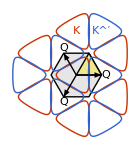

```mathematica
Block[{μ=1,α=1/3,Q=1.7,Qs,FS,Qind},
Qs=Block[{R=1},Association@Table[(-1)^d->Cases[Flatten[Table[Q({3(l1-l2),Sqrt[3](l1+l2)}/2+{d,0}),{l1,-R,R},{l2,-R,R}],1],q_/;Norm[q]≤Q(3R+1.0001)/2],{d,{0,1}}]];
FS=Block[{kF,t0,t1},
kF=FSOrbit[α,μ];
{{t0,t1}}=kF@"Domain";
Cases[ParametricPlot[kF[t0+λ(t1-t0)],{λ,0,1}],_Line,∞]];
Qind=AssociationThread[#->Range@Length@#]&[Join@@(Qs/@{1,-1})];
Graphics[{{GrayLevel[0.9],EdgeForm[Directive[Black,AbsoluteThickness[1]]],Polygon[CirclePoints[{Q,0},6]]},{LightYellow,EdgeForm[Directive[Black,Dashed,AbsoluteThickness[1]]],Polygon[Q{{0,0},{1,0},{1,Sqrt[3]}/2}]},Table[Translate[{Switch[ϛ,1,Red,-1,Blue],Scale[FS,{ϛ,1},{0,0}]},#]&/@Qs[ϛ],{ϛ,Keys@Qs}],{Red,Text["\!\(K\)",Qs[1]⟦-1⟧],Blue,Text["\!\(K\^′\)",Qs[-1]⟦-1⟧]},
{Arrowheads[{0.07}],{Arrow[{{0,0},#1}],Text["\!\(Q\_"<>#2<>"\)",#1,-0.5#1]}&@@@Thread@{CirclePoints[{Q,0},3],{"1","2","3"}}}},ImageSize->140]]
```

Using the M_y and C_3 symmetries, we will only need to perform the calculation within the yellow triangle inside the folded BZ.

```mathematica
Block[{L=12,Q=1,k2w},
k2w=Association@Flatten@Table[{l1+l2/2,l2 Sqrt[3]/2}/L->If[l1==0,If[l2==0||l2==L,1/6,1/2],If[l2==0,If[l1==L,1/6,1/2],If[l1+l2==L,1/2,1]]],{l1,0,L},{l2,0,L-l1}];
Graphics[{{LightYellow,EdgeForm[Directive[Black,AbsoluteThickness[1]]],Polygon[Q{{0,0},{1,0},{1,Sqrt[3]}/2}]},{GrayLevel[1-k2w[#]],Point[#]}&/@Keys@k2w},ImageSize->90]]
```

-Graphics-

#### Two-Pocket Setup

Take two-pocket, the mean-field Hamiltonian

|  | ψ_Kk |  | ψ_(K' k-Q) | 
 |  | c_(K↑k) | c_(K'↓-k)^† | c_(K'↑k-Q) | c_(K↓-k+Q)^†
ψ_Kk^† | c_(K↑k)^† | ξ_k+α_k | Δ_pk^*-Δ_dk^* | I_Q | 0
 | c_(K'↓-k) | Δ_pk-Δ_dk | -ξ_k-α_k | 0 | -I_Q
ψ_(K' k-Q)^† | c_(K'↑k-Q)^† | I_Q^* | 0 | ξ_(-k+Q)+α_(-k+Q) | Δ_(p-k+Q)^*-Δ_(d-k+Q)^*
 | c_(K↓-k+Q) | 0 | -I_Q^* | Δ_(p-k+Q)-Δ_(d-k+Q) | -ξ_(-k+Q)-α_(-k+Q).

So the order parameter operators are

(Î)_Q=∑_σ c_(Kσk+Q)^†c_(K' σ k)=(0 | 0 | 1 | 0
0 | 0 | 0 | -1
0 | 0 | 0 | 0
0 | 0 | 0 | 0),
(Δ̂)_k=2 c_(K↑k)c_(K'↓-k)=(0 | 0 | 0 | 0
-2 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),
(Δ̂)_(-k+Q)=-2 c_(K↓-k+Q)c_(K'↑k-Q)=(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | -2 | 0).

Test board

```mathematica
Block[{T=0.01,μ=1,α=1/3,Q=1.7,URPA=0.,h0,hMF,ops,k2w,fs,plot,F},
h0[{kx_,ky_}]:=kx^2+ky^2-μ+α (kx^3-3kx ky^2);
hMF[IQ_,Δp_,Δd_][k_]:=Block[{h},
h[{kx_,ky_}]:=If[Norm[{kx,ky}]≤2/(3α),
{{h0[{kx,ky}],Δp(kx-ⅈ ky)-Δd(kx+ⅈ ky)^2},{Δp(kx+ⅈ ky)-Δd(kx-ⅈ ky)^2,-h0[{kx,ky}]}},2PauliMatrix[3]];
ArrayFlatten[N@{{h[k],IQ PauliMatrix[3]},{IQ PauliMatrix[3],h[-k+{Q,0}]}}]];
ops=SparseArray[#,{4,4}]&/@{{{1,3}->1,{2,4}->-1},{{2,1}->-2},{{4,3}->-2}};
k2w=Block[{L=12},Association@Flatten@Table[Q{l1+l2/2,l2 Sqrt[3]/2}/L->If[l1==0,If[l2==0||l2==L,1/6,1/2],If[l2==0,If[l1==L,1/6,1/2],If[l1+l2==L,1/2,1]]],{l1,0,L},{l2,0,L-l1}]];
fs=Block[{kF,t0,t1},
kF=FSOrbit[α,μ];
{{t0,t1}}=kF@"Domain";
Cases[ParametricPlot[kF[t0+λ(t1-t0)],{λ,0,1}],_Line,∞]];
plot[dat_]:=Graphics[{MapThread[{#1,Point[#2]}&,{ComplexColor/@dat,Keys@k2w}],
{AbsoluteThickness[1],Red,fs,Blue,Translate[Scale[fs,{-1,1},{0,0}],{Q,0}]}},PlotRange->{{0,Q},{0,Q Sqrt[3]/2}},PlotRangePadding->Scaled[.05],ImageSize->70];
F[IQ_,Δp_,Δd_]:=Block[{evals,sum},
evals=Table[Block[{eigs},
eigs=Thread@Eigensystem@hMF[IQ,Δp,Δd][k];
Total[k2w[k](1-Tanh[#1/(2T)])/2Prepend[
Table[Conjugate[#2].op.#2,{op,ops}],
Conjugate[#2].({h0[k],-h0[k],h0[-k+{Q,0}],-h0[-k+{Q,0}]}#2)]&@@@eigs]],{k,Keys@k2w}];
sum=Total@Chop[#1-URPA/2(#2^2-Re[#3 Conjugate[#4]])&@@@evals];
{sum,plot/@Thread[{#1,#2,#3,#4,#2^2,Re[#3 Conjugate[#4]]}&@@@evals]}
(*sum*)];
Labeled[Grid[{{"\!\(⟨H\_0⟩\)","\!\(⟨I\_Q⟩\)","\!\(⟨Δ\_k⟩\)","\!\(⟨Δ\_\(-k+Q\)⟩\)","\!\(⟨I\_Q⟩\^2\)","\!\(Re⟨Δ\_\(-k+Q\)⟩\^*⟨Δ\_k⟩\)"},#2}],"\!\(F\_MF="<>ToString[#1]<>"\)"]&@@F[0.2,0.1,0.2]]
```

⟨H_0⟩ | ⟨I_Q⟩ | ⟨Δ_k⟩ | ⟨Δ_-k+Q⟩ | ⟨I_Q⟩^2 | Re⟨Δ_-k+Q⟩^*⟨Δ_k⟩
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-F_MF=-86.5839

A test run shows that this variational approach does not capture the temperature dependent behavior correctly.

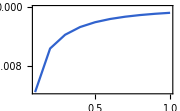

```mathematica
ListLinePlot[Table[Block[{μ=0.6,α=1/3,Q=1.3,URPA=0.4,h0,hMF,ops,k2w,fs,plot,F},
h0[{kx_,ky_}]:=kx^2+ky^2-μ+α (kx^3-3kx ky^2);
hMF[IQ_,Δp_,Δd_][k_]:=Block[{h},
h[{kx_,ky_}]:=If[Norm[{kx,ky}]≤2/(3α),
{{h0[{kx,ky}],Δp(kx-ⅈ ky)-Δd(kx+ⅈ ky)^2},{Δp(kx+ⅈ ky)-Δd(kx-ⅈ ky)^2,-h0[{kx,ky}]}},2PauliMatrix[3]];
ArrayFlatten[N@{{h[k],IQ PauliMatrix[3]},{IQ PauliMatrix[3],h[-k+{Q,0}]}}]];
ops=SparseArray[#,{4,4}]&/@{{{1,3}->1,{2,4}->-1},{{2,1}->-2},{{4,3}->-2}};
k2w=Block[{L=18},Association@Flatten@Table[Q{l1+l2/2,l2 Sqrt[3]/2}/L->If[l1==0,If[l2==0||l2==L,1/6,1/2],If[l2==0,If[l1==L,1/6,1/2],If[l1+l2==L,1/2,1]]],{l1,0,L},{l2,0,L-l1}]];
F[IQ_,Δp_,Δd_]:=Block[{evals,sum},
evals=Table[Block[{eigs},
eigs=Thread@Eigensystem@hMF[IQ,Δp,Δd][k];
Total[k2w[k](1-Tanh[#1/(2T)])/2Prepend[
Table[Conjugate[#2].op.#2,{op,ops}],
Conjugate[#2].({h0[k],-h0[k],h0[-k+{Q,0}],-h0[-k+{Q,0}]}#2)]&@@@eigs]],{k,Keys@k2w}];
Total@Chop[#1-URPA/2(#2^2-Re[#3 Conjugate[#4]])&@@@evals]];
{T,#2-#1}&@@(F[0.,#1,1.5#1]&/@{0.,0.01})],{T,0.1,1,0.1}],FrameLabel->{"\!\(T\)","\!\(δF\_MF\)"},PlotRange->All,ImageSize->180]
```

### Field Theory Approach

#### RPA Interaction

Define the following Fermion bilinear operators

VDW operator

(Î)_Q^μ=∑_(k,σ,σ') (c_(Kσk+Q)^†(σ^0,ⅈ σ^1,ⅈ σ^2,ⅈ σ^3))_(σ σ')c_(K' σ' k).

TSC operator

(Δ̂)_k^μ=∑_(σ,σ') (c_Kσk(ⅈ σ^2,ⅈ σ^3,- σ^0,-ⅈ σ^1))_(σ σ')c_(K' σ'-k).

```mathematica
ⅈ σ[2]·#&/@{σ[0],ⅈ σ[1],ⅈ σ[2],ⅈ σ[3]}
```

{ⅈ σ[2],ⅈ σ[3],-σ[0],-ⅈ σ[1]}

Pauli product.

The interaction can be written two ways

H_int=-g/2∑_Q (Î)_Q^(μ†)(Î)_Q^μ=g/2∑_(Q,k) (Δ̂)_(-k+Q)^(μ†)(Δ̂)_k^μ.

VDW channel

H_int=-g/2∑_(k,k') ∑_[σ] ∑_μ σ_(σ_1 σ_2)^μ σ_(σ_3 σ_4)^μ c_(K' σ_1 k-Q)^†c_(K σ_2 k)c_(K σ_3 k'+Q)^†c_(K' σ_4 k')
=-g∑_Q ∑_(k,k') ∑_(σ,σ') c_(K' σ' k-Q)^†c_(Kσ k)c_(Kσ k'+Q)^†c_(K' σ' k').

TSC channel

H_int=g/2∑_(Q,k) ∑_[σ] ∑_μ σ_(σ_1 σ_2)^μ σ_(σ_3 σ_4)^μ c_(K' σ_1 k-Q)^†c_(K σ_2-k+Q)^†c_(K σ_3 k)c_(K' σ_4 -k)
=g∑_(Q,k) ∑_(σ,σ') c_(K' σ' k-Q)^†c_(Kσ-k+Q)^†c_(Kσ k)c_(K' σ' -k).

Eq. (DisplayFormulaNumbered) is reduced from Eq. (DisplayFormulaNumbered) by restricting the momentum k' to -k.

#### Mean Field Decomposition

Introduce the mean field in the spin-singlet channel (μ=0),

VDW channel

H=H_0+∑_Q (I_Q^*(Î)_Q^0+h.c.)+1/(2g)∑_Q I_Q^*I_Q,
=H_0+∑_(Q,k) (I_Q^*(c_(K↑k+Q)^†c_(K'↑ k)+c_(K↓k+Q)^†c_(K'↓ k))+h.c.)+1/(2g)∑_Q I_Q^*I_Q.

TSC channel

H=H_0+∑_(Q,k) (Δ_k^*(Δ̂)_k^0+h.c.)-1/(2g)∑_(Q,k) Δ_(-k+Q)^*Δ_k,
=H_0+∑_(Q,k) (Δ_k^*(c_(K↑k)c_(K'↓-k)-c_(K↓k)c_(K'↑-k))+h.c.)-1/(2g)∑_(Q,k) Δ_(-k+Q)^*Δ_k.

Combining Eq. (DisplayFormulaNumbered) and Eq. (DisplayFormulaNumbered),

H=H_0+H_I+H_Δ+H_bg,
H_0=∑_(k,σ) c_(Kσ k)^†(ξ_k+α_k)c_(Kσ k)+c_(K' σ k)^†(ξ_k-α_k)c_(K' σ k),
H_I=∑_(Q,k) I_Q^*(c_(K↑k+Q)^†c_(K'↑ k)+c_(K↓k+Q)^†c_(K'↓ k))+h.c.,
H_Δ=∑_(Q,k) Δ_k^*(c_(K↑k)c_(K'↓-k)-c_(K↓k)c_(K'↑-k))+h.c.,
H_bg=1/g∑_Q (I_Q^*I_Q-c∑_k Δ_(-k+Q)^*Δ_k).

Here we introduce a phenomenological parameter c to tune the relative instability of TSC v.s. VDW. Because the TSC channel is restricted from the full interaction, its effective coupling should be weaker, so c (as an inverse coupling) is expected to be large.

#### Compact Basis

Introduce the Fermion in a more compact basis

ψ_Kk=(c_(K↑k)
c_(K'↓-k)^†),ψ_(K' k)=(c_(K'↑k)
c_(K↓-k)^†).

The mean-field Hamiltonian H_MF=H_0+H_I+H_Δ can be written as

H_MF=∑_k (ψ_Kk^†𝒽_k ψ_Kk+ψ_(K' k)^†𝒽_-k ψ_(K' k))+∑_(k,Q) (ψ_(Kk+Q)^†ℐ_Q^†ψ_(K' k)+h.c.),
𝒽_k=(ϵ_k | -Δ_k
-Δ_k^* | -ϵ_k), ℐ_Q^†=(I_Q^* | 0
0 | -I_Q^*),
ϵ_k=k^2-μ+α Re k_+^3,
I_Q=I,Δ_k=Δ_p k_+-Δ_d k_-^2.

In matrix form,

|  | ψ_Kk |  | ψ_(K' k-Q) | 
 |  | c_(K↑k) | c_(K'↓-k)^† | c_(K'↑k-Q) | c_(K↓-k+Q)^†
ψ_Kk^† | c_(K↑k)^† | ϵ_k | -Δ_k | I_Q^* | 0
 | c_(K'↓-k) | -Δ_k^* | -ϵ_k | 0 | -I_Q^*
ψ_(K' k-Q)^† | c_(K'↑k-Q)^† | I_Q | 0 | ϵ_(-k+Q) | -Δ_(-k+Q)
 | c_(K↓-k+Q) | 0 | -I_Q | -Δ_(-k+Q)^* | -ϵ_(-k+Q).

Now we integrate out the fermions at finite temperature to obtain the free energy

F=-β^-1∑_(k,n) ln(1+e^(-β E_nk))+H_bg.

E_nk denotes the single-particle energy levels of H_MF.

The free energy will be a function of the order parameters I,Δ_p,Δ_d.

The background potential H_bg is given in Eq. (DisplayFormulaNumbered).

#### Parameter Tuning

##### Nesting Momentum Q

Q=1.5

```mathematica
Row[#,Alignment->Bottom]&@Table[ListLinePlot[Thread@Table[Block[{α=1/3,Q=1.5,g=0.8,c=2.5,ks,ws,f,F},
Block[{L=12},{ks,ws}=Thread@Flatten[Table[{Q{l1+l2/2,l2 Sqrt[3]/2}/L,If[l1==0,If[l2==0||l2==L,1/6,1/2],If[l2==0,If[l1==L,1/6,1/2],If[l1+l2==L,1/2,1]]]},{l1,0,L},{l2,0,L-l1}],1];
ws=ws/Total[ws]];
f=Compile[{{x,_Real}},If[Abs[x]<10.,Log[(1+Tanh[x/2])/2],(x-Abs[x])/2]];
F[IQ_,Δp_,Δd_]:=Block[{hcut=2,h0,Δ,h,hMF},
h0[{kx_,ky_}]:=kx^2+ky^2-μ+α (kx^3-3kx ky^2);
Δ[{kx_,ky_}]:=Δp(kx+ⅈ ky)-Δd(kx-ⅈ ky)^2;
h[k:{_,_}]:=If[Norm[k]≤2/(3α),
{{h0[k],Δ[k]},{Conjugate[Δ[k]],-h0[k]}},hcut PauliMatrix[3]];
hMF[k_]:=
ArrayFlatten[N@{{h[k],IQ PauliMatrix[3]},{IQ PauliMatrix[3],h[-k+{Q,0}]}}];
T ws.Table[Total[f/@(Eigenvalues@hMF[k]/T)],{k,ks}]+1/g(IQ^2-c Re[ws.Table[Conjugate[Δ[-k+{Q,0}]]Δ[k],{k,ks}]])];
Block[{dx=0.1,Fs},
Fs={F[0,0,0],F[dx,0,0],F[0,0.5dx,0.5dx]};
{μ,(First@Fs-#)/dx^2}&/@Rest@Fs]],{μ,0.,2.,0.1}],FrameLabel->{"\!\(μ\)",None},PlotLabel->"\!\(T="<>ToString[T]<>"\)",AspectRatio->1,ImageSize->120],{T,{0.3,0.1,0.02}}]
```

-Graphics--Graphics--Graphics-

Q=1.7

```mathematica
Row[#,Alignment->Bottom]&@Table[ListLinePlot[Thread@Table[Block[{α=1/3,Q=1.7,g=0.8,c=2.5,ks,ws,f,F},
Block[{L=12},{ks,ws}=Thread@Flatten[Table[{Q{l1+l2/2,l2 Sqrt[3]/2}/L,If[l1==0,If[l2==0||l2==L,1/6,1/2],If[l2==0,If[l1==L,1/6,1/2],If[l1+l2==L,1/2,1]]]},{l1,0,L},{l2,0,L-l1}],1];
ws=ws/Total[ws]];
f=Compile[{{x,_Real}},If[Abs[x]<10.,Log[(1+Tanh[x/2])/2],(x-Abs[x])/2]];
F[IQ_,Δp_,Δd_]:=Block[{hcut=2,h0,Δ,h,hMF},
h0[{kx_,ky_}]:=kx^2+ky^2-μ+α (kx^3-3kx ky^2);
Δ[{kx_,ky_}]:=Δp(kx+ⅈ ky)-Δd(kx-ⅈ ky)^2;
h[k:{_,_}]:=If[Norm[k]≤2/(3α),
{{h0[k],Δ[k]},{Conjugate[Δ[k]],-h0[k]}},hcut PauliMatrix[3]];
hMF[k_]:=
ArrayFlatten[N@{{h[k],IQ PauliMatrix[3]},{IQ PauliMatrix[3],h[-k+{Q,0}]}}];
T ws.Table[Total[f/@(Eigenvalues@hMF[k]/T)],{k,ks}]+1/g(IQ^2-c Re[ws.Table[Conjugate[Δ[-k+{Q,0}]]Δ[k],{k,ks}]])];
Block[{dx=0.1,Fs},
Fs={F[0,0,0],F[dx,0,0],F[0,0.5dx,0.5dx]};
{μ,(First@Fs-#)/dx^2}&/@Rest@Fs]],{μ,0.,2.,0.1}],FrameLabel->{"\!\(μ\)",None},PlotLabel->"\!\(T="<>ToString[T]<>"\)",AspectRatio->1,ImageSize->120],{T,{0.3,0.1,0.02}}]
```

-Graphics--Graphics--Graphics-

#### Free Energy Landscape

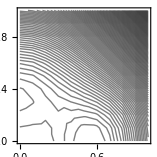

```mathematica
Block[{μ=0.75,T=0.05},
Block[{α=1/3,Q=1.7,g=0.8,c=2.,ks,ws,f,F},
Block[{L=12},{ks,ws}=Thread@Flatten[Table[{Q{l1+l2/2,l2 Sqrt[3]/2}/L,If[l1==0,If[l2==0||l2==L,1/6,1/2],If[l2==0,If[l1==L,1/6,1/2],If[l1+l2==L,1/2,1]]]},{l1,0,L},{l2,0,L-l1}],1];
ws=ws/Total[ws]];
f=Compile[{{x,_Real}},If[Abs[x]<10.,Log[(1+Tanh[x/2])/2],(x-Abs[x])/2]];
F[IQ_,Δp_,Δd_]:=Block[{hcut=2,h0,Δ,h,hMF},
h0[{kx_,ky_}]:=kx^2+ky^2-μ+α (kx^3-3kx ky^2);
Δ[{kx_,ky_}]:=Δp(kx+ⅈ ky)-Δd(kx-ⅈ ky)^2;
h[k:{_,_}]:=If[Norm[k]≤2/(3α),
{{h0[k],Δ[k]},{Conjugate[Δ[k]],-h0[k]}},hcut PauliMatrix[3]];
hMF[k_]:=
ArrayFlatten[N@{{h[k],IQ PauliMatrix[3]},{IQ PauliMatrix[3],h[-k+{Q,0}]}}];
T ws.Table[Total[f/@(Eigenvalues@hMF[k]/T)],{k,ks}]+1/g(IQ^2-c Re[ws.Table[Conjugate[Δ[-k+{Q,0}]]Δ[k],{k,ks}]])];
ListContourPlot[Flatten[Table[{x,y,F[x,0.2y,0.5y]},{x,0,1,0.1},{y,0,1,0.1}],1],Contours->100,ContourStyle->Thin,ContourShading->None]
]]
```

The current treatment of background potential in the pairing channel is not bounded, leading to instability in the free energy landscape.

H_bg≃-(π Λ^4)/6(3 Δ_p^2-2 Δ_d^2 Λ^2).

```mathematica
Block[{Δ},
Δ[{kx_,ky_}]:=Δp(kx+ⅈ ky)-Δd(kx-ⅈ ky)^2;
Factor@Integrate[Δ[{-kx+Q,ky}]Δ[{kx,ky}],{kx,ky}∈Disk[{0,0},Λ],Assumptions->Λ>0]]
```

-1/6 π Λ^4 (3 Δp^2-2 Δd^2 Λ^2)

Integral.

Δ_p can go all the way large without control. Unless we artificially pins a ratio between Δ_p and Δ_d.

#### Self-Consistent Mean-Field

We have to solve the self-consistency equation. We still start with Eq. (DisplayFormulaNumbered), but then we evaluate the mean-field expectation self-consistently

I_Q=-g∑_k ⟨ψ_(Kk+Q)^†(1 | 0
0 | -1)ψ_(K' k)⟩,
Δ_(-k+Q)=g'⟨ψ_Kk^†(0 | 0
-2 | 0)ψ_Kk⟩.

g' is adjusted from g to account for the scattering channels that has been dropped.

We first construct a momentum grid and define the reflection operator to map between K and K' valleys.

```mathematica
Block[{T=0.0001,μ=1,α=1/3,Q=1.7,g=0.5,ks,ws,R,ϵs},
Block[{L=12},{ks,ws}=Thread@Flatten[Table[{N[Q{l1+l2/2,l2 Sqrt[3]/2}/L],If[l1==0,If[l2==0||l2==L,1/6,1/2],If[l2==0,If[l1==L,1/6,1/2],If[l1+l2==L,1/2,1]]]},{l1,0,L},{l2,0,L-l1}],1];
ws=ws/Total[ws];
R=SparseArray@Table[Boole[Norm[k1-{-k2⟦1⟧+Q,k2⟦2⟧}]<0.1Q/L],{k1,ks},{k2,ks}]];
ϵs=Function[{kx,ky},kx^2+ky^2-μ+α (kx^3-3kx ky^2)]@@@ks;
Row[ListContourPlot[MapThread[Append,{ks,#}],Contours->20,ContourStyle->AbsoluteThickness[1],Frame->None,ImageSize->72]&/@
{ϵs,R.ϵs}]
]
```

-Graphics--Graphics-

```mathematica
Block[{T=0.0001,μ=1,α=1/3,Q=1.7,g=0.5,ks,ws,R,ϵs,Δ0s},
Block[{L=12},{ks,ws}=Thread@Flatten[Table[{N[Q{l1+l2/2,l2 Sqrt[3]/2}/L],If[l1==0,If[l2==0||l2==L,1/6,1/2],If[l2==0,If[l1==L,1/6,1/2],If[l1+l2==L,1/2,1]]]},{l1,0,L},{l2,0,L-l1}],1];
ws=ws/Total[ws];
R=SparseArray@Table[Boole[Norm[k1-{-k2⟦1⟧+Q,k2⟦2⟧}]<0.1Q/L],{k1,ks},{k2,ks}]];
ϵs=Function[{kx,ky},kx^2+ky^2-μ+α (kx^3-3kx ky^2)]@@@ks;
Δ0s=Block[{k0=Sqrt[3μ]/2},Function[{kx,ky},(kx+ⅈ ky)/k0-(kx-ⅈ ky)^2/k0^2]@@@ks];
Row[Graphics[MapThread[{#1,Point[#2]}&,{ComplexColor/@#,ks}],ImageSize->72]&/@{Δ0s,Conjugate[R.Δ0s]}]
]
```

-Graphics--Graphics-

Then we define one step of the self-consistent mean-field iteration, by taking the mean-field order parameters I_Q and Δ_k as input and calculate its updated value.

If we simply iterate, each Δ_k will just grow near the Fermi surface independently (without any relaxation of the phase angle).

```mathematica
Block[{T=0.001,μ=1,α=1/3,Q=1.7,g=0.5,ks,ws,R,ϵs,Δ0s,ops,SCMF},
Block[{L=12},{ks,ws}=Thread@Flatten[Table[{N[Q{l1+l2/2,l2 Sqrt[3]/2}/L],If[l1==0,If[l2==0||l2==L,1/6,1/2],If[l2==0,If[l1==L,1/6,1/2],If[l1+l2==L,1/2,1]]]},{l1,0,L},{l2,0,L-l1}],1];
ws=ws/Total[ws];
R=SparseArray@Table[Boole[Norm[k1-{-k2⟦1⟧+Q,k2⟦2⟧}]<0.1Q/L],{k1,ks},{k2,ks}];];
ϵs=Function[{kx,ky},kx^2+ky^2-μ+α (kx^3-3kx ky^2)]@@@ks;
Δ0s=Block[{k0=Sqrt[3μ]/2},Function[{kx,ky},(kx+ⅈ ky)/k0-(kx-ⅈ ky)^2/k0^2]@@@ks];
ops=SparseArray[#,{4,4}]&/@{{{1,3}->1,{2,4}->-1},{{1,2}->-2}};
SCMF[{IQ_,Δs_}]:=Block[{hs,As,Bs},
hs=MapThread[Function[{ϵ1,ϵ2,Δ1,Δ2},
{{ϵ1,-Δ1,IQ,0},
{-Conjugate@Δ1,-ϵ1,0,-IQ},
{IQ,0,ϵ2,-Δ2},
{0,-IQ,-Conjugate@Δ2,-ϵ2}}],
{ϵs,R.ϵs,Δs,Conjugate[R.Δs]}];
{As,Bs}=Thread@ Table[Total[(1-Tanh[#1/(2T)])/2Table[Conjugate[#2].op.#2,{op,ops}]&@@@Thread@Eigensystem@h],{h,hs}];
{-g Chop[ws.As],g Bs}];
Graphics[MapThread[{#1,Point[#2]}&,{ComplexColor/@(#/Max[Abs@#]),ks}],PlotLabel->Style[Max[Abs@#],12,Black],ImageSize->72]&/@NestList[Last@SCMF[{0.,#}]&,0.01Δ0s,5]
]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

There is no reason to see why p+ⅈ p mixed d-ⅈ d pairing should be favored. This is because we did not taken into account the proximity effect between nearby pairing, such that the pairing has no rigidity in the momentum space. This is an artifact of our approximation that the Δ_k is purely determined by the expectation of Δ_(-k+Q) through the scattering channel Q only. But the fact is that there are other sub-leading scattering channel (especially around zero momentum) to establish the pairing phase coherence across nearby points on the Fermi surface.

To capture this effect, we may consider smearing out the pairing order parameter a little.

Δ_k∝∑_k' K(k-k')Δ_k'.

We take the smearing kernel to be nearest neighbor coupling on the momentum grid.

One can see that the pairing spreads out efficiently.

```mathematica
Block[{T=0.001,μ=1,α=1/3,Q=1.7,g=0.5,ks,ws,R,M,ϵs,Δ0s,ops,SCMF},
Block[{L=12},{ks,ws}=Thread@Flatten[Table[{N[Q{l1+l2/2,l2 Sqrt[3]/2}/L],If[l1==0,If[l2==0||l2==L,1/6,1/2],If[l2==0,If[l1==L,1/6,1/2],If[l1+l2==L,1/2,1]]]},{l1,0,L},{l2,0,L-l1}],1];
ws=ws/Total[ws];
R=SparseArray@Table[Boole[Norm[k1-{-k2⟦1⟧+Q,k2⟦2⟧}]<0.1Q/L],{k1,ks},{k2,ks}];
M=Block[{m=Q/L},SparseArray[#/Total[#]&/@Table[1/(Norm[k1-k2]^2+m^2),{k1,ks},{k2,ks}]]]];
ϵs=Function[{kx,ky},kx^2+ky^2-μ+α (kx^3-3kx ky^2)]@@@ks;
Δ0s=Block[{k0=Sqrt[3μ]/2},Function[{kx,ky},(kx+ⅈ ky)/k0-(kx-ⅈ ky)^2/k0^2]@@@ks];
ops=SparseArray[#,{4,4}]&/@{{{1,3}->1,{2,4}->-1},{{1,2}->-2}};
SCMF[{IQ_,Δs_}]:=Block[{hs,As,Bs},
hs=MapThread[Function[{ϵ1,ϵ2,Δ1,Δ2},
{{ϵ1,-Δ1,IQ,0},
{-Conjugate@Δ1,-ϵ1,0,-IQ},
{IQ,0,ϵ2,-Δ2},
{0,-IQ,-Conjugate@Δ2,-ϵ2}}],
{ϵs,R.ϵs,Δs,Conjugate[R.Δs]}];
{As,Bs}=Thread@ Table[Total[(1-Tanh[#1/(2T)])/2Table[Conjugate[#2].op.#2,{op,ops}]&@@@Thread@Eigensystem@h],{h,hs}];
{-g Chop[ws.As],g M.Bs}];
Graphics[MapThread[{#1,Point[#2]}&,{ComplexColor/@(#/Max[Abs@#]),ks}],PlotLabel->Style[Max[Abs@#],12,Black],ImageSize->72]&/@NestList[Last@SCMF[{0.,#}]&,0.01Δ0s,5]
]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

But the phase still can not be pinned, because the boundary effect is not treated properly. We can see the pairing order parameter mismatches along the zone boundary.

```mathematica
Block[{T=0.001,μ=1,α=1/3,Q=1.7,g=0.5,ks,ws,R,M,ϵs,Δ0s,ops,SCMF},
Block[{L=12},{ks,ws}=Thread@Flatten[Table[{N[Q{l1+l2/2,l2 Sqrt[3]/2}/L],If[l1==0,If[l2==0||l2==L,1/6,1/2],If[l2==0,If[l1==L,1/6,1/2],If[l1+l2==L,1/2,1]]]},{l1,0,L},{l2,0,L-l1}],1];
ws=ws/Total[ws];
R=SparseArray@Table[Boole[Norm[k1-{-k2⟦1⟧+Q,k2⟦2⟧}]<0.1Q/L],{k1,ks},{k2,ks}];
M=Block[{m=Q/L},SparseArray[#/Total[#]&/@Table[1/(Norm[k1-k2]^2+m^2),{k1,ks},{k2,ks}]]]];
ϵs=Function[{kx,ky},kx^2+ky^2-μ+α (kx^3-3kx ky^2)]@@@ks;
Δ0s=Block[{k0=Sqrt[3μ]/2},Function[{kx,ky},(kx+ⅈ ky)/k0-(kx-ⅈ ky)^2/k0^2]@@@ks];
ops=SparseArray[#,{4,4}]&/@{{{1,3}->1,{2,4}->-1},{{1,2}->-2}};
SCMF[{IQ_,Δs_}]:=Block[{hs,As,Bs},
hs=MapThread[Function[{ϵ1,ϵ2,Δ1,Δ2},
{{ϵ1,-Δ1,IQ,0},
{-Conjugate@Δ1,-ϵ1,0,-IQ},
{IQ,0,ϵ2,-Δ2},
{0,-IQ,-Conjugate@Δ2,-ϵ2}}],
{ϵs,R.ϵs,Δs,Conjugate[R.Δs]}];
{As,Bs}=Thread@ Table[Total[(1-Tanh[#1/(2T)])/2Table[Conjugate[#2].op.#2,{op,ops}]&@@@Thread@Eigensystem@h],{h,hs}];
{-g Chop[ws.As],g M.Bs}];
Block[{Δs},
Δs=Last@SCMF[{0.,0.1Δ0s}];
Δs=Δs/Max[Abs@Δs];
Graphics[MapThread[{#1,Point[#2]}&,{ComplexColor/@#1,#2}]&@@@{{Δs,ks},{Conjugate[Δs],ks.{{1,0},{0,-1}}},{Exp[ⅈ 2π/3]Conjugate[Δs],ks.{{1,0},{0,-1}}.RotationMatrix[-2π/3]}}]]
]
```

-Graphics-

So we need to extend the pairing to neighboring zone, then smear out on the extended momentum grid, then project back to the principle zone. With this, we can pretty much obtain the correct pairing form factor.

```mathematica
Block[{T=0.001,μ=1,α=1/3,Q=1.7,g=0.5,ks,ws,R,M,ϵs,Δ0s,ops,SCMF},
Block[{L=12},{ks,ws}=Thread@Flatten[Table[{N[Q{l1+l2/2,l2 Sqrt[3]/2}/L],If[l1==0,If[l2==0||l2==L,1/6,1/2],If[l2==0,If[l1==L,1/6,1/2],If[l1+l2==L,1/2,1]]]},{l1,0,L},{l2,0,L-l1}],1];
ws=ws/Total[ws];
R=SparseArray@Table[Boole[Norm[k1-{-k2⟦1⟧+Q,k2⟦2⟧}]<0.1Q/L],{k1,ks},{k2,ks}];
M=Block[{m=Q/L},SparseArray[#/Total[#]&/@Table[1/(Norm[k1-k2]^2+m^2),{k1,ks},{k2,Join[ks,ks.ReflectionMatrix[{0,1}],ks.ReflectionMatrix[{-Sqrt[3],1}/2]]}]]]];
ϵs=Function[{kx,ky},kx^2+ky^2-μ+α (kx^3-3kx ky^2)]@@@ks;
Δ0s=Block[{k0=Sqrt[3μ]/2},Function[{kx,ky},(kx+ⅈ ky)/k0-(kx-ⅈ ky)^2/k0^2]@@@ks];
ops=SparseArray[#,{4,4}]&/@{{{1,3}->1,{2,4}->-1},{{1,2}->-2}};
SCMF[{IQ_,Δs_}]:=Block[{hs,As,Bs},
hs=MapThread[Function[{ϵ1,ϵ2,Δ1,Δ2},
{{ϵ1,-Δ1,IQ,0},
{-Conjugate@Δ1,-ϵ1,0,-IQ},
{IQ,0,ϵ2,-Δ2},
{0,-IQ,-Conjugate@Δ2,-ϵ2}}],
{ϵs,R.ϵs,Δs,Conjugate[R.Δs]}];
{As,Bs}=Thread[ ws Table[Total[(1-Tanh[#1/(2T)])/2Table[Conjugate[#2].op.#2,{op,ops}]&@@@Thread@Eigensystem@h],{h,hs}]];
{-g Chop[Total@As],g M.Join[Bs,Conjugate[Bs],Exp[ⅈ 2π/3]Conjugate[Bs]]}];
Block[{Δs},
Δs=Last@SCMF[{0.,0.1Δ0s}];
Δs=Δs/Max[Abs@Δs];
Graphics[MapThread[{#1,Point[#2]}&,{ComplexColor/@#1,#2}]&@@@{{Δs,ks},{Conjugate[Δs],ks.ReflectionMatrix[{0,1}]},{Exp[ⅈ 2π/3]Conjugate[Δs],ks.ReflectionMatrix[{-Sqrt[3],1}/2]}}]]
]
```

-Graphics-

Finally, because of the smearing kernel we have introduced, we have lost track of the absolute meaning of the amplitude of the pairing order parameter. This means that the effective interaction strength in the VDW and the TSC channel is only proportional to each other. We will treat the proportionality constant (g'/g) as one additional phenomenological tuning parameter.

In conclusion the self-consistent mean-field equation reads

I_Q=-g⟨(Î)_Q^0⟩,
Δ_k=g'∑_k' 1/((k-k')^2+m^2)⟨(Δ̂)_(-k'+Q)^0⟩
=g'∑_k' 1/((k-k')^2+m^2)⟨(Δ̂)_k'^0⟩^*.

#### Mean-Field Iteration

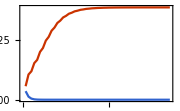
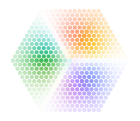
-Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
Block[{T=0.01,μ=1.0,α=1/3,Q=1.7,g=0.8,ks,ws,R,M,ϵs,Δ0s,ops,nF,SCMF},
Block[{L=12},{ks,ws}=Thread@Flatten[Table[{N[Q{l1+l2/2,l2 Sqrt[3]/2}/L],If[l1==0,If[l2==0||l2==L,1/6,1/2],If[l2==0,If[l1==L,1/6,1/2],If[l1+l2==L,1/2,1]]]},{l1,0,L},{l2,0,L-l1}],1];
ws=ws/Total[ws];
Block[{r,a=Q/L,δ,m},r=0.5;δ=0.1a;m=3a;
R=SparseArray@Outer[Boole[Norm[#1-{-1,1}#2-{Q,0}]<δ]&,ks,ks,1];
M=(r m)/((SparseArray@Outer[Norm[#1-#2]&,ks,Join[ks,ks.ReflectionMatrix[{0,1}],ks.ReflectionMatrix[{-Sqrt[3],1}/2]],1])^2+m^2)]];
(*Δ0s=Block[{k0=Q/2},Function[{kx,ky},(kx+ⅈ ky)/k0-(kx-ⅈ ky)^2/k0^2]@@@ks];*)
Δ0s=Function[{kx,ky},ⅈ]@@@ks;
ops=SparseArray[#,{4,4}]&/@{{{1,3}->1,{2,4}->-1},{{1,2}->-2}};
(* μ,T dependent *)
ϵs=Function[{kx,ky},kx^2+ky^2-μ+α (kx^3-3kx ky^2)]@@@ks;
nF=Compile[{{x,_Real}},(1-Tanh[x/(2T)])/2];
SCMF[{IQ_,Δs_}]:=Block[{hs,As,Bs},
hs=MapThread[Function[{ϵ1,ϵ2,Δ1,Δ2},
{{ϵ1,-Δ1,IQ,0},
{-Conjugate@Δ1,-ϵ1,0,-IQ},
{IQ,0,ϵ2,-Δ2},
{0,-IQ,-Conjugate@Δ2,-ϵ2}}],
{ϵs,R.ϵs,Δs,Conjugate[R.Δs]}];
{As,Bs}=Thread[ ws Table[Total[nF[#1]Table[Conjugate[#2].op.#2,{op,ops}]&@@@Thread@Eigensystem@h],{h,hs}]];
{-g Chop[Total@As],Block[{λ=0.3},(1-λ)Exp[-2(μ-1)^2]g M.Join[Bs,Conjugate[Bs],Exp[ⅈ 2π/3]Conjugate[Bs]]+λ Δs]}];
Block[{dat},
dat=NestList[SCMF,0.01{1,Δ0s}RandomReal[{0.2,1},2],50];Column@{Row@{ListLinePlot[Thread[{#1,Max@Abs@#2}&@@@dat],PlotRange->All,ImageSize->180],Block[{Δs},
Δs=dat⟦-1,-1⟧;
Δs=Δs/Max[Abs@Δs];
Graphics[MapThread[{#1,Point[#2]}&,{ComplexColor/@#1,#2}]&@@@{{Δs,ks},{Exp[-ⅈ 2π/3]Δs,ks.RotationMatrix[2π/3]},,{Exp[ⅈ 2π/3]Δs,ks.RotationMatrix[-2π/3]},{Conjugate[Δs],ks.ReflectionMatrix[{0,1}]},{Exp[ⅈ 2π/3]Conjugate[Δs],ks.ReflectionMatrix[{-Sqrt[3],1}/2]},
{Exp[-ⅈ 2π/3]Conjugate[Δs],ks.ReflectionMatrix[{Sqrt[3],1}/2]}},
ImageSize->140]]},Row[Function[{IQ,Δs},Graphics[MapThread[{#1,Point[#2]}&,{ComplexColor/@(Δs/Max[Abs@Δs]),ks}],PlotLabel->Style[NumberForm[Column@{IQ,Max[Abs@Δs]},3,ScientificNotationThreshold->{0,0}],12,Black],ImageSize->72]]@@@dat]}]
]
```

#### Phase Diagram

##### Data Collection

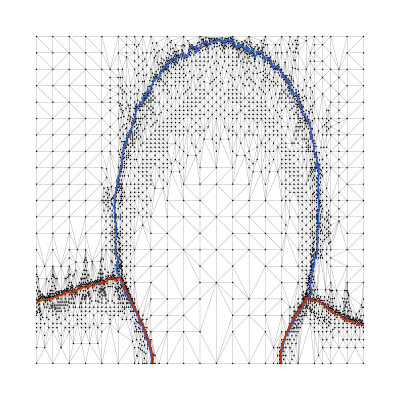

```mathematica
Block[{α=1/3,Q=1.7,g=0.8,r=0.5,μ0=1,δμ=2,ks,ws,R,M,ops,order,apxQ,Sample,file="data/Phase_170805.mx"},
SetDirectory[NotebookDirectory[]];
If[FileExistsQ[file],Import[file],order=<||>];
Block[{L=12},{ks,ws}=Thread@Flatten[Table[{N[Q{l1+l2/2,l2 Sqrt[3]/2}/L],If[l1==0,If[l2==0||l2==L,1/6,1/2],If[l2==0,If[l1==L,1/6,1/2],If[l1+l2==L,1/2,1]]]},{l1,0,L},{l2,0,L-l1}],1];
ws=ws/Total[ws];
Block[{a=Q/L,δ,m},δ=0.1a;m=3a;
R=SparseArray@Outer[Boole[Norm[#1-{-1,1}#2-{Q,0}]<δ]&,ks,ks,1];
M=m/((SparseArray@Outer[Norm[#1-#2]&,ks,Join[ks,ks.ReflectionMatrix[{0,1}],ks.ReflectionMatrix[{-Sqrt[3],1}/2]],1])^2+m^2)]];
ops=SparseArray[#,{4,4}]&/@{{{1,3}->1,{2,4}->-1},{{1,2}->-2}};
Options[Sample]={AccuracyGoal->3,PrecisionGoal->2,MaxIterations->100,Initialization->None};
Sample[{μ_,T_},OptionsPattern[Sample]]:=Block[{λ=0.9,ϵs,nF,SCMF},
ϵs=Function[{kx,ky},kx^2+ky^2-μ+α (kx^3-3kx ky^2)]@@@ks;
nF=Compile[{{x,_Real}},(1-Tanh[x/(2T)])/2];
SCMF[{IQ_,Δs_List}]:=Block[{hs,As,Bs},
hs=MapThread[Function[{ϵ1,ϵ2,Δ1,Δ2},
{{ϵ1,-Δ1,IQ,0},
{-Conjugate@Δ1,-ϵ1,0,-IQ},
{IQ,0,ϵ2,-Δ2},
{0,-IQ,-Conjugate@Δ2,-ϵ2}}],
{ϵs,R.ϵs,Δs,Conjugate[R.Δs]}];
{As,Bs}=Thread[ ws Table[Total[nF[#1]Table[Conjugate[#2].op.#2,{op,ops}]&@@@Thread@Eigensystem@h],{h,hs}]];
{-g Chop[Total@As],λ r Exp[-(μ-μ0)^2/(2δμ^2)]g M.Join[Bs,Conjugate[Bs],Exp[ⅈ 2π/3]Conjugate[Bs]]+(1-λ) Δs}];
apxQ[x:_?NumericQ,y:_?NumericQ]:=Norm[{x,y},∞]<10^(-OptionValue[AccuracyGoal])||2Abs[x-y]<Abs[x+y]10^(-OptionValue[PrecisionGoal]);
apxQ[x:{_?NumericQ..},y:{_?NumericQ..}]:=Norm[Flatten@{x,y},∞]<10^(-OptionValue[AccuracyGoal])||2Norm[x-y,∞]<Norm[x+y,∞]10^(-OptionValue[PrecisionGoal]);
apxQ[x_,y_]:=And@@MapThread[apxQ,{x,y}];
order[{μ,T}]=NestWhile[SCMF,
If[OptionValue[Initialization]===None,order[{μ,T}]/._Missing->{0.01,0.005ⅈ&/@ks},OptionValue[Initialization]],
(Block[{x,y,z},{x,y,z}=Max/@Abs/@{##}⟦All,2⟧;
If[Max[Abs[y-x],Abs[y-z]]>Abs[x-z],λ=0.9λ]];!apxQ[#2,#3])&,
3,OptionValue[MaxIterations]]];
(*Sample/@Keys@order;*)
Block[{mesh,refine},
mesh=DelaunayMesh[Keys@order];
refine[{p1_,p2_}]:=Block[{ds,need},
ds=Thread[{#1,Norm[#2,∞]}&@@@(order/@{p1,p2})];
need=And[Or@@(#1>0.&&#2>0.&&(#1-0.01)(#2-0.01)<0&&Abs[(#1-#2)]>0.2(#1+#2)&@@@ds),
Norm[p1-p2]>0.004];
(*need=Or@@(#1>0.&&#2>0.&&Max[#1,#2]>0.01&&Abs[(#1-#2)]>0.2Abs[#1+#2]&@@@ds);*)
If[need,
If[False,Sample[(p1+p2)/2,Initialization->Total[order/@{p1,p2}]/2]];If[False,Sample/@{p1,p2}];Line[{p1,p2}],Nothing]];
Print@Block[{od},
od={#1,Mean@Abs@#2}&@@@order;
Show[Graphics[{{AbsolutePointSize[1],Point[Keys@order],AbsoluteThickness[0.1],MeshPrimitives[mesh,1]},{AbsoluteThickness[2],refine@@@MeshPrimitives[mesh,1]}},AspectRatio->1,ImageSize->400],Show[ListContourPlot[Table[Append[p,od[p]⟦#1⟧],{p,Keys@od}],Contours->{0.01},ContourLabels->None,ContourStyle->Directive[#2,Opacity[1],AbsoluteThickness[1]],ContourShading->None,PlotRange->All]&@@@{{1,Blue},{2,Red}}]]]];
If[False,DumpSave[file,{α,Q,g,r,μ0,δμ,order}]];]
```

##### Data Processing

Load data

```mathematica
SetDirectory[NotebookDirectory[]];
Import["data/Phase_170805.mx"];
Length[order]
```

4059

Extract the leading TSC order and put together with the VDW order.

```mathematica
ord={#1,Mean@Abs@#2}&@@@order;
```

Trace out the phase boundaries (one boundary of VDW and two boundaries for TSC).

```mathematica
b1=Flatten[Cases[ListContourPlot[List@@AssociationMap[Append@@#&,First/@ord],Contours->{0.01},ContourShading->None],GraphicsComplex[pts_,gs_]:>First@Cases[gs,Line[is_]:>pts⟦is⟧,∞],∞],1];
{b2,b3}=Flatten[Cases[ListContourPlot[List@@AssociationMap[Append@@#&,Last/@ord],Contours->{0.01},ContourShading->None],GraphicsComplex[pts_,gs_]:>Cases[gs,Line[is_]:>pts⟦is⟧,∞],∞],1];
{b1,b2,b3}=MovingAverage[#,24]&/@{b1,b2,b3};
```

Construct the interpolation function for VDW and TSC orders.

```mathematica
Block[{μs,Ts},
μs=Range[0.5,1.5,0.005];
Ts=Range[0.,0.4,0.001];
{VDW,TSC}=Block[{f},f=Interpolation[List@@AssociationMap[Append@@#&,#/@ord],InterpolationOrder->1];
Interpolation[Flatten[Table[{μ,T,Chop[If[T>0.3,0,If[T==0.,f[μ,0.001],f[μ,T]]],10^-6]},{μ,μs},{T,Ts}],1]]]&/@{First,Last}];
```

Trace out the first order transition lines.

```mathematica
{b4,b5}=Block[{raw,l,x,fit,b},
raw=First@Last@Reap@Table[If[VDW[μ,T]≥0.01&&TSC[μ,T]≥0.01,Sow[{T,μ}]],{μ,#1,#2,0.002},{T,0.,0.1,0.002}];
fit=Fit[raw,{1,x,x^2,x^3,x^4},x];
b=Table[{fit,x},{x,Range[#1,#2,(#2-#1)/20]&@@MinMax[raw⟦All,1⟧]}];
Print@Graphics[{Point[Reverse/@raw],Red,Line[b]},ImageSize->120];
b]&@@@{{0.7,0.9},{1.2,1.4}};
```

-Graphics-

-Graphics-

Background

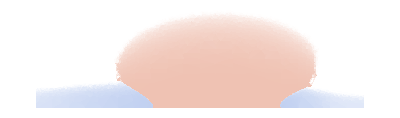

```mathematica
c1=First@ListDensityPlot[Cases[List@@AssociationMap[Append@@#&,First/@ord],{_,_,x_}/;x>0.005],ColorFunction->(Lighter[Red,1-0.3#]&)];c2=First@ListDensityPlot[Cases[List@@AssociationMap[Append@@#&,Last/@ord],{μ_,_,x_}/;μ<1&&x>0.005],ColorFunction->(Lighter[Blue,1-0.3#]&)];
c3=First@ListDensityPlot[Cases[List@@AssociationMap[Append@@#&,Last/@ord],{μ_,_,x_}/;μ>1&&x>0.005],ColorFunction->(Lighter[Blue,1-0.3#]&)];
Graphics[{c1,c2,c3}]
```

Calculate the Fermi surface DOS based on the VDW order

```mathematica
Block[{ks,ws,R,FSDOS},
Block[{L=24},{ks,ws}=Thread@Flatten[Table[{N[Q{l1+l2/2,l2 Sqrt[3]/2}/L],If[l1==0,If[l2==0||l2==L,1/6,1/2],If[l2==0,If[l1==L,1/6,1/2],If[l1+l2==L,1/2,1]]]},{l1,0,L},{l2,0,L-l1}],1];
ws=ws/Total[ws];
Block[{a=Q/L,δ,m},δ=0.1a;m=3a;
R=SparseArray@Outer[Boole[Norm[#1-{-1,1}#2-{Q,0}]<δ]&,ks,ks,1]];];
FSDOS[{μ_,T_,IQ_}]:=Block[{ϵs,hs},
ϵs=Function[{kx,ky},kx^2+ky^2-μ+α (kx^3-3kx ky^2)]@@@ks;
hs=MapThread[Function[{ϵ1,ϵ2},
{{ϵ1,IQ},
{IQ,ϵ2}}],
{ϵs,R.ϵs}];
{μ,T,ws.Table[Total[-2Im[1/(0.01ⅈ-(Eigenvalues@h))]],{h,hs}]}];
DOSmap=FSDOS/@(List@@AssociationMap[Append@@#&,First/@ord])];
ListPlot3D[DOSmap,MeshFunctions->{#3&},ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
b6=First@Cases[ListContourPlot[DOSmap,Contours->{0.2},ContourShading->None],GraphicsComplex[pts_,gs_]:>First@Cases[gs,Line[is_]:>pts⟦is⟧,∞],∞];
```

Define a function to put analysis of the phase point.

```mathematica
Analyze[{μ0_,T0_},{μ1_,T1_}]:=Block[{tol=0.01,μ,T,IQ,Δs,Δmax,Δmap,Δ,vfs},
{μ,T}=First@Nearest[Keys@order,{μ0,T0}];
{IQ,Δs}=order@{μ,T};
Δmax=Norm[Δs,∞];
If[Δmax>tol,
Δmap=Block[{L=12,ks,ws},{ks,ws}=Thread@Flatten[Table[{N[Q{l1+l2/2,l2 Sqrt[3]/2}/L],If[l1==0,If[l2==0||l2==L,1/6,1/2],If[l2==0,If[l1==L,1/6,1/2],If[l1+l2==L,1/2,1]]]},{l1,0,L},{l2,0,L-l1}],1];
ws=ws/Total[ws];
AssociationThread[Join[ks,ks.RotationMatrix[2π/3],ks.RotationMatrix[-2π/3],ks.ReflectionMatrix[{0,1}],ks.ReflectionMatrix[{-Sqrt[3],1}/2],ks.ReflectionMatrix[{Sqrt[3],1}/2]]->Join[Δs,Exp[-ⅈ 2π/3]Δs,Exp[ⅈ 2π/3]Δs,Conjugate[Δs],Exp[ⅈ 2π/3]Conjugate[Δs],Exp[-ⅈ 2π/3]Conjugate[Δs]]]];
Δ[k_]:=Mean[Δmap/@Nearest[Keys@Δmap,k]]];
If[IQ>tol,
Block[{ϵ,h},
ϵ[{kx_,ky_},ϛ_]:=kx^2+ky^2-μ+ϛ α(kx^3-3 kx ky^2);
h[k:{_,_}]:={
{ϵ[k,1],IQ},
{IQ,ϵ[k-{Q,0},-1]}};
vfs=First@ContourPlot[Det[h[{kx,ky}]]==0,{kx,0,Q},{ky,0,Sqrt[3]Q/2},ContourStyle->Directive[Black,AbsoluteThickness[1.2]],ContourLabels->None,
RegionFunction->({#1,#2}∈Triangle[Q{{0,0},{1,0},{1/2,Sqrt[3]/2}}]&)]
]];
Block[{fs,fsplt,bz0,bz1},
fs=First@Last@Reap@Cases[ContourPlot[kx^2+ky^2-μ+α (kx^3-3kx ky^2)==0,{kx,-1.2Q,1.2Q},{ky,-Q,Q}],GraphicsComplex[pts_,gs_]:>Sow/@Cases[gs,Line[is_]:>pts⟦is⟧,∞],∞];
fsplt[ks_,s_:1]:=If[Δmax<tol,{AbsoluteThickness[1.2],Line[ks]},{AbsoluteThickness[2],Line[ks,VertexColors->(ComplexColor[s Δ[s #]/Δmax]&/@ks)]}];
bz0={White,Polygon[CirclePoints[{Q,0},6]]};
bz1={Black,AbsoluteThickness[0.8],Line[Append[#,First@#]&@CirclePoints[{Q,0},6]]};{{Gray,AbsoluteThickness[1],Line[{{μ0,T0},{μ1,T1}}],White,EdgeForm[Directive[Gray,AbsoluteThickness[1]]],Disk[{μ0,T0},Offset[{2,2}]]},Inset[Graphics[If[IQ<tol,{bz0,{fsplt[#],fsplt[#.ReflectionMatrix[{1,0}],-1]}&/@fs},
{bz0,{AbsoluteThickness[1],Lighter[Blue,0.8],Line[#],Lighter[Red,0.8],Table[Rotate[Line[SortBy[Cases[#,{x_,y_}/;-π/3<ArcTan[x,y]<π/3:>{Q-x,y}],Last]],2π a/3,{0,0}],{a,0,2}]}&@Cases[#,{x_,y_}/;{x,y}∈Polygon[CirclePoints[{Q,0},6]]]&/@fs,Rotate[Scale[vfs,{1,#},{0,0}]&/@{-1,1},2π#/3,{0,0}]&/@{0,1,2},bz1}],ImageSize->40],{μ1,T1}]}]];
```

##### Result

Finally we assemble everything together into the phase diagram

```mathematica
Graphics[{{c1,c2,c3},
{Analyze[{1.,0.32},{0.81,0.3}],
Analyze[{0.78,0.03},{0.66,0.13}],
Analyze[{1.3,0.02},{1.43,0.096}],
Analyze[{0.8,0.2},{0.7,0.23}],
Analyze[{1.3,0.2},{1.33,0.30}],
Analyze[{1.1,0.05},{1.43,0.22}]},
{{DarkOrange,Dashed,Line[b6]},{Red,BSplineCurve[b1]},{Blue,BSplineCurve[b2],BSplineCurve[b3]},{Purple,AbsoluteThickness[2.5],Line[b4],Line[b5]}},{Red,Text["\!\(T\_IVCW\)",{1.12,0.315}],Text["IVCW",{1.06,0.18}],Text["(Slater insulator)",{1.06,0.14}],DarkOrange,Text["\!\(T\_ins\)",{1.,0.245}],Blue,Text["\!\(T\_c\)",{0.55,0.08}],Text["Topo. SC",{0.64,0.03}],Text["TSC",{1.36,0.02}]},Black,Text["Metal",{0.64,0.3}]},AspectRatio->0.5,PlotRange->{{0.5,1.5},{0,0.35}},Frame->True,FrameTicks->None,FrameLabel->{"     hole dope ← \!\(μ\) → electron dope","Temperature \!\(T\) →"},ImageSize->320]
```

-Graphics-

#### Phase Diagram (II)

##### Data Collection

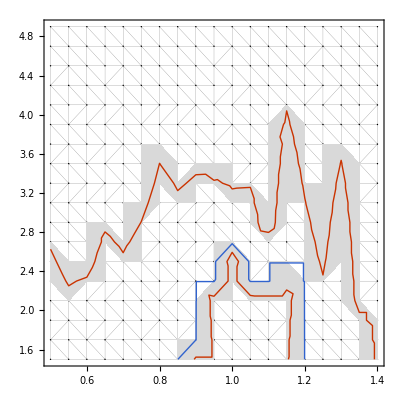

```mathematica
Block[{T=0.01,α=1/3,Q=1.7,r=0.5,μ0=1,δμ=0.8,ks,ws,R,M,ops,order,apxQ,Sample,flag=False,file="data/Phase_1705_2.mx"},
SetDirectory[NotebookDirectory[]];
If[FileExistsQ[file],Import[file],order=<||>];
Block[{L=12},{ks,ws}=Thread@Flatten[Table[{N[Q{l1+l2/2,l2 Sqrt[3]/2}/L],If[l1==0,If[l2==0||l2==L,1/6,1/2],If[l2==0,If[l1==L,1/6,1/2],If[l1+l2==L,1/2,1]]]},{l1,0,L},{l2,0,L-l1}],1];
ws=ws/Total[ws];
Block[{a=Q/L,δ,m},δ=0.1a;m=3a;
R=SparseArray@Outer[Boole[Norm[#1-{-1,1}#2-{Q,0}]<δ]&,ks,ks,1];
M=m/((SparseArray@Outer[Norm[#1-#2]&,ks,Join[ks,ks.ReflectionMatrix[{0,1}],ks.ReflectionMatrix[{-Sqrt[3],1}/2]],1])^2+m^2)]];
ops=SparseArray[#,{4,4}]&/@{{{1,3}->1,{2,4}->-1},{{1,2}->-2}};
Options[Sample]={AccuracyGoal->4,PrecisionGoal->3,MaxIterations->100,Initialization->None};
Sample[{μ_,t_},OptionsPattern[Sample]]:=Block[{λ=0.9,g=1/t,ϵs,nF,SCMF},
ϵs=Function[{kx,ky},kx^2+ky^2-μ+α (kx^3-3kx ky^2)]@@@ks;
nF=Compile[{{x,_Real}},(1-Tanh[x/(2T)])/2];
SCMF[{IQ_,Δs_List}]:=Block[{hs,As,Bs},
hs=MapThread[Function[{ϵ1,ϵ2,Δ1,Δ2},
{{ϵ1,-Δ1,IQ,0},
{-Conjugate@Δ1,-ϵ1,0,-IQ},
{IQ,0,ϵ2,-Δ2},
{0,-IQ,-Conjugate@Δ2,-ϵ2}}],
{ϵs,R.ϵs,Δs,Conjugate[R.Δs]}];
{As,Bs}=Thread[ ws Table[Total[nF[#1]Table[Conjugate[#2].op.#2,{op,ops}]&@@@Thread@Eigensystem@h],{h,hs}]];
{-g Chop[Total@As],λ r Exp[-(μ-μ0)^2/(2δμ^2)]g M.Join[Bs,Conjugate[Bs],Exp[ⅈ 2π/3]Conjugate[Bs]]+(1-λ) Δs}];
apxQ[x:_?NumericQ,y:_?NumericQ]:=Norm[{x,y},∞]<10^(-OptionValue[AccuracyGoal])||2Abs[x-y]<Abs[x+y]10^(-OptionValue[PrecisionGoal]);
apxQ[x:{_?NumericQ..},y:{_?NumericQ..}]:=Norm[Flatten@{x,y},∞]<10^(-OptionValue[AccuracyGoal])||2Norm[x-y,∞]<Norm[x+y,∞]10^(-OptionValue[PrecisionGoal]);
apxQ[x_,y_]:=And@@MapThread[apxQ,{x,y}];
flag=True;
order[{μ,t}]=NestWhile[SCMF,
If[OptionValue[Initialization]===None,order[{μ,t}]/._Missing->{0.01,0.005ⅈ&/@ks},OptionValue[Initialization]],
(Block[{x,y,z},{x,y,z}=Max/@Abs/@{##}⟦All,2⟧;
If[Max[Abs[y-x],Abs[y-z]]>Abs[x-z],λ=0.9λ]];!apxQ[#2,#3])&,
3,OptionValue[MaxIterations]]];
If[False,order=<||>;
Table[Sample[{μ,t}],{μ,0.5,1.4,0.1},{t,1.5,4,0.5}]];
Block[{mesh,refine},
If[False,Sample/@Keys@order];
mesh=DelaunayMesh[Keys@order];
refine[{p1_,p2_,p3_}]:=Block[{VDW,TSC,need},
{VDW,TSC}=Sign[Thread[{#1,Mean[Abs@#2]}&@@@(order/@{p1,p2,p3})]-0.005];
need=(Abs@Total[VDW]<3||Abs@Total[TSC]<3)&&(Area[Polygon[{p1,p2,p3}]]>0.0008||ArcLength[Line[{p1,p2,p3,p1}]]>0.4);
If[need,
If[False,Sample[(#1+#2)/2,Initialization->Total[order/@{#1,#2}]/2]&@@@{{p1,p2},{p2,p3},{p3,p1}}];
Polygon[{p1,p2,p3}],Nothing]];
Block[{od},
mesh=DelaunayMesh[Keys@order];
od={#1,Mean@Abs@#2}&@@@order;
If[True,
Print@Show[Graphics[{{AbsolutePointSize[1],Point[Keys@order],AbsoluteThickness[0.1],MeshPrimitives[mesh,1]},{LightGray,refine@@@MeshPrimitives[mesh,2]}},AspectRatio->1,Frame->True,ImageSize->400],Show[ListContourPlot[Table[Append[p,od[p]⟦#1⟧],{p,Keys@od}],Contours->{0.005},ContourLabels->None,ContourStyle->Directive[#2,Opacity[1],AbsoluteThickness[1]],ContourShading->None,PlotRange->All]&@@@{{1,Blue},{2,Red}}]]]]];
If[flag,DumpSave[file,{α,Q,T,r,μ0,δμ,order}]];]
```

Conclusion: The low temperature mean field iteration is not stable. Can not use to map out phase diagram

##### Schematic Plot

```mathematica
Block[{tcs,tvs,tms,dome},
tcs={{0.55,2.1},{0.6,2.3},{0.8,3.5},{0.9,3.4},{1.1,3.1},{1.2,4.0},{1.3,3.5},{1.35,2.5},{1.4,1.5}};
tvs={{0.85,1.5},{0.9,2.1},{1.0,2.8},{1.1,2.3},{1.15,2.5},{1.2,1.5}};
tms={{0.85,0.4},{0.95,0.5},{1.15,1.5},{1.3,0.4}};
dome[ts_,col_]:=Block[{ymin,lin,f1,f2},
ymin=Min@ts⟦All,2⟧;
lin[{{x1_,y1_},{x2_,y2_}}]:=Function[y,((x1-x2)y+x2 y1-x1 y2)/(y1-y2)];
f1=lin[ts⟦{1,2}⟧];
f2=lin[ts⟦{-1,-2}⟧];
{Table[{Lighter[col,1-y^1.4/10],FilledCurve[{BSplineCurve[ts],Line[{ts⟦-1⟧,{f2[y],y},{f1[y],y},ts⟦1⟧}]}]},{y,0,Min[ymin,1.5],0.1}],{col,If[ymin<1.5,Dashed,Nothing],BSplineCurve[ts]}}];
Graphics[{{dome[{{0.5,10},{1,11},{1.5,10}},Blue],dome[tcs,Green],dome[tvs,Orange],dome[tms,Red]},
{Blue,Text["Metal",{0.7,4.2}],Green,Text["TSC (d+id/p-ip)",{1.04,2.8}],Orange,Text["VCW",{1.05,1.7}],Red,Text["Mott(?)",{1.12,0.4}]}(*,
{AbsoluteThickness[1],Opacity[0.5],InfiniteLine[{#,2.3}&/@{0,1}]}*)},Frame->True,
FrameTicks->{{{{2.5,Rotate[Style["\!\(t/U∼|θ-θ\_mag|\)",14],π/2],{0,0}}},{{2.5,Rotate[Style["coupling\nweak ⟷ strong",14,LineSpacing->{0,14}],-π/2],{0,0}}}},{{{1,Style["chemial potential",14],{0,0}}},None}},PlotRange->{{0.5,1.5},{0,5}},PlotRangeClipping->True,ImageMargins->0,ImagePadding->{{24,34},{22,2}},AspectRatio->0.6,ImageSize->240]]
```

-Graphics-

```mathematica
Block[{tcs,tvs,tms,dome},
tcs={{0.55,2.1},{0.6,2.3},{0.8,3.5},{0.9,3.4},{1.1,3.1},{1.2,4.0},{1.3,3.5},{1.35,2.5},{1.4,1.5}};
tvs={{0.85,1.5},{0.9,2.1},{1.0,2.8},{1.1,2.3},{1.15,2.5},{1.2,1.5}};
tms={{0.85,0.4},{0.95,0.5},{1.15,1.5},{1.3,0.4}};
dome[ts_,col_]:=Block[{ymin,lin,f1,f2},
ymin=Min@ts⟦All,2⟧;
lin[{{x1_,y1_},{x2_,y2_}}]:=Function[y,((x1-x2)y+x2 y1-x1 y2)/(y1-y2)];
f1=lin[ts⟦{1,2}⟧];
f2=lin[ts⟦{-1,-2}⟧];
{Table[{Lighter[col,1-y^1.4/10],FilledCurve[{BSplineCurve[ts],Line[{ts⟦-1⟧,{f2[y],y},{f1[y],y},ts⟦1⟧}]}]},{y,0,Min[ymin,1.5],0.1}],{col,If[ymin<1.5,Dashed,Nothing],BSplineCurve[ts]}}];
Graphics[{{dome[{{0.5,10},{1,11},{1.5,10}},Blue],dome[tcs,Green],dome[tvs,Red]},
{Blue,Text["Metal",{0.75,3.9}],Green,Text["TSC",{0.9,2.8}],Red,Text["IVCW",{1.05,1.7}]}(*,
{AbsoluteThickness[1],Opacity[0.5],InfiniteLine[{#,2.3}&/@{0,1}]}*)},Frame->True,
FrameTicks->{{{{2.5,Rotate[Style["\!\(W/U∼|θ-θ\_mag|\)",14],π/2],{0,0}}},{{2.5,Rotate[Style["coupling\nweak ⟷ strong",14,LineSpacing->{0,14}],-π/2],{0,0}}}},{{{1,Style["chemial potential",14],{0,0}}},None}},PlotRange->{{0.5,1.5},{0,5}},PlotRangeClipping->True,ImageMargins->0,ImagePadding->{{24,34},{22,2}},AspectRatio->0.6,ImageSize->240]]
```

-Graphics-

## Functional RG

#### Fermi Surface Segmentation

Start with the K and K' pockets. Partition the momentum space by polar angle θ, such that k=k(cos θ,sin θ). For points on the Fermi surface, we need to solve for k_F

k_F^2-μ+ϛ α k_F^3 cos 3θ=0.

ϛ=±1 labels the K and K' pockets.

The valley U(1) requires that pocket label ϛ is also conserved, which can be assigned as the third component of the momentum.

Thus we introduce the generalized momentum,

p=(k,ϛ).

The band dispersion is fully determined by p=(k,ϛ)

ϵ(p)=k^2-μ+ϛ α Re k_+^3.

We take N_pch=6 patches on each pocket. Altogether 12 momentum points to sample.

```mathematica
Block[{μ=1,α=1/3,Npch=6,ϵp,kadj,pFs},
ϵp[{kx_,ky_,ϛ_}]:=kx^2+ky^2-μ+ϛ α(kx^3-3 kx ky^2);
kadj[{kx_,ky_,ϛ_},ϵ_]:=Block[{k0=Norm[{kx,ky}],r},
{r kx,r ky,ϛ}/.First@NSolve[{ϵp[{r kx,r ky,ϛ}]==ϵ,r>0,3α r k0<2},r]];
pFs=Flatten[Table[kadj[{Cos[θ],Sin[θ],ϛ},0],{θ,2π/Npch Range[Npch]},{ϛ,{1,-1}}],1];
ContourPlot[{ϵp[{kx,ky,1}],ϵp[{kx,ky,-1}]},{kx,-2,2},{ky,-2,2},FrameLabel->{"\!\(k\_x\)","\!\(k\_y\)"},ContourStyle->Directive[Opacity[1]],ContourLabels->None,PlotLabel->"\!\(α="<>ToString[InputForm@α]<>",μ="<>ToString[InputForm@μ]<>"\)",Epilog->{{Switch[#3,1,Blue,-1,Red],Point[{#1,#2}]}&@@@pFs,{AbsoluteThickness[1],Dashed,Table[HalfLine[{{0,0},{Cos[θ],Sin[θ]}}],{θ,2π/Npch (Range[Npch]+1/2)}]}},ImageSize->160]
]
```

-Graphics-

For any given direction θ (s.t. k_+=k e^(ⅈ θ)), we can further define

k_Λ^2-μ+ϛ α k_Λ^3 cos 3θ=Λ.

The Fermi momentum k_F is just a special case of k_(Λ=0).

Momentum rescaling function: p→p_Λ s.t. ϵ(p_Λ)=Λ.

#### Interaction Vertex

The interaction vertex (assume ω=0 and pin to Fermi surface) must satisfy the momentum conservation

V(p_1,p_2,p_3,p_4)=δ(p_1+p_3=p_2+p_4)v(p_1,p_2,p_3).

```mathematica
Diagram[{{}, {1, 2, 3, 4, 5}, {6, 7, 8, 9, 10, 11}}, 
 {1 -> {8, 6}, 2 -> {6, 10}, 3 -> {9, 7}, 4 -> {7, 11}, 5 -> {6, 7}}, {}, 
 {}, {1 -> 0, 2 -> 0, 3 -> 0, 4 -> 0, 5 -> 0}, 
 {6 -> {0., 0.2}, 7 -> {0., -0.2}, 8 -> {-0.4, 0.2}, 9 -> {-0.4, -0.2}, 
  10 -> {0.4, 0.2}, 11 -> {0.4, -0.2}}, {1 -> {{"Line"}, {"Arrow"}}, 
  2 -> {{"Line"}, {"Arrow"}}, 3 -> {{"Line"}, {"Arrow"}}, 
  4 -> {{"Line"}, {"Arrow"}}, 5 -> {{"DashedDoubleLine"}, {"None"}}, 
  6 -> {{"Dot"}}, 7 -> {{"Dot"}}, 8 -> {{Text["1",#]&}}, 9 -> {{Text["3",#]&}}, 
  10 -> {{Text["2",#]&}}, 11 -> {{Text["4",#]&}}}]
```

-Graphics-

```mathematica
Block[{μ=1,α=1/3,Npch=6,ϵp,kadj,pFs,V},
ϵp[{kx_,ky_,ϛ_}]:=kx^2+ky^2-μ+ϛ α(kx^3-3 kx ky^2);
kadj[{kx_,ky_,ϛ_},ϵ_]:=Block[{k0=Norm[{kx,ky}],r},{r kx,r ky,ϛ}/.First@NSolve[{ϵp[{r kx,r ky,ϛ}]==ϵ,r>0,3α r k0<2},r]];
pFs=Flatten[Table[kadj[{Cos[θ],Sin[θ],ϛ},0],{θ,2π/Npch Range[Npch]},{ϛ,{1,-1}}],1];
V=SparseArray@Table[Boole[p1+p3==p2+p4],{p1,pFs},{p2,pFs},{p3,pFs},{p4,pFs}]]
```

SparseArray[…]

The spin degrees of freedom is temporary suppressed.

(U(1))_c×(U(1))_v×SO(4) symmetry does not post any further constraint on v(p_1,p_2,p_3).

C_2 symmetry imposes that v(p_1,p_2,p_3)=v(-p_1,-p_2,-p_3).

#### One-Loop Diagram

One-loop diagrams

+++++

The external legs have generalized momentum p_(1,2,3,4) satisfying the conservation laws.

The internal legs have p_5, p_6 determined by the contraction.

For each given p_5, p_6 the Fermion bubble gives

Π_Λ(p_5,p_6)=∑_(|ϵ(p_5)|,|ϵ(p_6)|<Λ) (Θ(ϵ(p_5))-Θ(ϵ(p_6)))/(ϵ(p_5)-ϵ(p_6)).

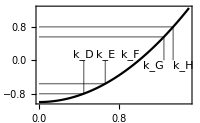

```mathematica
Block[{Λ=0.8,rate=0.7,ϵ,kadj},
ϵ[k_]:=k^2-1;
kadj[Λ_]:=Block[{k},k/.First@NSolve[{ϵ[k]==Λ,k≥0.},k]];
Plot[ϵ[k],{k,0,1.5},PlotStyle->Black,FrameLabel->{"\!\(k\)","\!\(ϵ(k)\)"},Epilog->{{{AbsoluteThickness[1],Opacity[0.5],{Line[{{#1,0},{#1,ϵ[#1]},{0,ϵ[#1]}}]}},
Text["\!\(k\_"<>#2<>"\)",{#1,0},{#3,Sign[ϵ[#1]]}]}&@@@Thread[{kadj[#]&/@{-Λ,-rate Λ,rate Λ,Λ},{"D","E","G","H"},{0,0,0.5,-0.5}}],
Text["\!\(k\_F\)",{kadj[0],0},{1,-1}]},ImageSize->200]]
```

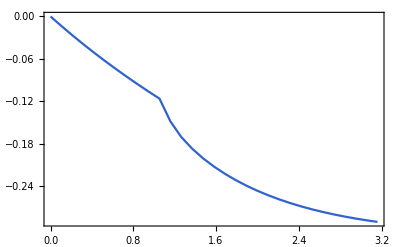

<|1→SparseArray[…],0.9→SparseArray[…],0.81→SparseArray[…],0.729→SparseArray[…],0.6561→SparseArray[…],0.59049→SparseArray[…],0.531441→SparseArray[…],0.478297→SparseArray[…],0.430467→SparseArray[…],0.38742→SparseArray[…],0.348678→SparseArray[…],0.313811→SparseArray[…],0.28243→SparseArray[…],0.254187→SparseArray[…],0.228768→SparseArray[…],0.205891→SparseArray[…],0.185302→SparseArray[…],0.166772→SparseArray[…],0.150095→SparseArray[…],0.135085→SparseArray[…],0.121577→SparseArray[…],0.109419→SparseArray[…],0.0984771→SparseArray[…],0.0886294→SparseArray[…],0.0797664→SparseArray[…],0.0717898→SparseArray[…],0.0646108→SparseArray[…],0.0581497→SparseArray[…],0.0523348→SparseArray[…],0.0471013→SparseArray[…],0.0423912→SparseArray[…]|>

```mathematica
Block[{μ=1,α=1/3,Npch=12,Λ=1,r=0.9,ϵ,kΛ,pchs,kdat,V,dV,update,flow},
ϵ[pch:{ϛ_,θ_},k_]:=k^2-μ+ϛ α k^3 Cos[3θ];
kΛ[pch_,e_]:=Block[{k},Which[ϵ[pch,0]≥e,0,ϵ[pch,2/(3α)]≤e,2/(3α),True,k/.First@FindRoot[ϵ[pch,k]==e,{k,0,2/(3α)}]]];
pchs=Tuples[{{1,-1},2π Range[Npch]/Npch}];
V=Block[{pFs},
pFs=Append[kΛ[#,0]{Cos[Last@#],Sin[Last@#]},First@#]&/@pchs;
SparseArray@Table[Boole[p1+p2==p3+p4],{p1,pFs},{p3,pFs},{p2,pFs},{p4,pFs}]];
kdat=Association[Table[pch->(kΛ[pch,#]&/@{-Λ,-r Λ,0,r Λ,Λ}),{pch,pchs}]];
dV:=Block[{f,Π},
f[pcha_,pchb_]:=Block[{kDa,kEa,kFa,kGa,kHa,kDb,kEb,kFb,kGb,kHb},
{{kDa,kEa,kFa,kGa,kHa},{kDb,kEb,kFb,kGb,kHb}}=kdat/@{pcha,pchb};
(*1/(4Npch^2)Total[(#2-#1) (#4-#3)/Abs[ϵ[pcha,(#1+#2)/2]-ϵ[pchb,(#3+#4)/2]]&@@@{{kDa,kEa,kFb,kHb},{kGa,kHa,kDb,kFb},{kDa,kFa,kGb,kHb},{kFa,kHa,kDb,kEb}}]*)
1/Npch^2Total[NIntegrate[ka kb/Abs[ϵ[pcha,ka]-ϵ[pchb,kb]],{ka,#1,#2},{kb,#3,#4},Method->{Automatic,"SymbolicProcessing"->False}]&@@@{{kDa,kEa,kFb,kHb},{kGa,kHa,kDb,kFb},{kDa,kFa,kGb,kHb},{kFa,kHa,kDb,kEb}}]];
Π=tTr[{SparseArray@Table[f[pch1,pch2],{pch1,pchs},{pch2,pchs}],#,#}&@Eye[2Npch,3],{{1,5},{2,8}}];
tTr[{V,V,Π},{{2,9},{5,10},{4,11},{7,12}},{1,6,3,8}]+tTr[{V,V,Π},{{2,9},{5,10},{8,11},{3,12}},{1,6,7,4}]-2tTr[{V,V,Π},{{4,9},{5,10},{6,11},{3,12}},{1,2,7,8}]+tTr[{V,V,Π},{{2,9},{5,10},{6,11},{3,12}},{1,4,7,8}]+tTr[{V,V,Π},{{6,9},{3,10},{4,11},{7,12}},{1,2,5,8}]];
update[_]:=Block[{},
V=V+dV;Λ=r Λ;
Do[kdat[pch]={#2,kΛ[pch,-r Λ],#3,kΛ[pch,r Λ],#4}&@@kdat[pch],{pch,pchs}];
Λ->V];
flow=Association[NestList[update,Λ->V,30]];
Print@ListLinePlot[{-Log[#],First@Sort@Eigenvalues[Normal@N@tTr[{flow@#},{},{{1,3},{2,4}}]]}&/@Keys@flow];
flow
]
```

```mathematica
Block[{Npch=12,pchs,flow,V,eigs},
pchs=Tuples[{{1,-1},2π Range[Npch]/Npch}];
flow=Out[5];
V=Last@flow;
eigs=SortBy[First]@Thread@Eigensystem@Normal@tTr[{SparseArray@Symmetrize[V,{Antisymmetric[{1,3}],Antisymmetric[{2,4}]}]},{},{{1,3},{2,4}}];
Print@eigs⟦;;10,1⟧;
ArrayRules@ArrayReshape[Chop@eigs⟦4,2⟧,{2Npch,2Npch}]]
```

{-0.290202,-0.289844,-0.289844,-0.289844,-0.275084,-0.275084,-0.275084,-0.275084,-0.275084,-0.275084}

{{1,19}→-0.424186,{3,21}→0.264294,{5,23}→-0.0146599,{7,13}→0.424186,{9,15}→-0.264294,{11,17}→0.0146599,{13,7}→-0.424186,{15,9}→0.264294,{17,11}→-0.0146599,{19,1}→0.424186,{21,3}→-0.264294,{23,5}→0.0146599,{_,_}→0}

## Other Ideas

### Band Structures

#### Electric Field Effect

Focus on one valley, Electric field shifts the top and bottom layer Dirac cones relative to each other in energy.

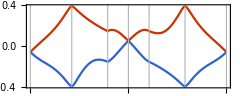

```mathematica
Block[{R=5,θ=1.08°,Ez=0.2,w0,w1,w3,Q,Ks,ind,NK,σv,qs,T,h0,h1,h},
{w0,w1,w3}=2.5{0.11,-0.12,0.00};
Q={{Sqrt[3],3},{-Sqrt[3],3}}/2;
Ks=Association[#->DeleteCases[Table[#+l.Q,{l,Tuples[Range[-#,#]&@Ceiling[2R/3],2]}]&[{-Sqrt[3],#}/2],k_/;Norm[N@k]-R>0.0001]&/@{1,-1}];
ind=AssociationThread[#->Range@Length@#]&[Join@@Ks];
NK=Length@ind;
σv[φ_,i_]:=Block[{U},
U=MatrixExp[ⅈ φ PauliMatrix[3]/2];
 ConjugateTranspose[U].PauliMatrix[i].U];
h0[k:{_,_}]:=Sum[KroneckerProduct[SparseArray[ind/@{#,#}->-(k-#)⟦i⟧&/@Ks[s],{NK,NK}],σv[s θ/2,i]],{s,{1,-1}},{i,{1,2}}]+Ez Sum[KroneckerProduct[SparseArray[ind/@{#,#}->s&/@Ks[s],{NK,NK}],PauliMatrix[0]],{s,{-1,1}}];
qs=RotationMatrix[# 2π/3].{0,-1}&/@{0,1,2};
T=AssociationThread[qs->(w0 σv[# 2π/3,0]+w1 σv[# 2π/3,1]+ⅈ w3 σv[# 2π/3,3]&/@{0,1,2})];
h1=Sum[KroneckerProduct[SparseArray[DeleteCases[ind/@{#,#+q}->1&/@Ks[1],{_,_Missing}->_],{NK,NK}],T[q]],{q,qs}];
h1=h1+ConjugateTranspose[h1];
h[k_]:=h0[k]+h1;
Block[{Es},
Es[k:{_?NumericQ,_?NumericQ}]:=Block[{es,n,m=0},
es=Sort[Eigenvalues@Normal@h[k]];
n=Length[es];
es⟦n/2-m;;n/2+m+1⟧];
BZPlot[Es,{"K1","Γ","M1","K2","M2","Γ","K1"},BZRules->{"Γ"->{0,0},"K1"->{Sqrt[3],-1}/2,"K2"->{Sqrt[3],1}/2,"M1"->{Sqrt[3],0}/2,"M2"->{Sqrt[3]/4,3/4}},MomentumResolution->1/32,AspectRatio->0.4,ImageSize->240]
]]
```

Weak field (field ≪ inter-layer coupling) distort the Fermi surface

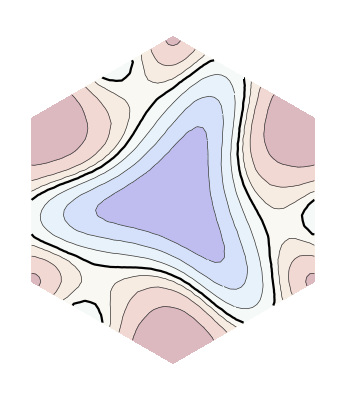
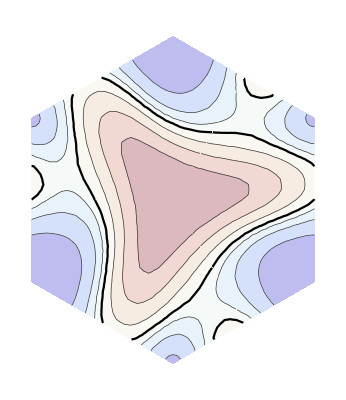
lower | upper
-Graphics- | -Graphics-

```mathematica
Block[{R=4,θ=1.08°,Ez=0.2,w0,w1,w3,Q,Ks,ind,NK,σv,qs,T,h0,h1,h,Es},
{w0,w1,w3}=2.5{0.11,-0.12,0.};
Q={{Sqrt[3],3},{-Sqrt[3],3}}/2;
Ks=Association[#->DeleteCases[Table[#+l.Q,{l,Tuples[Range[-#,#]&@Ceiling[2R/3],2]}]&[{-Sqrt[3],#}/2],k_/;Norm[N@k]-R>0.0001]&/@{1,-1}];
ind=AssociationThread[#->Range@Length@#]&[Join@@Ks];
NK=Length@ind;
σv[φ_,i_]:=Block[{U},
U=MatrixExp[ⅈ φ PauliMatrix[3]/2];
ConjugateTranspose[U].PauliMatrix[i].U];
h0[k:{_,_}]:=Sum[KroneckerProduct[SparseArray[ind/@{#,#}->-(k-#)⟦i⟧&/@Ks[s],{NK,NK}],σv[s θ/2,i]],{s,{1,-1}},{i,{1,2}}]+Ez Sum[KroneckerProduct[SparseArray[ind/@{#,#}->s&/@Ks[s],{NK,NK}],PauliMatrix[0]],{s,{-1,1}}];
qs=RotationMatrix[# 2π/3].{0,-1}&/@{0,1,2};
T=AssociationThread[qs->(w0 σv[# 2π/3,0]+w1 σv[# 2π/3,1]+ⅈ w3 σv[# 2π/3,3]&/@{0,1,2})];
h1=Sum[KroneckerProduct[SparseArray[DeleteCases[ind/@{#,#+q}->1&/@Ks[1],{_,_Missing}->_],{NK,NK}],T[q]],{q,qs}];
h1=h1+ConjugateTranspose[h1];
h[k_]:=h0[k]+h1;
Es[k:{_?NumericQ,_?NumericQ}]:=Block[{es,n,m=0},
es=Sort[Eigenvalues@Normal@h[k]];
n=Length[es];
es⟦n/2-m;;n/2+m+1⟧];
Block[{L=48,ks,ws,es,plot},
{ks,ws}=Thread@Table[If[l.{1,1}≤1&&l.{2,-1}≤1&&l.{-1,2}≤1,{l.{{Sqrt[3],3},{Sqrt[3],-3}}/2,
Switch[Boole@{l.{1,0}==0,l.{0,1}==0,l.{1,1}==1,l.{2,-1}==1,l.{-1,2}==1},
{0...},1,
{0...,1,0...},1/2,
{1,1,0...}|{0,0,1,__},1/3,
_,1/4]},Nothing],
{l,Tuples[Range[0,L]/L,2]}];
es=Thread[Es/@ks];
plot[e_]:=Block[{ord=Ordering[e],g},g=First@ListContourPlot[MapThread[Append,{ks⟦ord⟧,Rescale[#,MinMax@#]&@Accumulate[ws⟦ord⟧]}],
Contours->Range[1/8,7/8,1/8],ContourLabels->None,ContourStyle->(Directive[AbsoluteThickness[If[#==1/2,1.6,0.5]],Opacity[1],GrayLevel[If[#==1/2,0.,0.2]]]&/@Range[1/8,7/8,1/8]),ColorFunction->(Lighter[Blend[{RGBColor[0.163302, 0.119982, 0.79353],RGBColor[0.254221, 0.313173, 0.892833],RGBColor[0.407119, 0.543513, 0.938275],RGBColor[0.572715, 0.73338, 0.95065],RGBColor[0.720374, 0.855234, 0.928635],RGBColor[0.831017, 0.903518, 0.868326],GrayLevel[1],RGBColor[0.894452, 0.880139, 0.77279],RGBColor[0.907999, 0.789417, 0.652903],RGBColor[0.874505, 0.639254, 0.522424],RGBColor[0.79915, 0.446142, 0.391971],RGBColor[0.685695, 0.242449, 0.268261],RGBColor[0.534081, 0.0853132, 0.16669]},#],0.7]&)];
Graphics[Rotate[g,2π #/3,{0,0}]&/@{0,-1,1}]];
Grid[{{"lower","upper"},plot/@es}]
]]
```

Strong field (field ≳ inter-layer coupling) destroys nesting

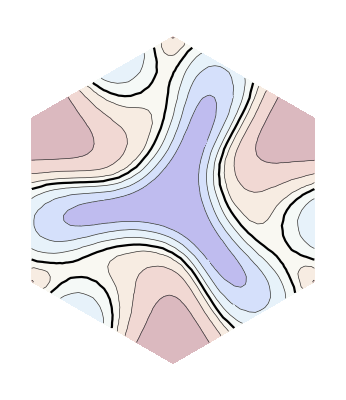
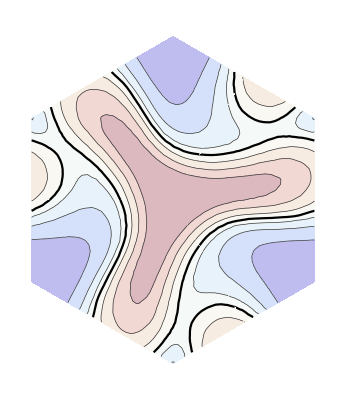
lower | upper
-Graphics- | -Graphics-

```mathematica
Block[{R=4,θ=1.08°,Ez=0.5,w0,w1,w3,Q,Ks,ind,NK,σv,qs,T,h0,h1,h,Es},
{w0,w1,w3}=2.5{0.11,-0.12,0.};
Q={{Sqrt[3],3},{-Sqrt[3],3}}/2;
Ks=Association[#->DeleteCases[Table[#+l.Q,{l,Tuples[Range[-#,#]&@Ceiling[2R/3],2]}]&[{-Sqrt[3],#}/2],k_/;Norm[N@k]-R>0.0001]&/@{1,-1}];
ind=AssociationThread[#->Range@Length@#]&[Join@@Ks];
NK=Length@ind;
σv[φ_,i_]:=Block[{U},
U=MatrixExp[ⅈ φ PauliMatrix[3]/2];
ConjugateTranspose[U].PauliMatrix[i].U];
h0[k:{_,_}]:=Sum[KroneckerProduct[SparseArray[ind/@{#,#}->-(k-#)⟦i⟧&/@Ks[s],{NK,NK}],σv[s θ/2,i]],{s,{1,-1}},{i,{1,2}}]+Ez Sum[KroneckerProduct[SparseArray[ind/@{#,#}->s&/@Ks[s],{NK,NK}],PauliMatrix[0]],{s,{-1,1}}];
qs=RotationMatrix[# 2π/3].{0,-1}&/@{0,1,2};
T=AssociationThread[qs->(w0 σv[# 2π/3,0]+w1 σv[# 2π/3,1]+ⅈ w3 σv[# 2π/3,3]&/@{0,1,2})];
h1=Sum[KroneckerProduct[SparseArray[DeleteCases[ind/@{#,#+q}->1&/@Ks[1],{_,_Missing}->_],{NK,NK}],T[q]],{q,qs}];
h1=h1+ConjugateTranspose[h1];
h[k_]:=h0[k]+h1;
Es[k:{_?NumericQ,_?NumericQ}]:=Block[{es,n,m=0},
es=Sort[Eigenvalues@Normal@h[k]];
n=Length[es];
es⟦n/2-m;;n/2+m+1⟧];
Block[{L=48,ks,ws,es,plot},
{ks,ws}=Thread@Table[If[l.{1,1}≤1&&l.{2,-1}≤1&&l.{-1,2}≤1,{l.{{Sqrt[3],3},{Sqrt[3],-3}}/2,
Switch[Boole@{l.{1,0}==0,l.{0,1}==0,l.{1,1}==1,l.{2,-1}==1,l.{-1,2}==1},
{0...},1,
{0...,1,0...},1/2,
{1,1,0...}|{0,0,1,__},1/3,
_,1/4]},Nothing],
{l,Tuples[Range[0,L]/L,2]}];
es=Thread[Es/@ks];
plot[e_]:=Block[{ord=Ordering[e],g},g=First@ListContourPlot[MapThread[Append,{ks⟦ord⟧,Rescale[#,MinMax@#]&@Accumulate[ws⟦ord⟧]}],
Contours->Range[1/8,7/8,1/8],ContourLabels->None,ContourStyle->(Directive[AbsoluteThickness[If[#==1/2,1.6,0.5]],Opacity[1],GrayLevel[If[#==1/2,0.,0.2]]]&/@Range[1/8,7/8,1/8]),ColorFunction->(Lighter[Blend[{RGBColor[0.163302, 0.119982, 0.79353],RGBColor[0.254221, 0.313173, 0.892833],RGBColor[0.407119, 0.543513, 0.938275],RGBColor[0.572715, 0.73338, 0.95065],RGBColor[0.720374, 0.855234, 0.928635],RGBColor[0.831017, 0.903518, 0.868326],GrayLevel[1],RGBColor[0.894452, 0.880139, 0.77279],RGBColor[0.907999, 0.789417, 0.652903],RGBColor[0.874505, 0.639254, 0.522424],RGBColor[0.79915, 0.446142, 0.391971],RGBColor[0.685695, 0.242449, 0.268261],RGBColor[0.534081, 0.0853132, 0.16669]},#],0.7]&)];
Graphics[Rotate[g,2π #/3,{0,0}]&/@{0,-1,1}]];
Grid[{{"lower","upper"},plot/@es}]
]]
```

One expect the electric field to destroy the nesting and hence reduce the valley fluctuation and the inter-valley pairing.

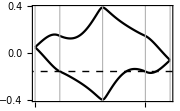
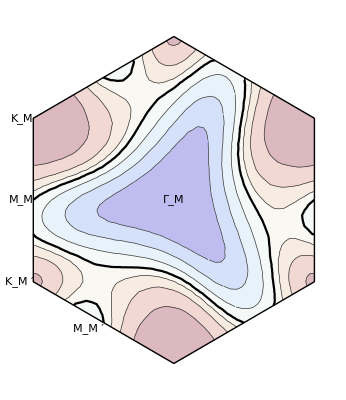
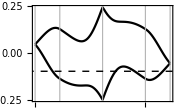
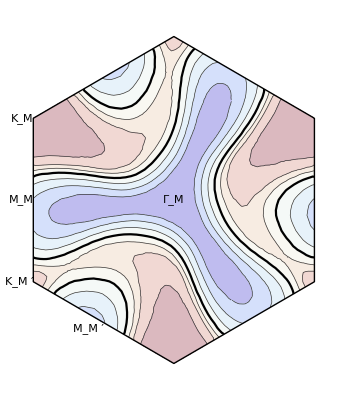
-Graphics--Graphics-(a)
-Graphics--Graphics-(b)

```mathematica
Column[Function[{Ez,lab},Block[{R=5,L=48,θ=1.08°,w0,w1,w3,Q,Ks,ind,NK,σv,qs,T,h0,h1,h},
{w0,w1,w3}=2.5{0.11,-0.12,0.00};
Q={{Sqrt[3],3},{-Sqrt[3],3}}/2;
Ks=Association[#->DeleteCases[Table[#+l.Q,{l,Tuples[Range[-#,#]&@Ceiling[2R/3],2]}]&[{-Sqrt[3],#}/2],k_/;Norm[N@k]-R>0.0001]&/@{1,-1}];
ind=AssociationThread[#->Range@Length@#]&[Join@@Ks];
NK=Length@ind;
σv[φ_,i_]:=Block[{U},
U=MatrixExp[ⅈ φ PauliMatrix[3]/2];
 ConjugateTranspose[U].PauliMatrix[i].U];
h0[k:{_,_}]:=Sum[KroneckerProduct[SparseArray[ind/@{#,#}->-(k-#)⟦i⟧&/@Ks[s],{NK,NK}],σv[s θ/2,i]],{s,{1,-1}},{i,{1,2}}]+Ez Sum[KroneckerProduct[SparseArray[ind/@{#,#}->s&/@Ks[s],{NK,NK}],PauliMatrix[0]],{s,{-1,1}}];
qs=RotationMatrix[# 2π/3].{0,-1}&/@{0,1,2};
T=AssociationThread[qs->(w0 σv[# 2π/3,0]+w1 σv[# 2π/3,1]+ⅈ w3 σv[# 2π/3,3]&/@{0,1,2})];
h1=Sum[KroneckerProduct[SparseArray[DeleteCases[ind/@{#,#+q}->1&/@Ks[1],{_,_Missing}->_],{NK,NK}],T[q]],{q,qs}];
h1=h1+ConjugateTranspose[h1];
h[k_]:=h0[k]+h1;
Block[{Es},
Es[k:{_?NumericQ,_?NumericQ}]:=Block[{es,n,m=0},
es=Sort[Eigenvalues@Normal@h[k]];
n=Length[es];
es⟦n/2-m;;n/2+m+1⟧];
Overlay[{#,Text[Style[lab,FontFamily->"CMU"]]}]&@Row@Block[{μ},Reverse@{Block[{ks,ws,es,plot},
{ks,ws}=Thread@Table[If[l.{1,1}≤1&&l.{2,-1}≤1&&l.{-1,2}≤1,{l.{{Sqrt[3],3},{Sqrt[3],-3}}/2,
Switch[Boole@{l.{1,0}==0,l.{0,1}==0,l.{1,1}==1,l.{2,-1}==1,l.{-1,2}==1},
{0...},1,
{0...,1,0...},1/2,
{1,1,0...}|{0,0,1,__},1/3,
_,1/4]},Nothing],
{l,Tuples[Range[0,L]/L,2]}];
es=Thread[Es/@ks];
plot[e_]:=Block[{ord=Ordering[e],g},
μ=First[Sort[e]⟦Nearest[Rescale[#,MinMax@#]&@Accumulate[ws⟦ord⟧]->"Index",1/2]⟧];
g=First@ListContourPlot[MapThread[Append,{ks⟦ord⟧,Rescale[#,MinMax@#]&@Accumulate[ws⟦ord⟧]}],
Contours->Range[1/8,7/8,1/8],ContourLabels->None,ContourStyle->(Directive[AbsoluteThickness[If[#==1/2,1.6,0.5]],Opacity[1],GrayLevel[If[#==1/2,0.,0.2]]]&/@Range[1/8,7/8,1/8]),ColorFunction->(Lighter[Blend[{RGBColor[0.163302, 0.119982, 0.79353],RGBColor[0.254221, 0.313173, 0.892833],RGBColor[0.407119, 0.543513, 0.938275],RGBColor[0.572715, 0.73338, 0.95065],RGBColor[0.720374, 0.855234, 0.928635],RGBColor[0.831017, 0.903518, 0.868326],GrayLevel[1],RGBColor[0.894452, 0.880139, 0.77279],RGBColor[0.907999, 0.789417, 0.652903],RGBColor[0.874505, 0.639254, 0.522424],RGBColor[0.79915, 0.446142, 0.391971],RGBColor[0.685695, 0.242449, 0.268261],RGBColor[0.534081, 0.0853132, 0.16669]},#],0.7]&)];
Graphics[{Rotate[g,2π #/3,{0,0}]&/@{0,-1,1},{AbsoluteThickness[1],Line[Append[#,First[#]]]&@CirclePoints[{1,π/6},6]},
{Text["\!\(Γ\_M\)"],Text["\!\(M\_M\)",{-Sqrt[3]/2,0},{1,0}],Text["\!\(M\_M\%′\)",{-Sqrt[3]/4,-3/4},{0.8,0.7}],Text["\!\(K\_M\)",{-Sqrt[3]/2,1/2},{1,-0.2}],Text["\!\(K\_M\%′\)",{-Sqrt[3]/2,-1/2},{1,0.2}]}},ImageSize->{Automatic,100}]];
plot[First@es]],BZPlot[Es,{"\!\(K\_M\)","\!\(M\_M\)","\!\(Γ\_M\)","\!\(M\_M\%′\)","\!\(K\_M\%′\)"},BZRules->{"\!\(Γ\_M\)"->{0,0},"\!\(K\_M\)"->{-Sqrt[3],1}/2,
"\!\(K\_M\%′\)"->{-Sqrt[3],-1}/2,"\!\(M\_M\)"->{-Sqrt[3],0}/2,"\!\(M\_M\%′\)"->{-Sqrt[3]/4,-3/4}},MomentumResolution->1/32,PlotStyle->Black,FrameLabel->{None,"\!\(E\) [a.u.]"},Epilog->{AbsoluteThickness[1],Dashed,InfiniteLine[{#,μ}&/@{0,1}]},ImageSize->180]}]
]]]@@@{{0.2,"(a)"},{0.6,"(b)"}}]
```

#### Bilayer-On-Bilayer

For twisted bilayer-on-bilayer, the band structure is very similar, expect at K points: the Dirac cones are replaced by quadratic band touchings.

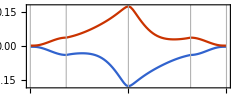

```mathematica
Block[{R=5,θ=1.08°,Ez=-0.0,w0,w1,w3,wb,Q,Ks,ind,NK,σv,qs,T,h0,h1,h},
{w0,w1,w3,wb}=1.3{0.275,-0.3,0.,0.4};
Q={{Sqrt[3],3},{-Sqrt[3],3}}/2;
Ks=Association[#->DeleteCases[Table[#+l.Q,{l,Tuples[Range[-#,#]&@Ceiling[2R/3],2]}]&[{-Sqrt[3],#}/2],k_/;Norm[N@k]-R>0.0001]&/@{1,-1}];
ind=AssociationThread[#->Range@Length@#]&[Join@@Ks];
NK=Length@ind;
σv[φ_,i_]:=Block[{U},
U=MatrixExp[ⅈ φ PauliMatrix[3]/2];
 ConjugateTranspose[U].PauliMatrix[i].U];
h0[k:{_,_}]:=Sum[Sum[KroneckerProduct[SparseArray[ind/@{#,#}->-(k-#)⟦i⟧&/@Ks[s],{NK,NK}],PauliMatrix[0],σv[s θ/2,i]],{i,{1,2}}]+Ez (KroneckerProduct[SparseArray[ind/@{#,#}->s&/@Ks[s],{NK,NK}],PauliMatrix[0],PauliMatrix[0]]+KroneckerProduct[Eye[NK],PauliMatrix[3],PauliMatrix[0]]),{s,{-1,1}}];
qs=RotationMatrix[# 2π/3].{0,-1}&/@{0,1,2};
T=AssociationThread[qs->(w0 σv[# 2π/3,0]+w1 σv[# 2π/3,1]+ⅈ w3 σv[# 2π/3,3]&/@{0,1,2})];
h1=Sum[KroneckerProduct[SparseArray[DeleteCases[ind/@{#,#+q}->1&/@Ks[1],{_,_Missing}->_],{NK,NK}],Represent[(σ[1]+ⅈ σ[2])/2],T[q]],{q,qs}]+KroneckerProduct[Eye[NK],wb Represent[(σ[1,1]+σ[2,2])/2]];
h1=h1+ConjugateTranspose[h1];
h[k_]:=h0[k]+h1;
Block[{Es},
Es[k:{_?NumericQ,_?NumericQ}]:=Block[{es,n,m=1},
es=Sort[Eigenvalues@Normal@h[k]];
n=Length[es];
es⟦n/2-m+1;;n/2+m⟧];
BZPlot[Es,{"K1","M1","Γ","M2","K2"},BZRules->{"Γ"->ReIm@0,"K1"-> ReIm@Exp[-ⅈ π/6],"K2"->ReIm@Exp[ⅈ π/6],"M1"->Sqrt[3]/2 ReIm@1,"M2"->Sqrt[3]/2 ReIm@Exp[ⅈ π/3]},MomentumResolution->1/32,AspectRatio->0.4,ImageSize->240]
]
]
```

The Fermi surface is still triangular (near f=-1/2). As long as we are not approaching to the charge neutrality, the Fermi surface has no significant difference.

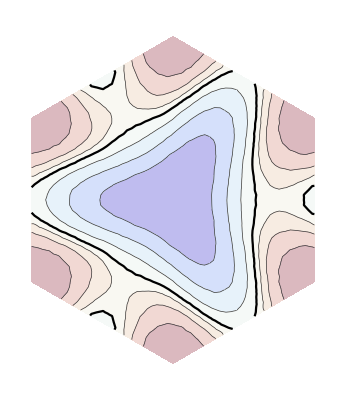
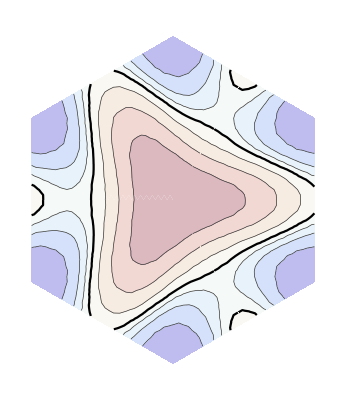
lower | upper
-Graphics- | -Graphics-

```mathematica
Block[{R=3,θ=1.08°,Ez=0.,w0,w1,w3,wb,Q,Ks,ind,NK,σv,qs,T,h0,h1,h,Es},
{w0,w1,w3,wb}=1.3{0.275,-0.3,0.,0.4};
Q={{Sqrt[3],3},{-Sqrt[3],3}}/2;
Ks=Association[#->DeleteCases[Table[#+l.Q,{l,Tuples[Range[-#,#]&@Ceiling[2R/3],2]}]&[{-Sqrt[3],#}/2],k_/;Norm[N@k]-R>0.0001]&/@{1,-1}];
ind=AssociationThread[#->Range@Length@#]&[Join@@Ks];
NK=Length@ind;
σv[φ_,i_]:=Block[{U},
U=MatrixExp[ⅈ φ PauliMatrix[3]/2];
 ConjugateTranspose[U].PauliMatrix[i].U];
h0[k:{_,_}]:=Sum[Sum[KroneckerProduct[SparseArray[ind/@{#,#}->-(k-#)⟦i⟧&/@Ks[s],{NK,NK}],PauliMatrix[0],σv[s θ/2,i]],{i,{1,2}}]+Ez (KroneckerProduct[SparseArray[ind/@{#,#}->s&/@Ks[s],{NK,NK}],PauliMatrix[0],PauliMatrix[0]]+KroneckerProduct[Eye[NK],PauliMatrix[3],PauliMatrix[0]]),{s,{-1,1}}];
qs=RotationMatrix[# 2π/3].{0,-1}&/@{0,1,2};
T=AssociationThread[qs->(w0 σv[# 2π/3,0]+w1 σv[# 2π/3,1]+ⅈ w3 σv[# 2π/3,3]&/@{0,1,2})];
h1=Sum[KroneckerProduct[SparseArray[DeleteCases[ind/@{#,#+q}->1&/@Ks[1],{_,_Missing}->_],{NK,NK}],Represent[(σ[1]+ⅈ σ[2])/2],T[q]],{q,qs}]+KroneckerProduct[Eye[NK],wb Represent[(σ[1,1]+σ[2,2])/2]];
h1=h1+ConjugateTranspose[h1];
h[k_]:=h0[k]+h1;
Es[k:{_?NumericQ,_?NumericQ}]:=Block[{es,n,m=1},
es=Sort[Eigenvalues@Normal@h[k]];
n=Length[es];
es⟦n/2-m+1;;n/2+m⟧];
Block[{L=48,ks,ws,es,plot},
{ks,ws}=Thread@Table[If[l.{1,1}≤1&&l.{2,-1}≤1&&l.{-1,2}≤1,{l.{{Sqrt[3],3},{Sqrt[3],-3}}/2,
Switch[Boole@{l.{1,0}==0,l.{0,1}==0,l.{1,1}==1,l.{2,-1}==1,l.{-1,2}==1},
{0...},1,
{0...,1,0...},1/2,
{1,1,0...}|{0,0,1,__},1/3,
_,1/4]},Nothing],
{l,Tuples[Range[0,L]/L,2]}];
es=Thread[Es/@ks];
plot[e_]:=Block[{ord=Ordering[e],g},g=First@ListContourPlot[MapThread[Append,{ks⟦ord⟧,Rescale[#,MinMax@#]&@Accumulate[ws⟦ord⟧]}],
Contours->Range[1/8,7/8,1/8],ContourLabels->None,ContourStyle->(Directive[AbsoluteThickness[If[#==1/2,1.6,0.5]],Opacity[1],GrayLevel[If[#==1/2,0.,0.2]]]&/@Range[1/8,7/8,1/8]),ColorFunction->(Lighter[Blend[{RGBColor[0.163302, 0.119982, 0.79353],RGBColor[0.254221, 0.313173, 0.892833],RGBColor[0.407119, 0.543513, 0.938275],RGBColor[0.572715, 0.73338, 0.95065],RGBColor[0.720374, 0.855234, 0.928635],RGBColor[0.831017, 0.903518, 0.868326],GrayLevel[1],RGBColor[0.894452, 0.880139, 0.77279],RGBColor[0.907999, 0.789417, 0.652903],RGBColor[0.874505, 0.639254, 0.522424],RGBColor[0.79915, 0.446142, 0.391971],RGBColor[0.685695, 0.242449, 0.268261],RGBColor[0.534081, 0.0853132, 0.16669]},#],0.7]&)];
Graphics[Rotate[g,2π #/3,{0,0}]&/@{0,-1,1}]];
Grid[{{"lower","upper"},plot/@es}]
]]
```